# Summary of Core Language Features added in 6.0

Peter Cullen Burbery

In this notebook I create some examples for core language features added in 6.0. This is helpful for making sure I understand the basics first before I move onto more advanced stuff like geographics and machine learning and statistics and physics. I also think its interesting to see the evolution of the Wolfram language over time. I started using Mathematica with major version 12 and maybe incremental release 12.1 or 12.2 and like looking at previous releases to learn new things. I'm hoping to look at other releases like 7.0, 8.0 as well, but the notebooks get very large very quickly so I will upload related notebooks after another to avoid reaching the 20 megabyte upload limit for Wolfram Community.

I will note that I will not be using vowels a,e,i,o, u, or y in the examples. I want to reserve vowels for special purposes and use consonants by default. For example I can use i as the dummy index variable for table like

```mathematica
Table[Cos[π/i],{i,19}]
```

{-1,0,1/2,1/(√2),1/4 (1+√5),(√3)/2,Cos[π/7],Cos[π/8],Cos[π/9],√(5/8+(√5)/8),Cos[π/11],(1+√3)/(2 √2),Cos[π/13],Cos[π/14],Cos[π/15],Cos[π/16],Cos[π/17],Cos[π/18],Cos[π/19]}

I would also like to mention that I will not include that much text and mainly code.

I will also note that I used PersistResourceFunction with my ResourceFunction SymbolicIndexedArray for testing purposes, so I don't have to add ResourceFunction["SymbolicIndexedArray"] every time.

I can't look at earlier releases because there's no guide for whats new in 5.0. The farthest back I can go in the documentation system is version 6.0

## Core Language

## Span

```mathematica
SymbolicIndexedArray[x,19]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
SymbolicIndexedArray[x,19][[2;;5]]
```

{x2,x3,x4,x5}

```mathematica
SymbolicIndexedArray[x,19][[2;;16;;3]]
```

{x2,x5,x8,x11,x14}

```mathematica
t=SymbolicIndexedArray[x,19]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
t[[2;;16;;3]]=x
```

x

```mathematica
t
```

{x1,x,x3,x4,x,x6,x7,x,x9,x10,x,x12,x13,x,x15,x16,x17,x18,x19}

```mathematica
t[[2;;5]]={p,q,r,s}
```

{p,q,r,s}

```mathematica
t
```

{x1,p,q,r,s,x6,x7,x,x9,x10,x,x12,x13,x,x15,x16,x17,x18,x19}

## Band

```mathematica
SparseArray[{Band[{1,1}]->x,Band[{2,1}]->z},{5,5}]
```

SparseArray[…]

```mathematica
SparseArray[{Band[{1,1}]->x,Band[{2,1}]->z},{5,5}]//MatrixForm
```

(x | 0 | 0 | 0 | 0
z | x | 0 | 0 | 0
0 | z | x | 0 | 0
0 | 0 | z | x | 0
0 | 0 | 0 | z | x)

```mathematica
Normal[SparseArray[{Band[{1,1}]->x,Band[{2,1}]->z},{5,5}]//MatrixForm]
```

(x | 0 | 0 | 0 | 0
z | x | 0 | 0 | 0
0 | z | x | 0 | 0
0 | 0 | z | x | 0
0 | 0 | 0 | z | x)

## ReplacePart

```mathematica
SymbolicIndexedArray[x,19]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
ReplacePart[SymbolicIndexedArray[x,19],3->xxx]
```

{x1,x2,xxx,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
ReplacePart[SymbolicIndexedArray[x,19],{2->xxx,5->fff}]
```

{x1,xxx,x3,x4,fff,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
ReplacePart[SymbolicIndexedArray[x,{19,19}],{3,5}->threefive]
```

{{x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119},{x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219},{x31,x32,x33,x34,threefive,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319},{x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419},{x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519},{x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619},{x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719},{x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819},{x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919},{x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019},{x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119},{x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219},{x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319},{x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419},{x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519},{x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619},{x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719},{x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819},{x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919}}

```mathematica
ReplacePart[SymbolicIndexedArray[x,{19,19}],{i_,i_}->vowelvowel]
```

{{vowelvowel,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119},{x21,vowelvowel,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219},{x31,x32,vowelvowel,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319},{x41,x42,x43,vowelvowel,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419},{x51,x52,x53,x54,vowelvowel,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519},{x61,x62,x63,x64,x65,vowelvowel,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619},{x71,x72,x73,x74,x75,x76,vowelvowel,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719},{x81,x82,x83,x84,x85,x86,x87,vowelvowel,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819},{x91,x92,x93,x94,x95,x96,x97,x98,vowelvowel,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919},{x101,x102,x103,x104,x105,x106,x107,x108,x109,vowelvowel,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019},{x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,vowelvowel,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119},{x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,vowelvowel,x1213,x1214,x1215,x1216,x1217,x1218,x1219},{x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,vowelvowel,x1314,x1315,x1316,x1317,x1318,x1319},{x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,vowelvowel,x1415,x1416,x1417,x1418,x1419},{x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,vowelvowel,x1516,x1517,x1518,x1519},{x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,vowelvowel,x1617,x1618,x1619},{x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,vowelvowel,x1718,x1719},{x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,vowelvowel,x1819},{x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,vowelvowel}}

```mathematica
ReplacePart[b+c+d^n,{{3,2}->x+z,2->g^100}]
```

b+d^(x+z)+g^100

```mathematica
ReplacePart[3->xxx][SymbolicIndexedArray[x,19]]
```

{x1,x2,xxx,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

## ArrayFlatten

```mathematica
m=SymbolicIndexedArray[x,{19,19}]
```

{{x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119},{x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219},{x31,x32,x33,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319},{x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419},{x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519},{x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619},{x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719},{x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819},{x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919},{x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019},{x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119},{x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219},{x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319},{x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419},{x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519},{x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619},{x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719},{x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819},{x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919}}

```mathematica
ArrayFlatten[{{m,m,m},{m,m,m}}]
```

{{x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119,x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119,x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119},{x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219,x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219,x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219},{x31,x32,x33,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319,x31,x32,x33,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319,x31,x32,x33,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319},{x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419,x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419,x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419},{x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519,x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519,x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519},{x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619,x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619,x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619},{x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719,x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719,x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719},{x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819,x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819,x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819},{x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919,x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919,x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919},{x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019,x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019,x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019},{x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119,x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119,x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119},{x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219,x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219,x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219},{x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319,x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319,x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319},{x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419,x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419,x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419},{x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519,x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519,x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519},{x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619,x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619,x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619},{x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719,x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719,x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719},{x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819,x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819,x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819},{x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919,x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919,x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919},{x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119,x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119,x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119},{x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219,x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219,x21,x22,x23,x24,x25,x26,x27,x28,x29,x210,x211,x212,x213,x214,x215,x216,x217,x218,x219},{x31,x32,x33,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319,x31,x32,x33,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319,x31,x32,x33,x34,x35,x36,x37,x38,x39,x310,x311,x312,x313,x314,x315,x316,x317,x318,x319},{x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419,x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419,x41,x42,x43,x44,x45,x46,x47,x48,x49,x410,x411,x412,x413,x414,x415,x416,x417,x418,x419},{x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519,x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519,x51,x52,x53,x54,x55,x56,x57,x58,x59,x510,x511,x512,x513,x514,x515,x516,x517,x518,x519},{x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619,x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619,x61,x62,x63,x64,x65,x66,x67,x68,x69,x610,x611,x612,x613,x614,x615,x616,x617,x618,x619},{x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719,x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719,x71,x72,x73,x74,x75,x76,x77,x78,x79,x710,x711,x712,x713,x714,x715,x716,x717,x718,x719},{x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819,x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819,x81,x82,x83,x84,x85,x86,x87,x88,x89,x810,x811,x812,x813,x814,x815,x816,x817,x818,x819},{x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919,x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919,x91,x92,x93,x94,x95,x96,x97,x98,x99,x910,x911,x912,x913,x914,x915,x916,x917,x918,x919},{x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019,x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019,x101,x102,x103,x104,x105,x106,x107,x108,x109,x1010,x1011,x1012,x1013,x1014,x1015,x1016,x1017,x1018,x1019},{x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119,x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119,x111,x112,x113,x114,x115,x116,x117,x118,x119,x1110,x1111,x1112,x1113,x1114,x1115,x1116,x1117,x1118,x1119},{x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219,x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219,x121,x122,x123,x124,x125,x126,x127,x128,x129,x1210,x1211,x1212,x1213,x1214,x1215,x1216,x1217,x1218,x1219},{x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319,x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319,x131,x132,x133,x134,x135,x136,x137,x138,x139,x1310,x1311,x1312,x1313,x1314,x1315,x1316,x1317,x1318,x1319},{x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419,x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419,x141,x142,x143,x144,x145,x146,x147,x148,x149,x1410,x1411,x1412,x1413,x1414,x1415,x1416,x1417,x1418,x1419},{x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519,x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519,x151,x152,x153,x154,x155,x156,x157,x158,x159,x1510,x1511,x1512,x1513,x1514,x1515,x1516,x1517,x1518,x1519},{x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619,x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619,x161,x162,x163,x164,x165,x166,x167,x168,x169,x1610,x1611,x1612,x1613,x1614,x1615,x1616,x1617,x1618,x1619},{x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719,x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719,x171,x172,x173,x174,x175,x176,x177,x178,x179,x1710,x1711,x1712,x1713,x1714,x1715,x1716,x1717,x1718,x1719},{x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819,x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819,x181,x182,x183,x184,x185,x186,x187,x188,x189,x1810,x1811,x1812,x1813,x1814,x1815,x1816,x1817,x1818,x1819},{x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919,x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919,x191,x192,x193,x194,x195,x196,x197,x198,x199,x1910,x1911,x1912,x1913,x1914,x1915,x1916,x1917,x1918,x1919}}

```mathematica
Length[Flatten[ArrayFlatten[{{m,m,m},{m,m,m}}]]]
```

2166

```mathematica
Length[Flatten[{{m,m,m},{m,m,m}}]]
```

2166

```mathematica
Dimensions[{{m,m,m},{m,m,m}}]
```

{2,3,19,19}

```mathematica
Dimensions[ArrayFlatten[{{m,m,m},{m,m,m}}]]
```

{38,57}

```mathematica
m=SymbolicIndexedArray[x,19]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
{{0,0,m},{m,m,0}}
```

{{0,0,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}},{{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19},0}}

```mathematica
ArrayFlatten[{{0,0,m},{m,m,0}}]
```

{{0,0,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}},{{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19},0}}

## Flatten

```mathematica
SymbolicIndexedArray[x,{2,19,4,5}]
```

{{{{x1111,x1112,x1113,x1114,x1115},{x1121,x1122,x1123,x1124,x1125},{x1131,x1132,x1133,x1134,x1135},{x1141,x1142,x1143,x1144,x1145}},{{x1211,x1212,x1213,x1214,x1215},{x1221,x1222,x1223,x1224,x1225},{x1231,x1232,x1233,x1234,x1235},{x1241,x1242,x1243,x1244,x1245}},{{x1311,x1312,x1313,x1314,x1315},{x1321,x1322,x1323,x1324,x1325},{x1331,x1332,x1333,x1334,x1335},{x1341,x1342,x1343,x1344,x1345}},{{x1411,x1412,x1413,x1414,x1415},{x1421,x1422,x1423,x1424,x1425},{x1431,x1432,x1433,x1434,x1435},{x1441,x1442,x1443,x1444,x1445}},{{x1511,x1512,x1513,x1514,x1515},{x1521,x1522,x1523,x1524,x1525},{x1531,x1532,x1533,x1534,x1535},{x1541,x1542,x1543,x1544,x1545}},{{x1611,x1612,x1613,x1614,x1615},{x1621,x1622,x1623,x1624,x1625},{x1631,x1632,x1633,x1634,x1635},{x1641,x1642,x1643,x1644,x1645}},{{x1711,x1712,x1713,x1714,x1715},{x1721,x1722,x1723,x1724,x1725},{x1731,x1732,x1733,x1734,x1735},{x1741,x1742,x1743,x1744,x1745}},{{x1811,x1812,x1813,x1814,x1815},{x1821,x1822,x1823,x1824,x1825},{x1831,x1832,x1833,x1834,x1835},{x1841,x1842,x1843,x1844,x1845}},{{x1911,x1912,x1913,x1914,x1915},{x1921,x1922,x1923,x1924,x1925},{x1931,x1932,x1933,x1934,x1935},{x1941,x1942,x1943,x1944,x1945}},{{x11011,x11012,x11013,x11014,x11015},{x11021,x11022,x11023,x11024,x11025},{x11031,x11032,x11033,x11034,x11035},{x11041,x11042,x11043,x11044,x11045}},{{x11111,x11112,x11113,x11114,x11115},{x11121,x11122,x11123,x11124,x11125},{x11131,x11132,x11133,x11134,x11135},{x11141,x11142,x11143,x11144,x11145}},{{x11211,x11212,x11213,x11214,x11215},{x11221,x11222,x11223,x11224,x11225},{x11231,x11232,x11233,x11234,x11235},{x11241,x11242,x11243,x11244,x11245}},{{x11311,x11312,x11313,x11314,x11315},{x11321,x11322,x11323,x11324,x11325},{x11331,x11332,x11333,x11334,x11335},{x11341,x11342,x11343,x11344,x11345}},{{x11411,x11412,x11413,x11414,x11415},{x11421,x11422,x11423,x11424,x11425},{x11431,x11432,x11433,x11434,x11435},{x11441,x11442,x11443,x11444,x11445}},{{x11511,x11512,x11513,x11514,x11515},{x11521,x11522,x11523,x11524,x11525},{x11531,x11532,x11533,x11534,x11535},{x11541,x11542,x11543,x11544,x11545}},{{x11611,x11612,x11613,x11614,x11615},{x11621,x11622,x11623,x11624,x11625},{x11631,x11632,x11633,x11634,x11635},{x11641,x11642,x11643,x11644,x11645}},{{x11711,x11712,x11713,x11714,x11715},{x11721,x11722,x11723,x11724,x11725},{x11731,x11732,x11733,x11734,x11735},{x11741,x11742,x11743,x11744,x11745}},{{x11811,x11812,x11813,x11814,x11815},{x11821,x11822,x11823,x11824,x11825},{x11831,x11832,x11833,x11834,x11835},{x11841,x11842,x11843,x11844,x11845}},{{x11911,x11912,x11913,x11914,x11915},{x11921,x11922,x11923,x11924,x11925},{x11931,x11932,x11933,x11934,x11935},{x11941,x11942,x11943,x11944,x11945}}},{{{x2111,x2112,x2113,x2114,x2115},{x2121,x2122,x2123,x2124,x2125},{x2131,x2132,x2133,x2134,x2135},{x2141,x2142,x2143,x2144,x2145}},{{x2211,x2212,x2213,x2214,x2215},{x2221,x2222,x2223,x2224,x2225},{x2231,x2232,x2233,x2234,x2235},{x2241,x2242,x2243,x2244,x2245}},{{x2311,x2312,x2313,x2314,x2315},{x2321,x2322,x2323,x2324,x2325},{x2331,x2332,x2333,x2334,x2335},{x2341,x2342,x2343,x2344,x2345}},{{x2411,x2412,x2413,x2414,x2415},{x2421,x2422,x2423,x2424,x2425},{x2431,x2432,x2433,x2434,x2435},{x2441,x2442,x2443,x2444,x2445}},{{x2511,x2512,x2513,x2514,x2515},{x2521,x2522,x2523,x2524,x2525},{x2531,x2532,x2533,x2534,x2535},{x2541,x2542,x2543,x2544,x2545}},{{x2611,x2612,x2613,x2614,x2615},{x2621,x2622,x2623,x2624,x2625},{x2631,x2632,x2633,x2634,x2635},{x2641,x2642,x2643,x2644,x2645}},{{x2711,x2712,x2713,x2714,x2715},{x2721,x2722,x2723,x2724,x2725},{x2731,x2732,x2733,x2734,x2735},{x2741,x2742,x2743,x2744,x2745}},{{x2811,x2812,x2813,x2814,x2815},{x2821,x2822,x2823,x2824,x2825},{x2831,x2832,x2833,x2834,x2835},{x2841,x2842,x2843,x2844,x2845}},{{x2911,x2912,x2913,x2914,x2915},{x2921,x2922,x2923,x2924,x2925},{x2931,x2932,x2933,x2934,x2935},{x2941,x2942,x2943,x2944,x2945}},{{x21011,x21012,x21013,x21014,x21015},{x21021,x21022,x21023,x21024,x21025},{x21031,x21032,x21033,x21034,x21035},{x21041,x21042,x21043,x21044,x21045}},{{x21111,x21112,x21113,x21114,x21115},{x21121,x21122,x21123,x21124,x21125},{x21131,x21132,x21133,x21134,x21135},{x21141,x21142,x21143,x21144,x21145}},{{x21211,x21212,x21213,x21214,x21215},{x21221,x21222,x21223,x21224,x21225},{x21231,x21232,x21233,x21234,x21235},{x21241,x21242,x21243,x21244,x21245}},{{x21311,x21312,x21313,x21314,x21315},{x21321,x21322,x21323,x21324,x21325},{x21331,x21332,x21333,x21334,x21335},{x21341,x21342,x21343,x21344,x21345}},{{x21411,x21412,x21413,x21414,x21415},{x21421,x21422,x21423,x21424,x21425},{x21431,x21432,x21433,x21434,x21435},{x21441,x21442,x21443,x21444,x21445}},{{x21511,x21512,x21513,x21514,x21515},{x21521,x21522,x21523,x21524,x21525},{x21531,x21532,x21533,x21534,x21535},{x21541,x21542,x21543,x21544,x21545}},{{x21611,x21612,x21613,x21614,x21615},{x21621,x21622,x21623,x21624,x21625},{x21631,x21632,x21633,x21634,x21635},{x21641,x21642,x21643,x21644,x21645}},{{x21711,x21712,x21713,x21714,x21715},{x21721,x21722,x21723,x21724,x21725},{x21731,x21732,x21733,x21734,x21735},{x21741,x21742,x21743,x21744,x21745}},{{x21811,x21812,x21813,x21814,x21815},{x21821,x21822,x21823,x21824,x21825},{x21831,x21832,x21833,x21834,x21835},{x21841,x21842,x21843,x21844,x21845}},{{x21911,x21912,x21913,x21914,x21915},{x21921,x21922,x21923,x21924,x21925},{x21931,x21932,x21933,x21934,x21935},{x21941,x21942,x21943,x21944,x21945}}}}

```mathematica
Flatten[SymbolicIndexedArray[x,{2,19,4,5}]]
```

{x1111,x1112,x1113,x1114,x1115,x1121,x1122,x1123,x1124,x1125,x1131,x1132,x1133,x1134,x1135,x1141,x1142,x1143,x1144,x1145,x1211,x1212,x1213,x1214,x1215,x1221,x1222,x1223,x1224,x1225,x1231,x1232,x1233,x1234,x1235,x1241,x1242,x1243,x1244,x1245,x1311,x1312,x1313,x1314,x1315,x1321,x1322,x1323,x1324,x1325,x1331,x1332,x1333,x1334,x1335,x1341,x1342,x1343,x1344,x1345,x1411,x1412,x1413,x1414,x1415,x1421,x1422,x1423,x1424,x1425,x1431,x1432,x1433,x1434,x1435,x1441,x1442,x1443,x1444,x1445,x1511,x1512,x1513,x1514,x1515,x1521,x1522,x1523,x1524,x1525,x1531,x1532,x1533,x1534,x1535,x1541,x1542,x1543,x1544,x1545,x1611,x1612,x1613,x1614,x1615,x1621,x1622,x1623,x1624,x1625,x1631,x1632,x1633,x1634,x1635,x1641,x1642,x1643,x1644,x1645,x1711,x1712,x1713,x1714,x1715,x1721,x1722,x1723,x1724,x1725,x1731,x1732,x1733,x1734,x1735,x1741,x1742,x1743,x1744,x1745,x1811,x1812,x1813,x1814,x1815,x1821,x1822,x1823,x1824,x1825,x1831,x1832,x1833,x1834,x1835,x1841,x1842,x1843,x1844,x1845,x1911,x1912,x1913,x1914,x1915,x1921,x1922,x1923,x1924,x1925,x1931,x1932,x1933,x1934,x1935,x1941,x1942,x1943,x1944,x1945,x11011,x11012,x11013,x11014,x11015,x11021,x11022,x11023,x11024,x11025,x11031,x11032,x11033,x11034,x11035,x11041,x11042,x11043,x11044,x11045,x11111,x11112,x11113,x11114,x11115,x11121,x11122,x11123,x11124,x11125,x11131,x11132,x11133,x11134,x11135,x11141,x11142,x11143,x11144,x11145,x11211,x11212,x11213,x11214,x11215,x11221,x11222,x11223,x11224,x11225,x11231,x11232,x11233,x11234,x11235,x11241,x11242,x11243,x11244,x11245,x11311,x11312,x11313,x11314,x11315,x11321,x11322,x11323,x11324,x11325,x11331,x11332,x11333,x11334,x11335,x11341,x11342,x11343,x11344,x11345,x11411,x11412,x11413,x11414,x11415,x11421,x11422,x11423,x11424,x11425,x11431,x11432,x11433,x11434,x11435,x11441,x11442,x11443,x11444,x11445,x11511,x11512,x11513,x11514,x11515,x11521,x11522,x11523,x11524,x11525,x11531,x11532,x11533,x11534,x11535,x11541,x11542,x11543,x11544,x11545,x11611,x11612,x11613,x11614,x11615,x11621,x11622,x11623,x11624,x11625,x11631,x11632,x11633,x11634,x11635,x11641,x11642,x11643,x11644,x11645,x11711,x11712,x11713,x11714,x11715,x11721,x11722,x11723,x11724,x11725,x11731,x11732,x11733,x11734,x11735,x11741,x11742,x11743,x11744,x11745,x11811,x11812,x11813,x11814,x11815,x11821,x11822,x11823,x11824,x11825,x11831,x11832,x11833,x11834,x11835,x11841,x11842,x11843,x11844,x11845,x11911,x11912,x11913,x11914,x11915,x11921,x11922,x11923,x11924,x11925,x11931,x11932,x11933,x11934,x11935,x11941,x11942,x11943,x11944,x11945,x2111,x2112,x2113,x2114,x2115,x2121,x2122,x2123,x2124,x2125,x2131,x2132,x2133,x2134,x2135,x2141,x2142,x2143,x2144,x2145,x2211,x2212,x2213,x2214,x2215,x2221,x2222,x2223,x2224,x2225,x2231,x2232,x2233,x2234,x2235,x2241,x2242,x2243,x2244,x2245,x2311,x2312,x2313,x2314,x2315,x2321,x2322,x2323,x2324,x2325,x2331,x2332,x2333,x2334,x2335,x2341,x2342,x2343,x2344,x2345,x2411,x2412,x2413,x2414,x2415,x2421,x2422,x2423,x2424,x2425,x2431,x2432,x2433,x2434,x2435,x2441,x2442,x2443,x2444,x2445,x2511,x2512,x2513,x2514,x2515,x2521,x2522,x2523,x2524,x2525,x2531,x2532,x2533,x2534,x2535,x2541,x2542,x2543,x2544,x2545,x2611,x2612,x2613,x2614,x2615,x2621,x2622,x2623,x2624,x2625,x2631,x2632,x2633,x2634,x2635,x2641,x2642,x2643,x2644,x2645,x2711,x2712,x2713,x2714,x2715,x2721,x2722,x2723,x2724,x2725,x2731,x2732,x2733,x2734,x2735,x2741,x2742,x2743,x2744,x2745,x2811,x2812,x2813,x2814,x2815,x2821,x2822,x2823,x2824,x2825,x2831,x2832,x2833,x2834,x2835,x2841,x2842,x2843,x2844,x2845,x2911,x2912,x2913,x2914,x2915,x2921,x2922,x2923,x2924,x2925,x2931,x2932,x2933,x2934,x2935,x2941,x2942,x2943,x2944,x2945,x21011,x21012,x21013,x21014,x21015,x21021,x21022,x21023,x21024,x21025,x21031,x21032,x21033,x21034,x21035,x21041,x21042,x21043,x21044,x21045,x21111,x21112,x21113,x21114,x21115,x21121,x21122,x21123,x21124,x21125,x21131,x21132,x21133,x21134,x21135,x21141,x21142,x21143,x21144,x21145,x21211,x21212,x21213,x21214,x21215,x21221,x21222,x21223,x21224,x21225,x21231,x21232,x21233,x21234,x21235,x21241,x21242,x21243,x21244,x21245,x21311,x21312,x21313,x21314,x21315,x21321,x21322,x21323,x21324,x21325,x21331,x21332,x21333,x21334,x21335,x21341,x21342,x21343,x21344,x21345,x21411,x21412,x21413,x21414,x21415,x21421,x21422,x21423,x21424,x21425,x21431,x21432,x21433,x21434,x21435,x21441,x21442,x21443,x21444,x21445,x21511,x21512,x21513,x21514,x21515,x21521,x21522,x21523,x21524,x21525,x21531,x21532,x21533,x21534,x21535,x21541,x21542,x21543,x21544,x21545,x21611,x21612,x21613,x21614,x21615,x21621,x21622,x21623,x21624,x21625,x21631,x21632,x21633,x21634,x21635,x21641,x21642,x21643,x21644,x21645,x21711,x21712,x21713,x21714,x21715,x21721,x21722,x21723,x21724,x21725,x21731,x21732,x21733,x21734,x21735,x21741,x21742,x21743,x21744,x21745,x21811,x21812,x21813,x21814,x21815,x21821,x21822,x21823,x21824,x21825,x21831,x21832,x21833,x21834,x21835,x21841,x21842,x21843,x21844,x21845,x21911,x21912,x21913,x21914,x21915,x21921,x21922,x21923,x21924,x21925,x21931,x21932,x21933,x21934,x21935,x21941,x21942,x21943,x21944,x21945}

```mathematica
Flatten[SymbolicIndexedArray[x,{2,19,4,5}],1]
```

{{{x1111,x1112,x1113,x1114,x1115},{x1121,x1122,x1123,x1124,x1125},{x1131,x1132,x1133,x1134,x1135},{x1141,x1142,x1143,x1144,x1145}},{{x1211,x1212,x1213,x1214,x1215},{x1221,x1222,x1223,x1224,x1225},{x1231,x1232,x1233,x1234,x1235},{x1241,x1242,x1243,x1244,x1245}},{{x1311,x1312,x1313,x1314,x1315},{x1321,x1322,x1323,x1324,x1325},{x1331,x1332,x1333,x1334,x1335},{x1341,x1342,x1343,x1344,x1345}},{{x1411,x1412,x1413,x1414,x1415},{x1421,x1422,x1423,x1424,x1425},{x1431,x1432,x1433,x1434,x1435},{x1441,x1442,x1443,x1444,x1445}},{{x1511,x1512,x1513,x1514,x1515},{x1521,x1522,x1523,x1524,x1525},{x1531,x1532,x1533,x1534,x1535},{x1541,x1542,x1543,x1544,x1545}},{{x1611,x1612,x1613,x1614,x1615},{x1621,x1622,x1623,x1624,x1625},{x1631,x1632,x1633,x1634,x1635},{x1641,x1642,x1643,x1644,x1645}},{{x1711,x1712,x1713,x1714,x1715},{x1721,x1722,x1723,x1724,x1725},{x1731,x1732,x1733,x1734,x1735},{x1741,x1742,x1743,x1744,x1745}},{{x1811,x1812,x1813,x1814,x1815},{x1821,x1822,x1823,x1824,x1825},{x1831,x1832,x1833,x1834,x1835},{x1841,x1842,x1843,x1844,x1845}},{{x1911,x1912,x1913,x1914,x1915},{x1921,x1922,x1923,x1924,x1925},{x1931,x1932,x1933,x1934,x1935},{x1941,x1942,x1943,x1944,x1945}},{{x11011,x11012,x11013,x11014,x11015},{x11021,x11022,x11023,x11024,x11025},{x11031,x11032,x11033,x11034,x11035},{x11041,x11042,x11043,x11044,x11045}},{{x11111,x11112,x11113,x11114,x11115},{x11121,x11122,x11123,x11124,x11125},{x11131,x11132,x11133,x11134,x11135},{x11141,x11142,x11143,x11144,x11145}},{{x11211,x11212,x11213,x11214,x11215},{x11221,x11222,x11223,x11224,x11225},{x11231,x11232,x11233,x11234,x11235},{x11241,x11242,x11243,x11244,x11245}},{{x11311,x11312,x11313,x11314,x11315},{x11321,x11322,x11323,x11324,x11325},{x11331,x11332,x11333,x11334,x11335},{x11341,x11342,x11343,x11344,x11345}},{{x11411,x11412,x11413,x11414,x11415},{x11421,x11422,x11423,x11424,x11425},{x11431,x11432,x11433,x11434,x11435},{x11441,x11442,x11443,x11444,x11445}},{{x11511,x11512,x11513,x11514,x11515},{x11521,x11522,x11523,x11524,x11525},{x11531,x11532,x11533,x11534,x11535},{x11541,x11542,x11543,x11544,x11545}},{{x11611,x11612,x11613,x11614,x11615},{x11621,x11622,x11623,x11624,x11625},{x11631,x11632,x11633,x11634,x11635},{x11641,x11642,x11643,x11644,x11645}},{{x11711,x11712,x11713,x11714,x11715},{x11721,x11722,x11723,x11724,x11725},{x11731,x11732,x11733,x11734,x11735},{x11741,x11742,x11743,x11744,x11745}},{{x11811,x11812,x11813,x11814,x11815},{x11821,x11822,x11823,x11824,x11825},{x11831,x11832,x11833,x11834,x11835},{x11841,x11842,x11843,x11844,x11845}},{{x11911,x11912,x11913,x11914,x11915},{x11921,x11922,x11923,x11924,x11925},{x11931,x11932,x11933,x11934,x11935},{x11941,x11942,x11943,x11944,x11945}},{{x2111,x2112,x2113,x2114,x2115},{x2121,x2122,x2123,x2124,x2125},{x2131,x2132,x2133,x2134,x2135},{x2141,x2142,x2143,x2144,x2145}},{{x2211,x2212,x2213,x2214,x2215},{x2221,x2222,x2223,x2224,x2225},{x2231,x2232,x2233,x2234,x2235},{x2241,x2242,x2243,x2244,x2245}},{{x2311,x2312,x2313,x2314,x2315},{x2321,x2322,x2323,x2324,x2325},{x2331,x2332,x2333,x2334,x2335},{x2341,x2342,x2343,x2344,x2345}},{{x2411,x2412,x2413,x2414,x2415},{x2421,x2422,x2423,x2424,x2425},{x2431,x2432,x2433,x2434,x2435},{x2441,x2442,x2443,x2444,x2445}},{{x2511,x2512,x2513,x2514,x2515},{x2521,x2522,x2523,x2524,x2525},{x2531,x2532,x2533,x2534,x2535},{x2541,x2542,x2543,x2544,x2545}},{{x2611,x2612,x2613,x2614,x2615},{x2621,x2622,x2623,x2624,x2625},{x2631,x2632,x2633,x2634,x2635},{x2641,x2642,x2643,x2644,x2645}},{{x2711,x2712,x2713,x2714,x2715},{x2721,x2722,x2723,x2724,x2725},{x2731,x2732,x2733,x2734,x2735},{x2741,x2742,x2743,x2744,x2745}},{{x2811,x2812,x2813,x2814,x2815},{x2821,x2822,x2823,x2824,x2825},{x2831,x2832,x2833,x2834,x2835},{x2841,x2842,x2843,x2844,x2845}},{{x2911,x2912,x2913,x2914,x2915},{x2921,x2922,x2923,x2924,x2925},{x2931,x2932,x2933,x2934,x2935},{x2941,x2942,x2943,x2944,x2945}},{{x21011,x21012,x21013,x21014,x21015},{x21021,x21022,x21023,x21024,x21025},{x21031,x21032,x21033,x21034,x21035},{x21041,x21042,x21043,x21044,x21045}},{{x21111,x21112,x21113,x21114,x21115},{x21121,x21122,x21123,x21124,x21125},{x21131,x21132,x21133,x21134,x21135},{x21141,x21142,x21143,x21144,x21145}},{{x21211,x21212,x21213,x21214,x21215},{x21221,x21222,x21223,x21224,x21225},{x21231,x21232,x21233,x21234,x21235},{x21241,x21242,x21243,x21244,x21245}},{{x21311,x21312,x21313,x21314,x21315},{x21321,x21322,x21323,x21324,x21325},{x21331,x21332,x21333,x21334,x21335},{x21341,x21342,x21343,x21344,x21345}},{{x21411,x21412,x21413,x21414,x21415},{x21421,x21422,x21423,x21424,x21425},{x21431,x21432,x21433,x21434,x21435},{x21441,x21442,x21443,x21444,x21445}},{{x21511,x21512,x21513,x21514,x21515},{x21521,x21522,x21523,x21524,x21525},{x21531,x21532,x21533,x21534,x21535},{x21541,x21542,x21543,x21544,x21545}},{{x21611,x21612,x21613,x21614,x21615},{x21621,x21622,x21623,x21624,x21625},{x21631,x21632,x21633,x21634,x21635},{x21641,x21642,x21643,x21644,x21645}},{{x21711,x21712,x21713,x21714,x21715},{x21721,x21722,x21723,x21724,x21725},{x21731,x21732,x21733,x21734,x21735},{x21741,x21742,x21743,x21744,x21745}},{{x21811,x21812,x21813,x21814,x21815},{x21821,x21822,x21823,x21824,x21825},{x21831,x21832,x21833,x21834,x21835},{x21841,x21842,x21843,x21844,x21845}},{{x21911,x21912,x21913,x21914,x21915},{x21921,x21922,x21923,x21924,x21925},{x21931,x21932,x21933,x21934,x21935},{x21941,x21942,x21943,x21944,x21945}}}

```mathematica
RandomReal[1,{19,19,19}]
```

{{{0.581653,0.507388,0.450122,0.0015288,0.559858,0.961815,0.0348042,0.296633,0.0256301,0.76067,0.795919,0.419425,0.0460293,0.681325,0.284374,0.480311,0.797774,0.857073,0.994886},{0.247382,0.0699759,0.610121,0.745656,0.409462,0.976875,0.920717,0.276099,0.10944,0.211201,0.501958,0.760004,0.139476,0.919137,0.99443,0.832234,0.791386,0.306664,0.267099},{0.469101,0.23609,0.695064,0.775578,0.33336,0.221128,0.202337,0.999815,0.438569,0.686102,0.425781,0.875536,0.0760797,0.31224,0.396402,0.114341,0.938703,0.0908395,0.0462423},{0.0748067,0.0664473,0.310717,0.349441,0.544795,0.526699,0.717941,0.304544,0.193618,0.572863,0.772529,0.673886,0.371177,0.996484,0.64244,0.00541683,0.139152,0.582331,0.110064},{0.964157,0.643526,0.321812,0.661805,0.504838,0.664489,0.995825,0.933528,0.4568,0.163727,0.355572,0.83049,0.97411,0.256744,0.349944,0.59205,0.20435,0.79096,0.226116},{0.284666,0.130288,0.141812,0.673852,0.940255,0.00894646,0.0102767,0.483796,0.619344,0.895225,0.880325,0.625958,0.55838,0.183833,0.441405,0.173831,0.883127,0.475856,0.691475},{0.519309,0.76364,0.204003,0.0797704,0.968475,0.282679,0.666072,0.131484,0.831657,0.564368,0.899452,0.620892,0.537299,0.886815,0.299041,0.837004,0.459386,0.564342,0.937068},{0.607871,0.916565,0.581966,0.378947,0.528648,0.526986,0.117046,0.013697,0.470808,0.91476,0.336596,0.159915,0.628713,0.165819,0.747631,0.97961,0.818172,0.998713,0.0626914},{0.194746,0.264723,0.136565,0.486795,0.072515,0.999215,0.936423,0.854755,0.378198,0.21631,0.322554,0.189148,0.716082,0.523256,0.191725,0.143308,0.595452,0.306573,0.263614},{0.440868,0.894183,0.180513,0.061536,0.0261446,0.383204,0.0226589,0.124832,0.669598,0.572136,0.108224,0.758546,0.121995,0.241252,0.750538,0.611522,0.3135,0.667543,0.596779},{0.278665,0.284338,0.672325,0.756529,0.273013,0.924918,0.00440109,0.588159,0.517787,0.0464926,0.478818,0.215001,0.0180458,0.35456,0.309285,0.652038,0.459474,0.508927,0.73928},{0.366853,0.952852,0.112646,0.842671,0.949673,0.484842,0.612867,0.133903,0.94927,0.99628,0.664434,0.457876,0.0527816,0.398679,0.626635,0.577701,0.382603,0.541219,0.0580906},{0.723824,0.500478,0.738391,0.662217,0.830186,0.694434,0.679563,0.423928,0.335663,0.774069,0.776087,0.42968,0.0461601,0.253582,0.193037,0.240763,0.138282,0.282872,0.229979},{0.787055,0.800773,0.938872,0.324844,0.495958,0.74823,0.524691,0.0608755,0.0939513,0.71704,0.894674,0.177121,0.0957977,0.242039,0.352575,0.404805,0.516844,0.593821,0.297287},{0.247031,0.720189,0.0288113,0.364285,0.992145,0.328372,0.201258,0.0844788,0.593062,0.511367,0.180764,0.312528,0.0461651,0.860452,0.0345116,0.686257,0.313,0.71245,0.730608},{0.619523,0.163085,0.818072,0.486251,0.46356,0.476823,0.394439,0.24972,0.765455,0.27828,0.297785,0.403704,0.273215,0.625508,0.111675,0.743152,0.792637,0.151087,0.941539},{0.117378,0.821662,0.539663,0.816459,0.59946,0.0128887,0.349588,0.499203,0.755848,0.280209,0.23949,0.952916,0.296596,0.138102,0.83274,0.587548,0.28697,0.857849,0.446413},{0.207638,0.82959,0.634357,0.195103,0.440683,0.557911,0.762778,0.719564,0.599678,0.335296,0.379532,0.746534,0.60741,0.734123,0.558108,0.99438,0.431724,0.625447,0.232292},{0.635485,0.854153,0.0597729,0.352558,0.00386153,0.336471,0.553628,0.679731,0.796572,0.901476,0.827904,0.947045,0.884689,0.940731,0.514123,0.442418,0.501764,0.407279,0.228722}},{{0.0370052,0.467443,0.868488,0.46785,0.776722,0.136216,0.579011,0.447954,0.368335,0.54004,0.765457,0.661303,0.938896,0.062491,0.735611,0.816359,0.799729,0.818348,0.692811},{0.150039,0.695482,0.609761,0.379879,0.0634581,0.427536,0.286938,0.33903,0.249963,0.144266,0.60616,0.433234,0.497732,0.39489,0.706918,0.874531,0.639001,0.883796,0.199387},{0.637392,0.665594,0.814109,0.910982,0.114569,0.652534,0.762977,0.381939,0.152293,0.313645,0.389603,0.876041,0.956493,0.232575,0.676017,0.979353,0.549676,0.433913,0.716344},{0.334699,0.0164118,0.513423,0.500399,0.264102,0.625184,0.420884,0.412843,0.467374,0.322079,0.616208,0.566325,0.00055938,0.155042,0.36447,0.0411923,0.6819,0.983479,0.800102},{0.0888108,0.0630995,0.526158,0.112113,0.637008,0.799571,0.962136,0.501948,0.246476,0.342455,0.308673,0.871079,0.215489,0.259713,0.737222,0.150302,0.784379,0.899579,0.722299},{0.934592,0.384538,0.542396,0.420361,0.634483,0.61729,0.762202,0.261986,0.0854127,0.119346,0.159399,0.168123,0.619193,0.836808,0.902349,0.213442,0.425782,0.768773,0.519166},{0.212629,0.912796,0.240119,0.548877,0.462833,0.296543,0.758381,0.516845,0.803038,0.19734,0.495255,0.461525,0.487225,0.92195,0.774307,0.894551,0.667515,0.65446,0.910685},{0.26491,0.48771,0.252626,0.451408,0.288295,0.908575,0.228783,0.997345,0.637389,0.277365,0.797307,0.697018,0.686005,0.178602,0.639347,0.562996,0.36505,0.131082,0.0861991},{0.960519,0.602314,0.94679,0.0525011,0.154614,0.710812,0.62594,0.128573,0.76192,0.55108,0.0449201,0.525474,0.193929,0.683979,0.0639833,0.1372,0.439817,0.770407,0.690668},{0.810863,0.494858,0.961438,0.749046,0.344476,0.835578,0.258364,0.575563,0.278442,0.458003,0.170143,0.136069,0.545519,0.394821,0.566887,0.692088,0.626432,0.69246,0.921624},{0.31536,0.48327,0.374102,0.834184,0.710018,0.541136,0.556828,0.0112362,0.575991,0.326243,0.381493,0.0433539,0.897165,0.0505565,0.916826,0.516085,0.239078,0.27377,0.669467},{0.401065,0.380252,0.660044,0.0575689,0.0247891,0.31518,0.157626,0.673321,0.188891,0.384439,0.855093,0.86698,0.439223,0.127824,0.00725817,0.0214337,0.404702,0.699819,0.97647},{0.969148,0.34927,0.552426,0.0644067,0.427147,0.483628,0.0967457,0.486568,0.0318201,0.456675,0.609185,0.928862,0.608495,0.561575,0.73146,0.527035,0.809314,0.439589,0.832608},{0.835452,0.476811,0.248996,0.0921699,0.829511,0.0966759,0.585524,0.11713,0.681649,0.858602,0.887022,0.816226,0.149901,0.0754993,0.0165337,0.635281,0.90114,0.131786,0.0572406},{0.673139,0.766654,0.0544052,0.0872827,0.547465,0.899273,0.129667,0.603442,0.597598,0.754705,0.381244,0.737556,0.452004,0.961133,0.13822,0.779685,0.462234,0.705967,0.591061},{0.166602,0.860398,0.435574,0.362946,0.51645,0.323995,0.824558,0.185923,0.867168,0.123222,0.857112,0.748782,0.645445,0.0594603,0.173226,0.0810882,0.623015,0.654407,0.934296},{0.262258,0.265568,0.820829,0.8937,0.960699,0.92166,0.150645,0.0791294,0.135646,0.705345,0.281552,0.82362,0.120157,0.32111,0.895155,0.421183,0.57009,0.987779,0.150038},{0.673448,0.956024,0.867892,0.674574,0.904718,0.871455,0.518277,0.831087,0.964927,0.662095,0.0518116,0.181639,0.13085,0.280377,0.422449,0.0312212,0.0505373,0.37889,0.113783},{0.0291577,0.46452,0.60984,0.0580296,0.675896,0.631101,0.831656,0.788007,0.695585,0.466699,0.965568,0.70332,0.484408,0.343839,0.904294,0.288089,0.180665,0.0690392,0.0512383}},{{0.552943,0.279996,0.472815,0.0255998,0.666751,0.911138,0.346334,0.145446,0.965516,0.794286,0.284726,0.811434,0.919744,0.141098,0.133499,0.231112,0.961966,0.849419,0.0497284},{0.0961261,0.433589,0.809833,0.871241,0.885049,0.605394,0.511419,0.250143,0.264542,0.558601,0.786422,0.226828,0.514065,0.847882,0.775255,0.15613,0.224105,0.688754,0.571841},{0.101255,0.409288,0.871506,0.723715,0.541141,0.685244,0.739169,0.0240586,0.655478,0.98182,0.421393,0.121616,0.598955,0.92136,0.70065,0.276153,0.456432,0.209147,0.162255},{0.347516,0.527408,0.896879,0.358583,0.420302,0.291013,0.779791,0.611316,0.443439,0.526258,0.11029,0.926336,0.827802,0.138188,0.723309,0.948855,0.969728,0.749719,0.129318},{0.119683,0.0301095,0.201079,0.334993,0.289428,0.553556,0.863746,0.271953,0.628746,0.817,0.601621,0.0112017,0.571494,0.406092,0.365023,0.0297412,0.371666,0.588045,0.97522},{0.926328,0.270116,0.254234,0.321563,0.812695,0.608372,0.0229874,0.734468,0.155863,0.821002,0.222153,0.208453,0.703785,0.138032,0.849426,0.426376,0.0807994,0.784356,0.768659},{0.687512,0.965831,0.259969,0.21033,0.928167,0.662516,0.534418,0.00518569,0.613213,0.249651,0.00771164,0.313599,0.994754,0.932515,0.153252,0.621733,0.267326,0.629745,0.662767},{0.206229,0.799689,0.49208,0.0298336,0.825004,0.0419257,0.466494,0.571479,0.468798,0.108325,0.759035,0.726442,0.198433,0.442604,0.830496,0.517108,0.855293,0.443739,0.052491},{0.566755,0.639727,0.453131,0.217453,0.695857,0.300407,0.139452,0.354842,0.24334,0.641034,0.907785,0.9729,0.387065,0.853847,0.260632,0.191671,0.615283,0.689712,0.5615},{0.941855,0.0562772,0.0371702,0.351459,0.541941,0.772098,0.186185,0.584451,0.10568,0.215505,0.109704,0.366257,0.279338,0.172781,0.979126,0.906208,0.992981,0.17944,0.263156},{0.891337,0.956454,0.753992,0.747674,0.302208,0.654975,0.0363674,0.790167,0.824233,0.644805,0.836997,0.432076,0.0459361,0.0723284,0.488851,0.986176,0.768419,0.889207,0.961966},{0.280035,0.628031,0.368495,0.599867,0.763144,0.287038,0.967118,0.756935,0.864254,0.9618,0.0788741,0.0507293,0.684584,0.328162,0.205202,0.572822,0.637377,0.768809,0.492432},{0.069365,0.964526,0.842309,0.38441,0.710961,0.362434,0.618816,0.959401,0.798378,0.890906,0.576591,0.625643,0.357683,0.584146,0.32945,0.537849,0.0157003,0.246919,0.698827},{0.779872,0.220214,0.716378,0.503419,0.803796,0.661066,0.230843,0.847308,0.428416,0.622729,0.148119,0.995008,0.209179,0.921539,0.299896,0.527245,0.309961,0.439248,0.454687},{0.865637,0.928918,0.156037,0.955006,0.299109,0.343868,0.626717,0.658143,0.642984,0.420122,0.393702,0.252807,0.61596,0.557181,0.555757,0.50354,0.157836,0.0658467,0.753042},{0.705811,0.596051,0.428547,0.29335,0.669764,0.537909,0.471162,0.871351,0.935331,0.989523,0.822353,0.383894,0.927339,0.148613,0.143018,0.767285,0.47001,0.190855,0.236614},{0.505422,0.0569133,0.77946,0.77219,0.602528,0.790692,0.0663841,0.410475,0.674722,0.761359,0.964677,0.684111,0.209271,0.844216,0.772713,0.350538,0.209877,0.209858,0.0156142},{0.0133818,0.897134,0.700839,0.424838,0.0231711,0.884501,0.236668,0.496663,0.18397,0.144584,0.924015,0.186259,0.667359,0.733183,0.274737,0.569516,0.796249,0.99783,0.457475},{0.624009,0.884959,0.110141,0.98005,0.255654,0.245986,0.284411,0.4264,0.730199,0.588742,0.923831,0.202762,0.12057,0.404598,0.112818,0.661648,0.689868,0.424037,0.313198}},{{0.0795715,0.79358,0.75073,0.0733481,0.0981227,0.0586864,0.633358,0.535541,0.0749058,0.984104,0.740715,0.454312,0.721165,0.369172,0.502862,0.11612,0.921392,0.0706212,0.836676},{0.877217,0.581645,0.858131,0.487739,0.561704,0.444302,0.245202,0.665736,0.972341,0.637119,0.662796,0.967978,0.733617,0.390879,0.453402,0.53596,0.52512,0.881921,0.668149},{0.146701,0.675282,0.316877,0.712074,0.139796,0.487312,0.240908,0.0671153,0.716872,0.736771,0.952552,0.525091,0.181051,0.223092,0.625247,0.6028,0.7365,0.661211,0.617596},{0.533359,0.756227,0.460528,0.714389,0.25865,0.938856,0.774015,0.969662,0.193816,0.0935836,0.614156,0.146856,0.631903,0.438058,0.627109,0.421567,0.76907,0.621323,0.850199},{0.0304375,0.920576,0.69816,0.0842589,0.454835,0.830152,0.260932,0.459904,0.320508,0.770563,0.127863,0.36961,0.600782,0.332311,0.980876,0.230634,0.155358,0.155181,0.930849},{0.409297,0.280084,0.824815,0.0378254,0.836262,0.39889,0.655769,0.157847,0.252933,0.271663,0.0289155,0.211403,0.0136955,0.468891,0.139874,0.059245,0.669155,0.253279,0.32532},{0.693741,0.0609559,0.823341,0.0407442,0.629533,0.0868063,0.334354,0.387799,0.670785,0.708932,0.00136887,0.140247,0.814886,0.996292,0.765672,0.223802,0.735186,0.560113,0.432029},{0.206529,0.903259,0.113194,0.241981,0.0955004,0.947431,0.510885,0.0306908,0.424212,0.244698,0.841163,0.982524,0.732674,0.267031,0.162459,0.269981,0.241171,0.772661,0.570812},{0.0356954,0.352383,0.579248,0.22428,0.861923,0.402489,0.405361,0.279083,0.217312,0.444042,0.905772,0.663624,0.313456,0.0698143,0.138595,0.902585,0.757372,0.17116,0.172325},{0.781929,0.833968,0.926542,0.616424,0.0589069,0.129361,0.180238,0.613891,0.829913,0.803964,0.756738,0.118361,0.557845,0.0689749,0.642201,0.399539,0.836304,0.446976,0.565659},{0.135177,0.267485,0.435835,0.900054,0.827249,0.327073,0.915712,0.862138,0.799682,0.845029,0.87104,0.780882,0.278867,0.642637,0.037056,0.769043,0.280108,0.942214,0.964691},{0.0561046,0.902356,0.959536,0.0371893,0.390558,0.538051,0.911278,0.920053,0.514283,0.381686,0.41949,0.916764,0.107287,0.0532246,0.778436,0.29856,0.794167,0.854486,0.780877},{0.600516,0.130974,0.0996343,0.00134622,0.511406,0.156459,0.261955,0.0225754,0.538014,0.0717544,0.555829,0.955222,0.0507145,0.640176,0.591747,0.34333,0.17368,0.916224,0.195919},{0.216931,0.351294,0.332161,0.126798,0.428371,0.705537,0.109132,0.0644191,0.582125,0.633024,0.695363,0.589969,0.451629,0.739169,0.487699,0.929366,0.0337977,0.286115,0.0463834},{0.0918244,0.670603,0.765299,0.510796,0.135652,0.891272,0.745618,0.556211,0.333099,0.636855,0.815347,0.344562,0.170886,0.836594,0.989631,0.245071,0.646776,0.785421,0.507127},{0.306827,0.519767,0.304526,0.878865,0.140592,0.658267,0.0751901,0.837973,0.460931,0.2198,0.876596,0.306785,0.698148,0.971667,0.334598,0.976288,0.965614,0.772547,0.329921},{0.224002,0.582988,0.888504,0.0663863,0.484656,0.849161,0.426877,0.125398,0.140252,0.0268143,0.817803,0.793271,0.572751,0.505286,0.651549,0.103631,0.888487,0.31287,0.673967},{0.140416,0.758852,0.45427,0.596483,0.738641,0.821902,0.912009,0.576109,0.872313,0.404858,0.442094,0.474598,0.35885,0.528907,0.756947,0.998287,0.12881,0.147297,0.620354},{0.572014,0.282851,0.246566,0.833564,0.234888,0.0670439,0.378509,0.71055,0.125135,0.0911844,0.169946,0.474066,0.207059,0.758382,0.245276,0.131652,0.28989,0.411991,0.683525}},{{0.315849,0.314055,0.862487,0.378613,0.341687,0.157133,0.866357,0.776168,0.378958,0.214869,0.503885,0.760454,0.680683,0.84424,0.442279,0.02587,0.239896,0.534341,0.785464},{0.112598,0.257225,0.366109,0.189143,0.818431,0.913848,0.577309,0.273696,0.426799,0.0412743,0.216261,0.853648,0.0317866,0.00111475,0.584525,0.336874,0.613867,0.440386,0.316229},{0.136139,0.681339,0.957012,0.517979,0.573064,0.948061,0.832835,0.505528,0.599174,0.31222,0.316129,0.649333,0.8788,0.0936053,0.691733,0.409078,0.131415,0.48982,0.0502055},{0.635846,0.524386,0.503773,0.763475,0.905755,0.121243,0.803207,0.215271,0.182419,0.985017,0.0119138,0.400449,0.130398,0.858732,0.912519,0.951837,0.750331,0.133064,0.956773},{0.817669,0.170535,0.832601,0.224014,0.282694,0.432363,0.867667,0.259097,0.344975,0.296254,0.536696,0.298252,0.00716849,0.926793,0.381636,0.511187,0.893513,0.808988,0.215121},{0.677486,0.944783,0.0786681,0.446384,0.864689,0.776553,0.0563141,0.222999,0.676548,0.171502,0.339729,0.807848,0.0156157,0.658689,0.900907,0.33426,0.045433,0.388384,0.776933},{0.832177,0.446671,0.824711,0.538065,0.166025,0.415127,0.191928,0.0999601,0.862596,0.366171,0.467661,0.389507,0.176298,0.168663,0.49371,0.769622,0.714593,0.121642,0.638727},{0.493277,0.459259,0.638817,0.475878,0.604861,0.171456,0.829006,0.148795,0.443837,0.256885,0.979386,0.504223,0.294684,0.0637405,0.985145,0.71551,0.966586,0.424052,0.302315},{0.118682,0.014368,0.487609,0.242752,0.798909,0.368537,0.282819,0.445759,0.3955,0.910694,0.79404,0.905613,0.637792,0.168036,0.653093,0.714543,0.766359,0.690258,0.156768},{0.649204,0.549012,0.822516,0.990125,0.0559392,0.849059,0.733995,0.293463,0.153101,0.761312,0.461777,0.887234,0.349662,0.140461,0.474408,0.861398,0.659805,0.443721,0.176658},{0.369861,0.474708,0.194945,0.959676,0.314088,0.875612,0.987852,0.37014,0.976525,0.464601,0.873234,0.118864,0.113267,0.221234,0.26592,0.350966,0.890016,0.542825,0.101497},{0.863247,0.184192,0.150656,0.0982218,0.934949,0.764984,0.447999,0.285865,0.589019,0.021576,0.878785,0.0772198,0.623277,0.169609,0.982629,0.90741,0.674573,0.248096,0.314367},{0.445898,0.0423881,0.20368,0.239348,0.434523,0.97382,0.316431,0.946548,0.825784,0.0254739,0.164926,0.151076,0.334493,0.235428,0.0476568,0.816314,0.0601289,0.199463,0.922537},{0.803527,0.33182,0.217812,0.621937,0.93311,0.00932546,0.548126,0.377756,0.177239,0.932386,0.210182,0.917132,0.22303,0.286608,0.716553,0.769207,0.626609,0.711236,0.256457},{0.409332,0.691923,0.386196,0.125482,0.522966,0.29788,0.36401,0.398668,0.605391,0.429107,0.356765,0.534956,0.766191,0.871404,0.435135,0.297264,0.512585,0.666333,0.221265},{0.601009,0.69476,0.77444,0.871337,0.0308595,0.508205,0.991493,0.937194,0.175356,0.53426,0.419771,0.503665,0.668647,0.378093,0.394842,0.771125,0.59133,0.759073,0.520329},{0.852548,0.955957,0.209753,0.0727114,0.359849,0.502299,0.295835,0.288844,0.96289,0.363906,0.847418,0.870225,0.595735,0.821835,0.525767,0.114011,0.998608,0.567637,0.100863},{0.876758,0.65329,0.44417,0.238418,0.220549,0.722246,0.770077,0.0543423,0.387406,0.38257,0.528061,0.687395,0.121142,0.0211659,0.58007,0.871638,0.898626,0.537612,0.781898},{0.0673331,0.289513,0.268704,0.236813,0.606486,0.0837353,0.824625,0.0983784,0.877666,0.543316,0.416832,0.374488,0.610856,0.583923,0.853677,0.250568,0.634132,0.329579,0.250016}},{{0.447661,0.582833,0.0364944,0.713177,0.983016,0.0434542,0.589855,0.183703,0.369406,0.177246,0.576157,0.642442,0.672766,0.648228,0.137601,0.284404,0.841065,0.407297,0.0219421},{0.30632,0.178257,0.410275,0.498209,0.340351,0.782392,0.90462,0.650913,0.103113,0.487929,0.671867,0.327631,0.734759,0.118508,0.650774,0.746017,0.732612,0.194959,0.553424},{0.723904,0.0794768,0.813384,0.332249,0.125458,0.0858844,0.540737,0.874883,0.940278,0.661135,0.362318,0.460309,0.930863,0.857409,0.151642,0.338793,0.525478,0.0654484,0.153101},{0.472946,0.448217,0.396937,0.182289,0.844101,0.899705,0.935927,0.963456,0.967173,0.0554968,0.372376,0.000313691,0.837566,0.143246,0.324129,0.648576,0.26959,0.0875297,0.78516},{0.0691052,0.147304,0.294602,0.269833,0.837058,0.803525,0.146762,0.825808,0.644434,0.847485,0.874512,0.340165,0.304678,0.635689,0.0486659,0.158895,0.240906,0.471726,0.98563},{0.165614,0.525494,0.278813,0.0597696,0.0146237,0.930021,0.339854,0.0315745,0.40886,0.830004,0.554022,0.254094,0.990191,0.461482,0.378777,0.144043,0.0425076,0.0946729,0.906049},{0.17434,0.881601,0.378717,0.467174,0.756776,0.691671,0.48524,0.158073,0.715443,0.445066,0.835182,0.204029,0.794925,0.585018,0.333842,0.626677,0.794416,0.262671,0.88262},{0.0879888,0.60575,0.687513,0.485926,0.559029,0.930995,0.0503036,0.799291,0.81904,0.322864,0.238343,0.988016,0.803494,0.235241,0.922668,0.708705,0.00586949,0.854741,0.176136},{0.192751,0.990715,0.742137,0.843658,0.824196,0.0471818,0.738761,0.92343,0.534827,0.691758,0.243662,0.0029623,0.230307,0.301156,0.558768,0.869494,0.111827,0.889746,0.539866},{0.0359929,0.144615,0.39699,0.638809,0.367273,0.422724,0.0412454,0.737592,0.919213,0.727115,0.882473,0.0249509,0.712902,0.988735,0.254907,0.709522,0.924251,0.197908,0.774983},{0.960761,0.176025,0.283206,0.534428,0.219884,0.822225,0.915095,0.009811,0.612148,0.750153,0.976505,0.221128,0.899409,0.835899,0.903337,0.278637,0.0137718,0.456947,0.666881},{0.194188,0.895373,0.459368,0.615535,0.127114,0.512722,0.36006,0.37988,0.202546,0.625756,0.32129,0.737149,0.520267,0.469677,0.979735,0.79071,0.776535,0.816234,0.698376},{0.829733,0.797016,0.951209,0.979223,0.817854,0.360215,0.622652,0.62331,0.1165,0.53404,0.389174,0.954133,0.455419,0.753305,0.176435,0.49656,0.579751,0.511979,0.417804},{0.721287,0.601751,0.786647,0.535911,0.450046,0.0253208,0.70261,0.719564,0.933606,0.420325,0.204172,0.155351,0.683513,0.451649,0.280149,0.146891,0.281683,0.136372,0.21963},{0.907136,0.459097,0.353578,0.13407,0.208701,0.722657,0.481934,0.711602,0.699708,0.0866143,0.891313,0.786309,0.524579,0.359656,0.373218,0.902973,0.464619,0.13996,0.0147635},{0.898614,0.59567,0.0158932,0.260015,0.977424,0.823937,0.511441,0.794425,0.605787,0.169043,0.870961,0.213335,0.458572,0.822076,0.428368,0.449677,0.268605,0.270065,0.419471},{0.389635,0.167852,0.340817,0.178872,0.755672,0.0923121,0.750636,0.0043639,0.722176,0.401425,0.831421,0.610354,0.0615064,0.290867,0.656787,0.291883,0.965568,0.116601,0.148739},{0.665852,0.632604,0.956155,0.634647,0.0595097,0.170827,0.486057,0.95756,0.88546,0.427495,0.634693,0.929263,0.0250891,0.00690212,0.654067,0.83135,0.589037,0.0853965,0.123179},{0.616669,0.902638,0.474835,0.941406,0.957969,0.456585,0.959036,0.524109,0.604957,0.891554,0.402654,0.87414,0.754802,0.00114366,0.797249,0.873882,0.721952,0.709977,0.0663997}},{{0.928039,0.284695,0.550769,0.109355,0.115412,0.155235,0.499343,0.904352,0.0429484,0.359699,0.0473784,0.11104,0.0704605,0.952245,0.922945,0.983467,0.422011,0.325322,0.923264},{0.492348,0.519767,0.827839,0.894582,0.801623,0.797123,0.424668,0.61184,0.629292,0.906162,0.584563,0.241467,0.768816,0.146707,0.493902,0.959144,0.869323,0.597957,0.0278115},{0.459412,0.654277,0.0836233,0.980181,0.0249303,0.270649,0.614927,0.650547,0.289702,0.21409,0.154132,0.242976,0.295853,0.280286,0.919226,0.190473,0.0574467,0.845001,0.467243},{0.0562968,0.359036,0.912201,0.112304,0.599647,0.378952,0.579223,0.252647,0.335377,0.110732,0.855075,0.0880529,0.455107,0.792082,0.318385,0.520006,0.356604,0.945733,0.102233},{0.723232,0.745421,0.00966381,0.208971,0.893142,0.134209,0.728354,0.48477,0.1622,0.0990223,0.075481,0.757041,0.804042,0.0632039,0.978659,0.581222,0.0814402,0.941421,0.237004},{0.77498,0.0707041,0.734148,0.170286,0.597229,0.250469,0.0996662,0.56978,0.61522,0.31676,0.389284,0.652318,0.146839,0.126159,0.272751,0.951908,0.57418,0.547169,0.897802},{0.13564,0.0443412,0.521323,0.145595,0.483988,0.932208,0.271956,0.26679,0.602589,0.780894,0.482345,0.00627267,0.111001,0.63145,0.75203,0.877434,0.955339,0.0219179,0.220916},{0.988096,0.226218,0.107518,0.701401,0.353778,0.909205,0.949588,0.782002,0.569341,0.966115,0.377515,0.946962,0.70651,0.791861,0.0280427,0.845741,0.445378,0.286718,0.220872},{0.0598016,0.106413,0.840767,0.652396,0.850622,0.109312,0.560891,0.940424,0.97224,0.400093,0.374194,0.793282,0.587185,0.496429,0.49528,0.826562,0.101068,0.166166,0.0618743},{0.911635,0.400455,0.327873,0.14769,0.885693,0.931718,0.89805,0.154511,0.57361,0.272189,0.377448,0.253704,0.512311,0.464562,0.294586,0.737675,0.48112,0.302851,0.86122},{0.666022,0.655861,0.202602,0.997177,0.383574,0.319751,0.808586,0.206692,0.952852,0.233091,0.983345,0.305215,0.164004,0.0497126,0.424765,0.76212,0.676595,0.697725,0.267015},{0.712674,0.00434155,0.387777,0.95012,0.457882,0.420253,0.743205,0.679324,0.239929,0.705174,0.489586,0.989487,0.0641055,0.205449,0.307344,0.742138,0.157631,0.653434,0.633006},{0.89126,0.0962654,0.471271,0.729205,0.117054,0.541499,0.218897,0.513662,0.938839,0.633895,0.0139588,0.262462,0.652703,0.947486,0.659511,0.389756,0.246678,0.599214,0.930174},{0.0957824,0.7805,0.955242,0.929478,0.482922,0.538072,0.605344,0.862907,0.566541,0.129407,0.236715,0.0612847,0.376435,0.112809,0.281173,0.200367,0.153664,0.923943,0.588112},{0.283364,0.20057,0.841526,0.50064,0.609284,0.906592,0.308809,0.757598,0.100228,0.468034,0.837683,0.557436,0.930946,0.410937,0.148238,0.871643,0.253495,0.351532,0.406193},{0.831741,0.595985,0.288106,0.00981137,0.413896,0.0221488,0.236994,0.603472,0.146859,0.771202,0.0829701,0.749234,0.00376185,0.593057,0.310723,0.667726,0.234459,0.4023,0.138761},{0.73498,0.298435,0.0985061,0.9956,0.494948,0.511034,0.737184,0.280536,0.138656,0.726044,0.0127113,0.774765,0.276321,0.242211,0.333318,0.176779,0.833811,0.337092,0.949435},{0.487738,0.742967,0.802341,0.18429,0.969361,0.205985,0.0655616,0.26652,0.556542,0.0347643,0.710691,0.407332,0.875454,0.888049,0.152876,0.579901,0.5501,0.469325,0.296447},{0.385744,0.89589,0.487565,0.637294,0.0481855,0.753379,0.545828,0.727027,0.466385,0.0620717,0.931254,0.373682,0.0730545,0.558119,0.289424,0.676558,0.0262515,0.909117,0.673668}},{{0.167514,0.641787,0.104309,0.941954,0.685937,0.339086,0.387553,0.292891,0.261654,0.890864,0.973253,0.600577,0.99836,0.768066,0.914262,0.873864,0.0516781,0.304745,0.389369},{0.975773,0.345991,0.637388,0.589332,0.944161,0.0170345,0.440726,0.932115,0.980259,0.950446,0.653656,0.219198,0.0297181,0.547716,0.361532,0.68421,0.744194,0.384176,0.75297},{0.647527,0.746304,0.518152,0.263231,0.244686,0.0131532,0.239757,0.424543,0.920758,0.329759,0.146935,0.669046,0.369726,0.938804,0.61522,0.102077,0.0174328,0.530377,0.272723},{0.648922,0.328606,0.442589,0.262602,0.815415,0.152936,0.600594,0.228701,0.793821,0.0787355,0.188003,0.0537833,0.198481,0.840455,0.667082,0.791021,0.130629,0.0235536,0.940633},{0.261637,0.150034,0.191376,0.951847,0.349321,0.176542,0.373707,0.373403,0.497733,0.525448,0.864528,0.754909,0.510814,0.20694,0.97014,0.760769,0.14636,0.256969,0.885172},{0.708774,0.512832,0.397148,0.141106,0.870607,0.281726,0.517657,0.583104,0.728313,0.15719,0.751822,0.975362,0.562198,0.0913145,0.827921,0.96917,0.148848,0.162512,0.595946},{0.0429417,0.134501,0.580833,0.710773,0.465628,0.203364,0.592044,0.539878,0.959486,0.735216,0.986731,0.0517787,0.637255,0.377908,0.904168,0.792628,0.0929758,0.812251,0.87601},{0.908711,0.241534,0.993357,0.350908,0.755234,0.61298,0.241953,0.253611,0.13233,0.398986,0.247001,0.0636445,0.360403,0.570587,0.328832,0.222641,0.561026,0.98155,0.310564},{0.295727,0.00805462,0.250483,0.471661,0.935571,0.576268,0.697309,0.101118,0.701734,0.422191,0.723326,0.374641,0.449449,0.171394,0.786593,0.249031,0.814624,0.585389,0.520259},{0.730024,0.285632,0.833884,0.957266,0.49733,0.0436341,0.251051,0.679326,0.889357,0.162878,0.729501,0.69893,0.270495,0.145312,0.576123,0.232571,0.104477,0.505821,0.555613},{0.539187,0.49044,0.168412,0.866869,0.936921,0.410905,0.0804211,0.525005,0.706453,0.818736,0.0821044,0.446035,0.439973,0.961945,0.856268,0.189268,0.739423,0.198588,0.165449},{0.463565,0.128335,0.871939,0.936102,0.970901,0.676732,0.136407,0.119441,0.2101,0.910216,0.987739,0.142454,0.215569,0.137588,0.424094,0.725602,0.615092,0.943993,0.632555},{0.236861,0.939271,0.960111,0.921193,0.792095,0.859789,0.569389,0.892646,0.191795,0.614899,0.502933,0.11135,0.07042,0.681943,0.154362,0.139478,0.248489,0.360116,0.700255},{0.204228,0.852187,0.552026,0.643587,0.401436,0.569908,0.406515,0.215061,0.362952,0.675639,0.871439,0.228461,0.497876,0.832547,0.36413,0.62919,0.80413,0.394957,0.359724},{0.687372,0.0583772,0.620767,0.600987,0.259728,0.591962,0.452968,0.601729,0.41639,0.695152,0.205794,0.314942,0.600522,0.776879,0.190022,0.152494,0.263137,0.615447,0.810764},{0.248641,0.70449,0.136739,0.643413,0.420244,0.376508,0.17288,0.414791,0.0604401,0.706452,0.10898,0.0190674,0.871525,0.296988,0.0649652,0.0952888,0.53083,0.980989,0.448841},{0.612192,0.398945,0.704414,0.935383,0.148981,0.31679,0.0560053,0.529796,0.205671,0.0471966,0.739679,0.190742,0.276765,0.860956,0.647983,0.246917,0.978684,0.820941,0.596121},{0.745651,0.965333,0.424831,0.85244,0.18587,0.866315,0.458215,0.125691,0.436377,0.163925,0.0429624,0.902471,0.939232,0.706424,0.635188,0.966449,0.077972,0.803412,0.61442},{0.0383969,0.527376,0.0364425,0.349681,0.214465,0.364165,0.655875,0.409997,0.793821,0.340846,0.0864309,0.204636,0.438204,0.23542,0.453108,0.436872,0.597118,0.546429,0.600373}},{{0.574713,0.416856,0.304874,0.0129991,0.338922,0.630465,0.362365,0.774084,0.0865924,0.564502,0.0935399,0.679073,0.67109,0.579055,0.894762,0.237901,0.341687,0.782316,0.508817},{0.257269,0.92677,0.373003,0.883388,0.838161,0.645778,0.937793,0.761233,0.371951,0.474601,0.746834,0.860925,0.00511228,0.660886,0.528181,0.467689,0.626468,0.465185,0.290021},{0.87658,0.0822549,0.940945,0.598181,0.10815,0.153927,0.726176,0.740928,0.867383,0.796794,0.257022,0.729139,0.627538,0.0846921,0.94247,0.6001,0.25353,0.847122,0.143989},{0.412263,0.823599,0.416952,0.57349,0.889728,0.63365,0.0684941,0.418883,0.785305,0.29353,0.0701953,0.0733645,0.322858,0.0550273,0.188408,0.963295,0.324228,0.228665,0.964539},{0.0988741,0.547085,0.793479,0.204211,0.634485,0.686847,0.526504,0.325568,0.570767,0.544128,0.886335,0.173937,0.0184914,0.297587,0.545493,0.948065,0.79892,0.26088,0.383003},{0.432772,0.284483,0.582919,0.663051,0.122796,0.204075,0.961618,0.279854,0.146983,0.614318,0.584248,0.326651,0.426539,0.285155,0.553082,0.593755,0.965902,0.922092,0.21704},{0.0252293,0.408181,0.01983,0.13435,0.0270382,0.86183,0.691291,0.446398,0.377327,0.923146,0.59855,0.797091,0.97762,0.113874,0.881577,0.069148,0.858083,0.605612,0.870068},{0.181194,0.266348,0.0227045,0.93993,0.38852,0.215767,0.652175,0.796323,0.0649953,0.314858,0.62041,0.153484,0.14108,0.845183,0.279636,0.966611,0.506692,0.276279,0.336153},{0.672476,0.00291412,0.752695,0.362761,0.0804217,0.301753,0.691984,0.544015,0.617474,0.812122,0.0184089,0.665466,0.605574,0.631447,0.103681,0.886305,0.77738,0.792303,0.767539},{0.271368,0.345246,0.63795,0.880395,0.640324,0.623593,0.192586,0.590708,0.269363,0.954873,0.00503009,0.55009,0.298992,0.770485,0.121186,0.490661,0.583231,0.33267,0.226001},{0.410562,0.428396,0.684104,0.491095,0.262384,0.181387,0.101763,0.358811,0.284794,0.103514,0.7844,0.712815,0.15269,0.827366,0.141171,0.380686,0.285653,0.867104,0.805292},{0.423612,0.206388,0.125934,0.460836,0.992819,0.273116,0.896777,0.717282,0.59058,0.513179,0.793104,0.148476,0.0852729,0.337331,0.590275,0.643584,0.856609,0.693643,0.311268},{0.0903599,0.153223,0.282351,0.942865,0.753472,0.0795454,0.0794539,0.0453024,0.178691,0.906574,0.246698,0.900918,0.0859025,0.682613,0.276215,0.755852,0.0284786,0.24114,0.194707},{0.53424,0.685347,0.321791,0.267419,0.583306,0.930129,0.927249,0.609137,0.128742,0.751414,0.520171,0.922955,0.145227,0.28187,0.802913,0.557919,0.433303,0.097295,0.282606},{0.982462,0.592156,0.0690314,0.869518,0.869865,0.548672,0.1528,0.835319,0.379993,0.970969,0.210733,0.375435,0.326149,0.943377,0.329519,0.088833,0.935878,0.394784,0.0582452},{0.971714,0.660027,0.722144,0.580342,0.103096,0.443148,0.677926,0.811452,0.291655,0.881958,0.978062,0.761598,0.375256,0.509195,0.656619,0.64755,0.0871704,0.916688,0.881068},{0.927366,0.563925,0.17262,0.630564,0.0885653,0.561879,0.366061,0.912344,0.958724,0.193179,0.0503228,0.944322,0.426506,0.447423,0.593195,0.326968,0.143609,0.15491,0.550899},{0.904216,0.978545,0.0744093,0.00621723,0.893654,0.0368826,0.146536,0.150885,0.546135,0.65906,0.447986,0.461823,0.665021,0.494542,0.819478,0.948873,0.895023,0.638259,0.315101},{0.548969,0.127931,0.188252,0.825987,0.599762,0.153745,0.205798,0.443227,0.293639,0.665325,0.236406,0.628927,0.315248,0.588925,0.365383,0.977289,0.0044117,0.851758,0.737075}},{{0.594822,0.326124,0.740152,0.71701,0.344507,0.868274,0.187924,0.232467,0.669041,0.129157,0.670081,0.398515,0.886879,0.976797,0.781252,0.455252,0.754542,0.660514,0.344102},{0.370257,0.0178203,0.472924,0.399277,0.96878,0.325494,0.871398,0.320752,0.905578,0.778802,0.465681,0.807067,0.241127,0.0113185,0.885074,0.297854,0.425502,0.535424,0.0991426},{0.843255,0.743873,0.548194,0.274356,0.932623,0.440031,0.228916,0.821647,0.935332,0.876005,0.951156,0.768615,0.482676,0.841858,0.975907,0.662262,0.688499,0.63095,0.483474},{0.239331,0.996864,0.190689,0.32287,0.91614,0.468848,0.358048,0.959493,0.202234,0.31726,0.0496636,0.485863,0.487961,0.377939,0.636626,0.76437,0.755026,0.26573,0.582521},{0.334845,0.106189,0.0468736,0.72068,0.533953,0.0123482,0.936277,0.858029,0.576702,0.815408,0.331596,0.0286682,0.0902281,0.509253,0.620555,0.0923898,0.619491,0.317964,0.472687},{0.98929,0.652291,0.684908,0.618806,0.373663,0.158373,0.716172,0.578558,0.234609,0.750174,0.332026,0.862036,0.621024,0.118274,0.711242,0.956036,0.383241,0.0441293,0.294056},{0.26607,0.901707,0.601465,0.206795,0.920616,0.680955,0.19741,0.873288,0.606771,0.0449672,0.41266,0.795226,0.958886,0.463743,0.497378,0.107098,0.896182,0.0995249,0.928324},{0.519144,0.288727,0.656589,0.368249,0.810043,0.150863,0.356948,0.286489,0.725449,0.112193,0.393705,0.671535,0.0142794,0.905853,0.511422,0.703859,0.188321,0.960966,0.489622},{0.886882,0.426423,0.181575,0.256687,0.792807,0.0830178,0.610569,0.944392,0.162686,0.571029,0.372877,0.584301,0.778989,0.783267,0.269732,0.86092,0.550753,0.0816318,0.806142},{0.598471,0.795649,0.445079,0.0607293,0.0381389,0.23724,0.210019,0.370667,0.912991,0.928923,0.856689,0.932006,0.579484,0.454296,0.241189,0.0987498,0.630627,0.823128,0.316772},{0.897989,0.716605,0.242127,0.584018,0.158382,0.375325,0.00443127,0.559231,0.203646,0.834897,0.492691,0.393891,0.461959,0.31543,0.846108,0.863776,0.305931,0.667557,0.685399},{0.317909,0.819125,0.557128,0.311931,0.530721,0.80685,0.440552,0.37593,0.606003,0.274523,0.383231,0.56176,0.179088,0.0261276,0.767935,0.768938,0.786317,0.918851,0.398245},{0.313816,0.931449,0.963359,0.291146,0.626582,0.85901,0.693009,0.0412305,0.158616,0.709313,0.296908,0.447881,0.829317,0.99409,0.446378,0.371652,0.740194,0.729002,0.117984},{0.227569,0.464068,0.61734,0.960555,0.280957,0.605345,0.901345,0.263857,0.520584,0.364664,0.73673,0.258002,0.0374009,0.64731,0.763581,0.983962,0.0577623,0.476899,0.952152},{0.435044,0.532773,0.0251094,0.829494,0.46534,0.00499889,0.20137,0.877962,0.452897,0.265422,0.859606,0.398742,0.197154,0.883,0.826481,0.397736,0.578001,0.526228,0.711283},{0.407877,0.898649,0.40689,0.296564,0.98397,0.719269,0.735479,0.152892,0.705854,0.959755,0.0325346,0.0887385,0.575145,0.0133911,0.573452,0.0122714,0.0771422,0.261724,0.571897},{0.662612,0.706394,0.823109,0.49184,0.181625,0.932928,0.417699,0.535149,0.296812,0.134602,0.443309,0.24756,0.722014,0.640693,0.366157,0.808668,0.255729,0.069211,0.82196},{0.307373,0.678391,0.637261,0.970191,0.929913,0.810027,0.916211,0.30357,0.956085,0.651702,0.53957,0.786963,0.573712,0.499082,0.89283,0.92409,0.555762,0.0668372,0.334401},{0.168388,0.174177,0.790701,0.28226,0.993619,0.880522,0.0289842,0.379477,0.215391,0.411461,0.61945,0.667632,0.780245,0.952605,0.308689,0.952913,0.652546,0.841006,0.228382}},{{0.563554,0.557372,0.522341,0.477272,0.143245,0.289469,0.834057,0.514624,0.688685,0.153682,0.846437,0.212095,0.527952,0.877504,0.325889,0.232645,0.506552,0.0473622,0.278141},{0.812438,0.417946,0.191321,0.209147,0.354819,0.551807,0.117208,0.173885,0.67199,0.18746,0.616501,0.0123063,0.422549,0.374014,0.534708,0.110809,0.687953,0.413488,0.900722},{0.216625,0.3388,0.598029,0.0467052,0.926588,0.244966,0.338305,0.928472,0.619769,0.873627,0.493081,0.512036,0.609361,0.0496084,0.319807,0.651696,0.0207301,0.137377,0.0260268},{0.417812,0.401915,0.156225,0.932176,0.0111563,0.343081,0.545424,0.288416,0.356178,0.354485,0.84591,0.888324,0.747541,0.646388,0.544145,0.140413,0.681513,0.951473,0.958914},{0.976456,0.71975,0.737425,0.889103,0.340354,0.956429,0.0732413,0.243863,0.844882,0.640552,0.657898,0.818536,0.291546,0.13331,0.810098,0.474373,0.663203,0.483638,0.400348},{0.0235209,0.298828,0.521025,0.444657,0.851441,0.616335,0.335144,0.742478,0.131031,0.18632,0.0117752,0.280564,0.763027,0.927911,0.899379,0.665543,0.45326,0.966737,0.201461},{0.419518,0.488375,0.395825,0.905658,0.315994,0.0187932,0.742164,0.058525,0.549903,0.0207259,0.65662,0.86512,0.729898,0.416702,0.312508,0.240315,0.235751,0.277342,0.48486},{0.127413,0.240791,0.919854,0.861102,0.335836,0.388992,0.00438711,0.700529,0.0883112,0.830244,0.886162,0.657511,0.418627,0.413427,0.951577,0.575886,0.822296,0.699324,0.161949},{0.851809,0.480989,0.985976,0.509039,0.565837,0.00463227,0.501853,0.481843,0.63805,0.203119,0.283694,0.219529,0.492647,0.0213861,0.167184,0.471769,0.480512,0.166702,0.62304},{0.877712,0.300584,0.4757,0.673549,0.755373,0.297887,0.290877,0.0674974,0.56402,0.0162628,0.704794,0.526094,0.84678,0.821082,0.617455,0.795314,0.476647,0.509504,0.372686},{0.740102,0.794807,0.056659,0.209493,0.559669,0.350415,0.0811478,0.984927,0.904045,0.837526,0.868149,0.529964,0.391534,0.89902,0.542137,0.897839,0.496856,0.381774,0.877537},{0.332185,0.064759,0.241475,0.401792,0.958036,0.207037,0.964531,0.0211742,0.388821,0.118453,0.902151,0.0319259,0.13788,0.636734,0.926096,0.186701,0.544845,0.0961423,0.152603},{0.939846,0.305571,0.967364,0.252016,0.496303,0.19251,0.986656,0.767015,0.227791,0.0364902,0.460312,0.638908,0.683594,0.613692,0.676742,0.588239,0.723668,0.503928,0.790424},{0.377362,0.510195,0.707326,0.225143,0.663567,0.98581,0.326732,0.317199,0.0993996,0.291414,0.79324,0.265666,0.281657,0.424321,0.52152,0.789462,0.766401,0.88466,0.647563},{0.346306,0.0612289,0.00539904,0.461725,0.395027,0.93258,0.868309,0.995496,0.588191,0.821573,0.572881,0.74222,0.0891648,0.468018,0.281089,0.225744,0.0199074,0.589872,0.989695},{0.667103,0.288633,0.0486908,0.0885074,0.189502,0.286775,0.807115,0.252496,0.862042,0.498628,0.377778,0.885753,0.758377,0.044891,0.170275,0.0161827,0.83835,0.0709442,0.299724},{0.108481,0.793449,0.0942682,0.974601,0.921833,0.750771,0.32391,0.583802,0.92021,0.243947,0.537782,0.237073,0.465368,0.0643252,0.915092,0.210868,0.736277,0.130428,0.497542},{0.256332,0.30291,0.609088,0.924826,0.572644,0.576449,0.577556,0.444214,0.0544743,0.0799377,0.771288,0.788972,0.899803,0.00846836,0.278792,0.871504,0.971497,0.322873,0.89053},{0.126662,0.173782,0.889156,0.436296,0.628018,0.812952,0.0450375,0.683297,0.963758,0.193895,0.325968,0.644964,0.713564,0.578589,0.20594,0.221953,0.386077,0.174448,0.0622068}},{{0.30718,0.82312,0.169331,0.273627,0.8714,0.889247,0.180688,0.708915,0.922081,0.279873,0.963326,0.311078,0.997294,0.637647,0.299143,0.148434,0.556564,0.569736,0.740505},{0.304806,0.286155,0.272783,0.726313,0.885429,0.365429,0.0171686,0.576258,0.114023,0.809333,0.0717395,0.977972,0.93286,0.59022,0.394242,0.418741,0.447994,0.0808839,0.894664},{0.0183281,0.209809,0.524236,0.545358,0.0188922,0.481264,0.399469,0.437492,0.305418,0.154843,0.0179627,0.540666,0.496014,0.0221345,0.983671,0.647372,0.607952,0.549762,0.953108},{0.96122,0.501124,0.257128,0.292435,0.318173,0.528963,0.54565,0.680827,0.19388,0.133177,0.592013,0.434741,0.760338,0.723054,0.945618,0.0388588,0.516301,0.654805,0.344895},{0.632267,0.972774,0.733319,0.963421,0.738564,0.61707,0.0054584,0.499361,0.72,0.19965,0.393303,0.780773,0.530397,0.940867,0.813104,0.329045,0.0741744,0.0494721,0.193997},{0.881667,0.744202,0.0136346,0.197962,0.135748,0.158116,0.0660726,0.00624014,0.421324,0.221619,0.644526,0.0338419,0.806625,0.0833599,0.642988,0.175605,0.843623,0.423999,0.103245},{0.222877,0.366548,0.432446,0.348012,0.983103,0.228355,0.382505,0.258054,0.827199,0.635597,0.0837167,0.919813,0.927387,0.0124936,0.277153,0.779525,0.560087,0.494858,0.0399041},{0.615351,0.32232,0.759641,0.575333,0.122611,0.4272,0.481899,0.222061,0.674426,0.600862,0.113495,0.166496,0.940577,0.3225,0.685011,0.608362,0.280896,0.136371,0.320607},{0.837873,0.156375,0.60665,0.125984,0.0203804,0.67685,0.184297,0.620735,0.517579,0.842733,0.585455,0.492767,0.771122,0.911659,0.668296,0.0738315,0.871109,0.0845599,0.302175},{0.825046,0.315707,0.938829,0.546943,0.301375,0.64394,0.226478,0.898841,0.344967,0.712801,0.475088,0.0198089,0.0708838,0.0757284,0.447289,0.690944,0.439917,0.514849,0.736987},{0.709172,0.726225,0.562756,0.955964,0.176273,0.815859,0.101825,0.172275,0.628707,0.0375574,0.148625,0.137542,0.987346,0.750048,0.623846,0.77518,0.235694,0.161471,0.348493},{0.794387,0.646687,0.310409,0.0570135,0.317585,0.153646,0.345169,0.871741,0.0921358,0.386766,0.937343,0.0914164,0.521391,0.271526,0.00776848,0.0558288,0.635404,0.133506,0.929166},{0.609474,0.265439,0.597471,0.151896,0.746778,0.292304,0.957853,0.977577,0.452024,0.962757,0.600306,0.0946797,0.0125567,0.946378,0.730967,0.832853,0.980214,0.0260514,0.0744146},{0.660952,0.0933826,0.151844,0.752245,0.67934,0.321121,0.208177,0.49859,0.87854,0.691462,0.855602,0.354139,0.766833,0.371458,0.260332,0.609844,0.347306,0.0734587,0.0155896},{0.881045,0.0444511,0.727286,0.0820232,0.960647,0.148801,0.197139,0.040398,0.538238,0.132184,0.0236708,0.68244,0.768948,0.968761,0.259913,0.973308,0.579606,0.241257,0.887272},{0.38202,0.74234,0.822205,0.350095,0.614139,0.923403,0.90442,0.60582,0.384431,0.219992,0.547479,0.310822,0.330108,0.395535,0.243598,0.143479,0.239572,0.525719,0.258152},{0.650256,0.658038,0.383963,0.433514,0.355166,0.851672,0.413686,0.386081,0.794299,0.470224,0.419739,0.97818,0.325904,0.690269,0.234824,0.926494,0.382774,0.363814,0.766149},{0.588181,0.138859,0.260637,0.678965,0.913928,0.0803434,0.315961,0.946698,0.51704,0.526289,0.772078,0.00258166,0.549345,0.161163,0.340318,0.186535,0.337972,0.502389,0.199286},{0.302832,0.529422,0.45523,0.854001,0.0488678,0.576052,0.649833,0.431912,0.964167,0.580633,0.851879,0.222775,0.284537,0.532093,0.3808,0.172815,0.227428,0.846223,0.0321993}},{{0.188976,0.0344142,0.722374,0.96745,0.831841,0.950742,0.492875,0.0636861,0.452134,0.534416,0.377746,0.0815866,0.105757,0.950932,0.535329,0.905016,0.417759,0.737467,0.361176},{0.247502,0.933112,0.264013,0.652033,0.309386,0.995112,0.766875,0.878686,0.16293,0.155161,0.0816686,0.0981844,0.399634,0.547909,0.446107,0.224978,0.0876128,0.820196,0.71383},{0.875111,0.885411,0.812341,0.854577,0.49726,0.573597,0.744485,0.811104,0.312671,0.738735,0.135897,0.828968,0.110707,0.635412,0.724825,0.694926,0.61492,0.841306,0.402476},{0.861132,0.104749,0.696735,0.105982,0.0977208,0.461246,0.804732,0.618796,0.275077,0.408712,0.709144,0.997708,0.433237,0.915103,0.892242,0.78526,0.886023,0.780344,0.878492},{0.743884,0.148531,0.412177,0.780318,0.848487,0.724559,0.0920056,0.0247331,0.531565,0.85745,0.0344856,0.861152,0.563861,0.597154,0.998508,0.617352,0.33349,0.522452,0.68567},{0.912762,0.763872,0.34922,0.298221,0.842717,0.525756,0.0714549,0.816712,0.559832,0.734373,0.65321,0.104904,0.0709546,0.854849,0.800274,0.200464,0.847097,0.702006,0.609177},{0.0784279,0.638348,0.969742,0.663849,0.994801,0.458565,0.969399,0.958934,0.164744,0.951619,0.33175,0.30189,0.169015,0.122577,0.0567252,0.20443,0.0322854,0.390253,0.623961},{0.579704,0.0894059,0.796671,0.684505,0.0298292,0.610393,0.642441,0.445547,0.807067,0.515253,0.534901,0.459787,0.253237,0.578982,0.858304,0.595856,0.96919,0.516198,0.180256},{0.281864,0.826712,0.70012,0.924704,0.124821,0.00783763,0.550089,0.830536,0.675473,0.249533,0.432839,0.443778,0.25369,0.501813,0.251194,0.92145,0.568211,0.148063,0.886553},{0.746199,0.959926,0.755024,0.0935733,0.24291,0.693929,0.602618,0.781775,0.0761519,0.172269,0.436491,0.562918,0.059815,0.723251,0.662513,0.0709386,0.226316,0.270566,0.116401},{0.842136,0.747791,0.076696,0.639694,0.775723,0.532675,0.868282,0.979848,0.555526,0.26517,0.0495108,0.546955,0.304952,0.062502,0.220598,0.859569,0.488995,0.569446,0.435772},{0.491005,0.115536,0.0202554,0.716699,0.194472,0.500346,0.265404,0.998544,0.339685,0.581651,0.527833,0.273063,0.38772,0.26919,0.152966,0.514672,0.0161104,0.823377,0.833424},{0.1087,0.194221,0.0491826,0.589758,0.873975,0.167418,0.801013,0.902156,0.385999,0.537139,0.478104,0.353301,0.346246,0.864266,0.246265,0.620588,0.700793,0.582991,0.448361},{0.715551,0.872082,0.982704,0.869713,0.725004,0.335568,0.0679996,0.548834,0.530606,0.447745,0.292142,0.286285,0.59034,0.940268,0.0996217,0.642849,0.083632,0.854284,0.776216},{0.367011,0.927649,0.0844225,0.384294,0.303845,0.515184,0.683047,0.651433,0.685641,0.544357,0.51378,0.646158,0.528831,0.203463,0.0796488,0.340698,0.635128,0.872418,0.426436},{0.431707,0.234886,0.836086,0.153978,0.922226,0.418773,0.831676,0.619285,0.309194,0.065109,0.734136,0.802283,0.891559,0.451285,0.49269,0.0493787,0.0925837,0.111156,0.00579189},{0.956938,0.663117,0.515021,0.411864,0.377048,0.287862,0.822648,0.135353,0.0370867,0.8805,0.877187,0.783383,0.678665,0.646723,0.688092,0.579984,0.467585,0.575399,0.721083},{0.578954,0.126364,0.69924,0.47287,0.0399865,0.352262,0.414289,0.660354,0.57298,0.133021,0.495942,0.253671,0.703428,0.766136,0.00649144,0.749034,0.465509,0.0443392,0.694017},{0.0191532,0.10079,0.402174,0.747592,0.267477,0.988672,0.22595,0.694108,0.700501,0.177202,0.468623,0.578101,0.508111,0.312036,0.5312,0.809717,0.840177,0.98726,0.986411}},{{0.34352,0.894317,0.761375,0.0379115,0.571492,0.79016,0.190765,0.896959,0.691642,0.17134,0.0982804,0.209541,0.460032,0.369066,0.198198,0.985346,0.574225,0.858503,0.90558},{0.39499,0.298157,0.160579,0.196484,0.266746,0.254838,0.334194,0.00539685,0.598262,0.505252,0.32527,0.370098,0.00344674,0.953219,0.118014,0.856803,0.620312,0.0920645,0.706637},{0.951246,0.356597,0.586191,0.288284,0.49096,0.190705,0.476877,0.473899,0.804657,0.285039,0.100598,0.28835,0.590352,0.238409,0.072724,0.304972,0.0434459,0.0105209,0.691347},{0.525041,0.0392998,0.623146,0.444446,0.654145,0.275311,0.837326,0.41955,0.235312,0.353782,0.322914,0.887034,0.593372,0.988674,0.40563,0.779018,0.204737,0.330641,0.79849},{0.26924,0.962688,0.120457,0.239568,0.470413,0.549159,0.531182,0.868053,0.955588,0.425137,0.0862282,0.0980669,0.742045,0.474513,0.399803,0.92725,0.541704,0.778645,0.976589},{0.0813171,0.081788,0.038327,0.644538,0.273986,0.426047,0.357452,0.971631,0.836739,0.211894,0.147528,0.859926,0.351412,0.792792,0.476017,0.443751,0.888314,0.736497,0.913918},{0.816727,0.335147,0.745966,0.713478,0.741015,0.0966447,0.459721,0.545725,0.352562,0.560877,0.779079,0.3435,0.413458,0.111338,0.223236,0.597741,0.761821,0.998301,0.104692},{0.992216,0.139927,0.55846,0.626605,0.204392,0.592398,0.505335,0.452182,0.698147,0.923214,0.94309,0.401705,0.150862,0.890313,0.925346,0.196209,0.0619572,0.164159,0.574227},{0.649401,0.621194,0.636726,0.134774,0.806994,0.22296,0.813292,0.636886,0.720946,0.448937,0.698236,0.116593,0.717531,0.49624,0.385725,0.154472,0.511262,0.294525,0.462152},{0.697631,0.860438,0.0412941,0.603425,0.383303,0.748082,0.0880188,0.212695,0.474334,0.821728,0.567813,0.64042,0.805698,0.577806,0.732208,0.0492152,0.189975,0.883206,0.746953},{0.251898,0.0900649,0.572867,0.2959,0.623349,0.933224,0.149797,0.238923,0.263911,0.537201,0.89509,0.20775,0.408025,0.779844,0.00807672,0.406658,0.931689,0.954489,0.274562},{0.16437,0.87782,0.133074,0.521746,0.786406,0.398139,0.192934,0.942217,0.612286,0.876037,0.93159,0.85009,0.77804,0.673649,0.656354,0.547827,0.394649,0.542551,0.00186002},{0.65771,0.491718,0.947219,0.439532,0.271434,0.926736,0.878734,0.440145,0.202791,0.932445,0.865258,0.0758603,0.183666,0.327981,0.40269,0.635798,0.115003,0.46403,0.928176},{0.141718,0.529141,0.248593,0.394337,0.979456,0.107004,0.389407,0.942939,0.0426631,0.520281,0.738016,0.128978,0.997427,0.598649,0.99715,0.874936,0.143155,0.790898,0.0565228},{0.861245,0.73245,0.13443,0.165785,0.0823955,0.0280843,0.503558,0.872283,0.959851,0.538258,0.164022,0.391801,0.127357,0.506013,0.780236,0.278658,0.277513,0.0925556,0.14625},{0.559634,0.200684,0.825385,0.0620501,0.45271,0.916032,0.903359,0.0711371,0.177414,0.85306,0.212888,0.0424815,0.209158,0.352667,0.333028,0.840764,0.0615239,0.901494,0.342168},{0.307716,0.640794,0.126445,0.658691,0.514719,0.0250698,0.663766,0.613567,0.888478,0.063742,0.529059,0.396078,0.383816,0.765241,0.228717,0.461227,0.323088,0.37272,0.899758},{0.60769,0.946645,0.995479,0.999048,0.738635,0.695467,0.449874,0.425674,0.349649,0.711331,0.523382,0.81033,0.628652,0.893282,0.114001,0.228623,0.479233,0.997545,0.166462},{0.112374,0.902303,0.766616,0.69263,0.348422,0.5421,0.912961,0.355157,0.663365,0.130447,0.193303,0.0472884,0.134411,0.494601,0.621115,0.205522,0.720564,0.698868,0.701107}},{{0.22716,0.303283,0.64388,0.955496,0.681124,0.742147,0.784917,0.600752,0.229941,0.759711,0.412534,0.280988,0.110658,0.359138,0.852786,0.681567,0.102416,0.378545,0.590237},{0.20775,0.963383,0.652057,0.779149,0.239072,0.614488,0.062087,0.858501,0.575189,0.0679117,0.38828,0.947738,0.828084,0.662794,0.183779,0.885522,0.480745,0.707986,0.863355},{0.601788,0.590952,0.0749167,0.262338,0.30495,0.525223,0.319177,0.821943,0.0204826,0.628862,0.183156,0.562283,0.439901,0.692927,0.870171,0.307421,0.736653,0.145593,0.400569},{0.179082,0.288538,0.853279,0.987108,0.0691824,0.136185,0.98044,0.780053,0.0177433,0.0925353,0.804114,0.474856,0.655347,0.905984,0.48978,0.136687,0.549835,0.967343,0.58532},{0.356382,0.765378,0.311384,0.954355,0.264668,0.704079,0.00387308,0.567174,0.651579,0.20687,0.475477,0.404309,0.994631,0.458599,0.804075,0.850174,0.519011,0.0464838,0.237839},{0.273992,0.0982194,0.253559,0.787525,0.175111,0.00479857,0.689096,0.450149,0.839062,0.211036,0.292724,0.583972,0.326784,0.175666,0.745627,0.995103,0.755605,0.311798,0.389834},{0.175582,0.447322,0.201293,0.542663,0.255583,0.61142,0.298676,0.263977,0.055559,0.584585,0.162287,0.883227,0.352342,0.988724,0.61404,0.266391,0.525437,0.0740881,0.0796019},{0.363909,0.20245,0.129845,0.346982,0.939056,0.467502,0.784776,0.974854,0.317481,0.641014,0.823554,0.772067,0.328442,0.950724,0.343237,0.537823,0.206279,0.0938924,0.540482},{0.665037,0.337475,0.0857803,0.280529,0.0198783,0.407789,0.665944,0.986942,0.626921,0.426588,0.915838,0.599016,0.228474,0.30236,0.623652,0.522764,0.921853,0.358941,0.151506},{0.274014,0.673494,0.113432,0.410216,0.027271,0.461386,0.047752,0.198281,0.945881,0.911029,0.666264,0.977405,0.601681,0.938754,0.901778,0.00122908,0.50308,0.346406,0.390959},{0.487114,0.0366734,0.798498,0.986917,0.376885,0.291254,0.471501,0.326267,0.667611,0.962642,0.298451,0.961582,0.0657291,0.387065,0.970674,0.643711,0.549434,0.358314,0.233289},{0.304654,0.962005,0.075165,0.00126033,0.0552988,0.0283552,0.390041,0.865314,0.216635,0.581302,0.0324307,0.763327,0.861972,0.324788,0.269123,0.816862,0.707545,0.742079,0.656086},{0.418814,0.964291,0.0993803,0.564912,0.432201,0.305392,0.449292,0.767092,0.224909,0.821086,0.438268,0.735834,0.88109,0.272104,0.55065,0.894608,0.278397,0.620495,0.608276},{0.157028,0.19037,0.440867,0.998052,0.318575,0.809379,0.0216211,0.472586,0.587632,0.35592,0.245358,0.0335298,0.760759,0.739038,0.171101,0.831506,0.80075,0.0247031,0.147433},{0.529664,0.459273,0.839665,0.151074,0.407887,0.466836,0.879034,0.388571,0.702543,0.239338,0.318565,0.570736,0.760276,0.81598,0.851194,0.702426,0.846548,0.0839203,0.236654},{0.377772,0.108642,0.200706,0.183413,0.708059,0.170575,0.227481,0.105779,0.677909,0.39494,0.234212,0.670072,0.320564,0.763083,0.00828761,0.588988,0.334713,0.813311,0.345335},{0.382884,0.262018,0.0231688,0.0574028,0.360616,0.326527,0.00297455,0.437067,0.704217,0.28946,0.548842,0.0432648,0.575842,0.969748,0.354072,0.561272,0.936608,0.141593,0.460118},{0.717699,0.618068,0.77035,0.953011,0.333519,0.756604,0.774065,0.847741,0.15743,0.211998,0.0287912,0.263301,0.0473767,0.497532,0.446083,0.93884,0.00117999,0.943075,0.0498217},{0.327999,0.0611565,0.302439,0.816366,0.12692,0.783468,0.280168,0.377158,0.490213,0.37071,0.0433837,0.667002,0.311325,0.859824,0.93921,0.0393768,0.2879,0.639803,0.0383509}},{{0.149759,0.0172845,0.883592,0.203289,0.631846,0.474383,0.519056,0.255228,0.261947,0.213192,0.643373,0.850224,0.18316,0.733669,0.930362,0.947519,0.00493385,0.419373,0.965644},{0.618407,0.668025,0.0400131,0.615634,0.320692,0.767828,0.468281,0.642519,0.154099,0.700819,0.776179,0.470306,0.585502,0.993286,0.305473,0.0378489,0.675273,0.85586,0.15532},{0.18331,0.393583,0.00778322,0.757244,0.231037,0.870106,0.656154,0.41851,0.0387032,0.0831726,0.114622,0.393017,0.411744,0.490596,0.363823,0.233782,0.587688,0.852616,0.978495},{0.963982,0.0930545,0.822344,0.478524,0.222839,0.12914,0.83982,0.772217,0.399931,0.720626,0.184364,0.678016,0.614287,0.624145,0.553051,0.943147,0.152071,0.0089395,0.796309},{0.926933,0.742538,0.865604,0.71578,0.172854,0.392132,0.907234,0.710622,0.239238,0.682951,0.262726,0.0295326,0.959972,0.959302,0.341025,0.662125,0.885313,0.685155,0.148337},{0.801859,0.707938,0.619804,0.261821,0.0801966,0.0986431,0.161697,0.49188,0.884655,0.665605,0.178796,0.377673,0.0495391,0.389218,0.909744,0.294322,0.438984,0.21524,0.593138},{0.948607,0.577879,0.649826,0.168384,0.536728,0.986321,0.19912,0.302569,0.493289,0.804481,0.33718,0.71579,0.636686,0.579375,0.931706,0.144969,0.229913,0.317115,0.374978},{0.691117,0.987364,0.800299,0.243004,0.890894,0.382198,0.954244,0.946215,0.331733,0.846948,0.218811,0.393536,0.0858573,0.90149,0.215746,0.161792,0.305986,0.859399,0.49295},{0.0591533,0.56353,0.84495,0.577562,0.387873,0.983987,0.81746,0.753428,0.513026,0.0855125,0.0441457,0.484569,0.93359,0.836915,0.899727,0.527243,0.912508,0.574235,0.534698},{0.514153,0.437869,0.351069,0.125696,0.550183,0.93084,0.127073,0.257659,0.165699,0.559967,0.945354,0.800739,0.892676,0.544259,0.644603,0.437482,0.844698,0.949446,0.722204},{0.427076,0.0663172,0.77846,0.416964,0.877201,0.182517,0.936256,0.918021,0.595247,0.812149,0.354617,0.795778,0.651529,0.925643,0.402021,0.749255,0.553195,0.425278,0.465872},{0.825946,0.979791,0.515829,0.42943,0.414307,0.69417,0.864455,0.0947697,0.815267,0.248675,0.638892,0.673812,0.599019,0.122044,0.89794,0.940589,0.00914946,0.912349,0.203089},{0.448133,0.879037,0.232412,0.927877,0.375029,0.250217,0.293521,0.618666,0.903274,0.0548963,0.953638,0.949804,0.458574,0.93235,0.940146,0.578501,0.137746,0.0225483,0.670805},{0.626004,0.819928,0.890215,0.710977,0.287422,0.82452,0.804719,0.689165,0.689469,0.633759,0.85298,0.817365,0.404633,0.253978,0.788858,0.969961,0.355478,0.620245,0.996198},{0.833018,0.306465,0.886738,0.824062,0.148172,0.967367,0.868668,0.633182,0.725786,0.88181,0.710521,0.628944,0.495747,0.392755,0.749299,0.655736,0.0968393,0.81294,0.114015},{0.693035,0.65127,0.0942089,0.233942,0.660666,0.76131,0.455969,0.557047,0.180489,0.65531,0.540307,0.240862,0.498172,0.266037,0.895289,0.119641,0.214823,0.492957,0.389036},{0.977851,0.194983,0.640374,0.415218,0.50733,0.225942,0.484785,0.157709,0.909589,0.498854,0.422206,0.21538,0.891187,0.52623,0.134878,0.590225,0.917827,0.880292,0.203383},{0.78758,0.985501,0.734772,0.0131883,0.740966,0.240626,0.123369,0.917535,0.19443,0.794996,0.295787,0.80326,0.329338,0.151584,0.257904,0.974426,0.765817,0.626741,0.650313},{0.682867,0.446195,0.771223,0.958019,0.626744,0.49313,0.24328,0.677382,0.929762,0.424778,0.184515,0.577329,0.0504768,0.60728,0.502651,0.467811,0.658272,0.891866,0.209577}},{{0.52411,0.0925295,0.484763,0.760596,0.116814,0.124082,0.742653,0.462269,0.3963,0.189818,0.623785,0.608006,0.817875,0.171354,0.266505,0.591349,0.901069,0.85154,0.911042},{0.826876,0.887426,0.977337,0.609293,0.00984843,0.45053,0.509441,0.534775,0.00495059,0.256398,0.144253,0.119003,0.722323,0.781517,0.377545,0.216067,0.575136,0.80482,0.887962},{0.765472,0.822541,0.743756,0.51395,0.896008,0.439786,0.975921,0.155637,0.0199089,0.639188,0.163422,0.876158,0.270098,0.596596,0.638803,0.72331,0.556789,0.674324,0.71548},{0.174336,0.208222,0.923907,0.220028,0.562504,0.532985,0.647278,0.0421702,0.741118,0.990705,0.520809,0.412862,0.223094,0.195786,0.375072,0.78223,0.0496274,0.281527,0.68418},{0.724021,0.48382,0.837404,0.634793,0.525097,0.708868,0.489631,0.775672,0.070115,0.479777,0.406235,0.572739,0.563578,0.996458,0.936282,0.801437,0.546513,0.312421,0.480948},{0.195923,0.709876,0.29321,0.298191,0.757138,0.447358,0.242057,0.553685,0.638076,0.785852,0.663367,0.587947,0.514183,0.0949644,0.904561,0.268871,0.168602,0.825918,0.837379},{0.7823,0.381365,0.9055,0.941345,0.167196,0.19988,0.690543,0.101497,0.761196,0.36351,0.564691,0.387706,0.364267,0.236254,0.617126,0.347929,0.687575,0.469514,0.158875},{0.875708,0.44881,0.634016,0.112718,0.386388,0.600238,0.890096,0.4643,0.430692,0.410731,0.956735,0.748478,0.155803,0.713888,0.481965,0.780414,0.3472,0.173803,0.19004},{0.522035,0.23602,0.0942288,0.571715,0.00664381,0.504946,0.198329,0.39522,0.757317,0.0924861,0.441387,0.944602,0.587509,0.852722,0.683377,0.673953,0.755355,0.738258,0.85857},{0.859076,0.910859,0.367102,0.0839295,0.0167925,0.0923506,0.0626803,0.756063,0.110765,0.426587,0.0397328,0.566927,0.427366,0.103251,0.881867,0.44346,0.132935,0.92182,0.309041},{0.0743333,0.319216,0.847253,0.143463,0.449065,0.614002,0.706132,0.167755,0.104512,0.390289,0.632199,0.687852,0.749598,0.927871,0.678961,0.983067,0.840123,0.870017,0.260607},{0.488248,0.057871,0.0946344,0.119111,0.603343,0.942972,0.268319,0.888111,0.0897705,0.156803,0.344398,0.270613,0.354828,0.158423,0.995848,0.14567,0.0731131,0.127335,0.494131},{0.266845,0.401702,0.189657,0.864555,0.396614,0.626378,0.616095,0.691948,0.627731,0.186681,0.23986,0.0215246,0.270565,0.793995,0.393978,0.257283,0.729721,0.188851,0.611215},{0.599734,0.829071,0.667334,0.968077,0.378362,0.229263,0.778482,0.266047,0.00695273,0.260072,0.0980152,0.839935,0.916307,0.348976,0.250383,0.343323,0.949357,0.276991,0.271535},{0.145227,0.291152,0.620842,0.654549,0.988743,0.826947,0.411746,0.894573,0.766702,0.503755,0.723151,0.204768,0.484605,0.381737,0.159731,0.667188,0.497719,0.158144,0.542333},{0.251897,0.931194,0.278225,0.740852,0.0411059,0.253667,0.845149,0.622809,0.0872462,0.688475,0.258736,0.525515,0.834424,0.926466,0.224981,0.797413,0.682422,0.350376,0.953537},{0.701906,0.549789,0.608864,0.635488,0.28282,0.106675,0.73173,0.818084,0.984318,0.200227,0.590781,0.0944893,0.852462,0.756073,0.119871,0.192621,0.943901,0.516491,0.337341},{0.993686,0.128524,0.897198,0.709026,0.281422,0.849494,0.433571,0.871237,0.404223,0.383914,0.516456,0.470432,0.72958,0.923911,0.598287,0.00229765,0.259791,0.187318,0.497854},{0.529119,0.754663,0.251324,0.0622273,0.397703,0.28149,0.361499,0.12289,0.0757654,0.244469,0.430303,0.76546,0.557232,0.616226,0.634922,0.687,0.588343,0.667392,0.674564}},{{0.368243,0.82938,0.30432,0.728288,0.426285,0.715245,0.498419,0.887427,0.972985,0.659668,0.400635,0.897902,0.220098,0.279924,0.525709,0.696696,0.567866,0.666776,0.57489},{0.791999,0.138688,0.864411,0.155276,0.0938173,0.759943,0.107346,0.0504015,0.436732,0.978902,0.931153,0.0461752,0.38071,0.186169,0.615125,0.958715,0.91561,0.974757,0.0355495},{0.774695,0.508985,0.870054,0.948243,0.194061,0.420357,0.639847,0.82178,0.978679,0.274677,0.32242,0.555226,0.552171,0.823502,0.730827,0.203612,0.851844,0.33417,0.505845},{0.181824,0.278321,0.819705,0.240317,0.545762,0.633715,0.368657,0.0951959,0.0174329,0.280414,0.201348,0.39454,0.712384,0.892227,0.68123,0.538836,0.648341,0.692651,0.660654},{0.509422,0.891966,0.686103,0.542109,0.545527,0.446731,0.380397,0.148963,0.154414,0.968137,0.0928515,0.576189,0.432591,0.342833,0.506082,0.386924,0.491541,0.587993,0.592086},{0.999521,0.732563,0.174544,0.248359,0.487767,0.148006,0.958455,0.94145,0.640875,0.102647,0.313477,0.528898,0.815184,0.474272,0.32623,0.652658,0.874049,0.691239,0.289747},{0.330579,0.553556,0.171415,0.432762,0.383725,0.0405125,0.210024,0.668963,0.676704,0.490314,0.969369,0.24552,0.602118,0.862367,0.6169,0.736542,0.950216,0.290927,0.427579},{0.443964,0.178408,0.0272207,0.188965,0.377827,0.0175498,0.182593,0.370681,0.55806,0.492948,0.814033,0.519044,0.295374,0.894181,0.347402,0.0772492,0.752242,0.520614,0.705277},{0.1187,0.0891002,0.952515,0.326141,0.870841,0.150901,0.596109,0.143039,0.618994,0.505642,0.985664,0.609322,0.498516,0.442218,0.411717,0.786185,0.277569,0.547564,0.990705},{0.756328,0.18066,0.639929,0.975073,0.811834,0.632512,0.335596,0.054235,0.482285,0.564515,0.958107,0.978623,0.682957,0.0120434,0.627361,0.0889883,0.89477,0.758408,0.312405},{0.745767,0.790246,0.121698,0.0622638,0.47724,0.581658,0.334314,0.152596,0.852483,0.487616,0.167785,0.422091,0.544725,0.425914,0.904496,0.0543154,0.401316,0.297881,0.320933},{0.835955,0.173443,0.130634,0.382669,0.550739,0.485421,0.0899364,0.29211,0.156466,0.896947,0.768868,0.448737,0.562368,0.0932725,0.286734,0.176252,0.603049,0.549977,0.112979},{0.0839218,0.725312,0.536465,0.345388,0.587665,0.837857,0.325923,0.854596,0.392655,0.915148,0.0043749,0.735003,0.446243,0.575963,0.866729,0.199433,0.019049,0.107137,0.792805},{0.789242,0.249359,0.990369,0.559476,0.540565,0.0923511,0.93903,0.963715,0.584793,0.640004,0.415076,0.685147,0.222474,0.390827,0.308492,0.665426,0.420403,0.736678,0.214852},{0.285174,0.0473312,0.277631,0.330758,0.614442,0.89861,0.749088,0.784306,0.0146373,0.0521917,0.504224,0.674407,0.835897,0.514408,0.695913,0.213301,0.931801,0.37983,0.511146},{0.866068,0.381807,0.0983562,0.329764,0.0164758,0.607139,0.912043,0.172219,0.415498,0.637158,0.571865,0.781658,0.895792,0.142543,0.724559,0.206957,0.308213,0.726722,0.888877},{0.620038,0.0415924,0.870403,0.197558,0.283237,0.701982,0.774839,0.420552,0.31516,0.99011,0.990339,0.925689,0.0258074,0.0191095,0.0423094,0.0512512,0.613417,0.98801,0.809645},{0.177829,0.549465,0.594299,0.222941,0.0781569,0.0934678,0.306302,0.798136,0.17721,0.739976,0.204085,0.530739,0.537278,0.136835,0.205024,0.598953,0.290596,0.9971,0.242134},{0.717781,0.092868,0.189053,0.770997,0.926621,0.457119,0.556975,0.961105,0.394425,0.891913,0.458846,0.999684,0.259916,0.74971,0.151294,0.39418,0.323801,0.638632,0.526303}},{{0.148057,0.839687,0.902397,0.742479,0.566473,0.011874,0.684745,0.348754,0.513628,0.98465,0.869346,0.442826,0.40608,0.504908,0.423854,0.447215,0.277565,0.929601,0.326027},{0.321022,0.662462,0.639242,0.810262,0.0850935,0.14681,0.20975,0.15822,0.769853,0.318673,0.234875,0.153503,0.407337,0.63985,0.584524,0.370256,0.586434,0.620236,0.810103},{0.437012,0.34093,0.737019,0.169363,0.700259,0.604441,0.969347,0.629976,0.392319,0.581025,0.849051,0.614118,0.914854,0.656441,0.813195,0.524926,0.127948,0.802891,0.062298},{0.407367,0.670166,0.356737,0.485817,0.608748,0.173882,0.402303,0.126237,0.0433135,0.739045,0.357907,0.439926,0.0545065,0.0717299,0.22745,0.141799,0.370472,0.109494,0.11991},{0.983787,0.598325,0.2449,0.44619,0.798464,0.820878,0.0933578,0.444936,0.6811,0.55263,0.32446,0.762721,0.922234,0.618713,0.823595,0.455875,0.392228,0.200236,0.227119},{0.859757,0.867789,0.528441,0.830019,0.679087,0.348215,0.816622,0.444559,0.514388,0.50581,0.755086,0.464019,0.672516,0.336352,0.441343,0.385775,0.326475,0.353051,0.640414},{0.128233,0.754267,0.788565,0.160885,0.709934,0.474775,0.192941,0.579272,0.510771,0.305835,0.905057,0.550005,0.456818,0.417781,0.695432,0.148935,0.145484,0.907455,0.45458},{0.554652,0.931272,0.189358,0.0369699,0.916109,0.899769,0.0721298,0.762463,0.350814,0.565861,0.582131,0.696497,0.693379,0.364469,0.789426,0.149501,0.205421,0.827288,0.321312},{0.844583,0.637209,0.662351,0.73674,0.362033,0.517279,0.857129,0.191011,0.0261691,0.00140821,0.160158,0.761584,0.508108,0.0950716,0.0175937,0.732974,0.314228,0.502873,0.12393},{0.0265148,0.362129,0.290519,0.98304,0.908738,0.79133,0.20874,0.0734612,0.842728,0.380224,0.565954,0.212775,0.710606,0.422815,0.185988,0.244708,0.469716,0.876019,0.599349},{0.0449231,0.26164,0.766349,0.0855052,0.820742,0.334572,0.510673,0.206974,0.198829,0.4171,0.153542,0.186213,0.0520946,0.333313,0.542221,0.274641,0.127548,0.14855,0.182185},{0.568417,0.632323,0.770565,0.645013,0.120024,0.398888,0.6107,0.856451,0.51725,0.871954,0.471165,0.428208,0.636819,0.918064,0.834966,0.296379,0.802018,0.559991,0.542917},{0.14429,0.818399,0.515981,0.479178,0.10889,0.530645,0.904165,0.760465,0.649007,0.739115,0.50542,0.123626,0.139835,0.140972,0.725835,0.703498,0.628767,0.789856,0.177068},{0.732109,0.151183,0.883486,0.814238,0.672257,0.415808,0.235033,0.407498,0.252909,0.431828,0.908299,0.151232,0.650428,0.563087,0.895941,0.924557,0.630798,0.950388,0.214611},{0.461496,0.516609,0.361926,0.855146,0.660772,0.783644,0.583425,0.586188,0.783609,0.834052,0.966117,0.53586,0.0344595,0.416116,0.202054,0.527082,0.274136,0.02371,0.311727},{0.813491,0.836111,0.102142,0.953633,0.930155,0.256904,0.657012,0.769738,0.0245156,0.121136,0.21856,0.98988,0.780247,0.27099,0.590778,0.6326,0.887762,0.857557,0.492092},{0.63301,0.297147,0.291683,0.915725,0.283899,0.738785,0.945912,0.886962,0.784814,0.630731,0.922525,0.344483,0.0467291,0.78301,0.422858,0.239967,0.669712,0.316269,0.739737},{0.804503,0.611284,0.175188,0.0535781,0.683912,0.525178,0.550818,0.957383,0.917593,0.466179,0.294911,0.596262,0.81429,0.213165,0.997394,0.831407,0.963413,0.357989,0.657127},{0.439819,0.864273,0.564075,0.813528,0.48646,0.817861,0.391563,0.201111,0.523207,0.352891,0.646694,0.0854826,0.407857,0.479499,0.954184,0.349208,0.0294561,0.757606,0.72279}}}

```mathematica
Flatten[RandomReal[1,{19,19,19}],{{2,3},{1}}]
```

{{0.233581,0.794012,0.663616,0.448647,0.7717,0.668796,0.0347269,0.911898,0.223978,0.52589,0.514616,0.542343,0.469102,0.105991,0.228715,0.375834,0.724855,0.116706,0.30637},{0.913515,0.826207,0.222113,0.683909,0.57463,0.0564438,0.215214,0.519152,0.416291,0.21502,0.0498157,0.0258683,0.480713,0.0204819,0.229617,0.888464,0.497944,0.750038,0.438461},{0.646253,0.012043,0.381475,0.997562,0.132279,0.686657,0.825399,0.500218,0.65758,0.400817,0.298936,0.473552,0.937146,0.554276,0.514437,0.998561,0.92805,0.236092,0.408146},{0.184108,0.482408,0.877676,0.659537,0.488216,0.980721,0.47803,0.658891,0.691783,0.141602,0.670124,0.375332,0.0371825,0.934503,0.0534102,0.798324,0.932158,0.929679,0.888422},{0.750125,0.361806,0.171531,0.278874,0.345799,0.0390007,0.536477,0.286694,0.124226,0.212645,0.413392,0.0826134,0.739657,0.244068,0.123987,0.482838,0.0967502,0.353803,0.853632},{0.48957,0.466887,0.865887,0.691403,0.258278,0.360401,0.155175,0.39014,0.616123,0.249673,0.630767,0.448581,0.847286,0.89312,0.900403,0.807942,0.888731,0.683539,0.794251},{0.909657,0.983582,0.128113,0.464965,0.231211,0.761831,0.0396842,0.368108,0.439391,0.992891,0.496861,0.500726,0.234455,0.642959,0.845053,0.258393,0.844718,0.6516,0.51719},{0.947434,0.28196,0.577554,0.969261,0.483722,0.20002,0.25559,0.927298,0.250998,0.0519394,0.380259,0.257033,0.64406,0.624207,0.263964,0.0938549,0.691323,0.889167,0.0400453},{0.94229,0.578998,0.773099,0.888309,0.800405,0.150551,0.0890888,0.79737,0.150855,0.594539,0.865219,0.785189,0.604269,0.785968,0.848174,0.882211,0.0558197,0.135274,0.127206},{0.360366,0.309791,0.0960014,0.594821,0.598195,0.107657,0.252166,0.689481,0.986234,0.767507,0.696065,0.451259,0.596226,0.00526777,0.054132,0.12604,0.516102,0.728012,0.933432},{0.60014,0.934105,0.894668,0.609814,0.490996,0.201382,0.941244,0.731591,0.0586164,0.646645,0.0701775,0.541641,0.31468,0.165102,0.153781,0.900747,0.119571,0.662682,0.875348},{0.952504,0.0838624,0.797238,0.124682,0.0836858,0.421686,0.387613,0.899638,0.308295,0.573917,0.856148,0.336578,0.896299,0.694981,0.525273,0.103221,0.506028,0.972638,0.208949},{0.498826,0.533235,0.308952,0.529795,0.232948,0.885286,0.74111,0.215878,0.896917,0.0420023,0.72016,0.0514471,0.565734,0.377648,0.207935,0.854934,0.707392,0.694601,0.449512},{0.792926,0.512942,0.279954,0.442624,0.598434,0.920474,0.340402,0.15459,0.203756,0.0171533,0.569168,0.263232,0.348717,0.474535,0.0227924,0.698717,0.9155,0.256906,0.863555},{0.921109,0.637293,0.981784,0.398245,0.0960738,0.616732,0.988638,0.42945,0.263412,0.914409,0.594421,0.712063,0.975853,0.364256,0.390294,0.440758,0.1754,0.523365,0.0491298},{0.0639731,0.152083,0.680083,0.741528,0.0595506,0.627261,0.190745,0.40147,0.340091,0.360989,0.742354,0.730453,0.77897,0.28113,0.392868,0.845487,0.489074,0.426142,0.758738},{0.113864,0.305146,0.588809,0.186115,0.214343,0.560213,0.681403,0.13314,0.846867,0.644238,0.137555,0.461091,0.548783,0.251512,0.794661,0.722703,0.820404,0.903553,0.828303},{0.593097,0.792719,0.243656,0.0169195,0.876067,0.0874717,0.382129,0.387069,0.562797,0.788975,0.282151,0.720256,0.946967,0.692769,0.852845,0.99407,0.657543,0.349682,0.46121},{0.69976,0.937853,0.606784,0.767993,0.419124,0.253805,0.287634,0.654798,0.840912,0.431447,0.212523,0.991515,0.818178,0.290895,0.979458,0.210731,0.545221,0.928369,0.764522},{0.237437,0.853086,0.609089,0.689761,0.288379,0.341449,0.655536,0.00673705,0.413043,0.363006,0.967723,0.243071,0.934951,0.399451,0.158107,0.494221,0.392734,0.830731,0.262806},{0.338283,0.203252,0.605942,0.156316,0.80878,0.989944,0.63905,0.797577,0.482468,0.25492,0.707051,0.648838,0.636431,0.237611,0.638114,0.515278,0.793986,0.835896,0.517684},{0.591962,0.135579,0.130286,0.112392,0.764977,0.420211,0.659071,0.227672,0.339182,0.711704,0.992123,0.0681967,0.879081,0.644495,0.668432,0.984745,0.0405268,0.694711,0.441463},{0.205266,0.529838,0.991038,0.483874,0.047039,0.843148,0.0918243,0.766651,0.269438,0.298776,0.307409,0.0700249,0.410456,0.844939,0.811423,0.607466,0.010373,0.803711,0.579699},{0.552217,0.823331,0.887489,0.0861716,0.0116588,0.284083,0.390392,0.415254,0.0608586,0.155469,0.783133,0.886083,0.68367,0.408038,0.843112,0.858856,0.105414,0.787273,0.260835},{0.799131,0.260661,0.352071,0.0507538,0.144902,0.893444,0.644901,0.242605,0.426525,0.0593382,0.253061,0.130838,0.666035,0.398568,0.195458,0.102322,0.0607627,0.741024,0.61806},{0.968127,0.0243921,0.0581203,0.890699,0.000372908,0.998111,0.411699,0.246631,0.110322,0.561143,0.317182,0.094953,0.0886767,0.538966,0.381256,0.556469,0.731275,0.0563082,0.117201},{0.222941,0.843794,0.318364,0.432246,0.229915,0.829471,0.876863,0.233824,0.897068,0.435523,0.96999,0.494748,0.565218,0.941802,0.75111,0.639195,0.44796,0.476415,0.76899},{0.978834,0.65282,0.122978,0.970449,0.621359,0.703135,0.850357,0.918854,0.0681704,0.393921,0.503292,0.41099,0.760265,0.958605,0.471984,0.912653,0.4729,0.31592,0.0525696},{0.0310974,0.128862,0.378319,0.789448,0.520684,0.741469,0.878987,0.328555,0.923069,0.0867672,0.851482,0.187467,0.345754,0.252281,0.378019,0.685966,0.661953,0.992631,0.975857},{0.717649,0.251268,0.895289,0.47068,0.902942,0.596703,0.812355,0.732001,0.559402,0.765456,0.180819,0.447552,0.640146,0.0486052,0.00635103,0.0172984,0.621098,0.465409,0.901076},{0.739995,0.94781,0.35347,0.000119092,0.494517,0.686522,0.120596,0.455423,0.638748,0.59159,0.76021,0.0832978,0.587818,0.400891,0.241612,0.0724229,0.492031,0.347656,0.575739},{0.432389,0.892029,0.00256161,0.0179224,0.963363,0.229896,0.512572,0.126805,0.7575,0.797157,0.347451,0.286579,0.924034,0.384645,0.574054,0.949106,0.47987,0.132361,0.844588},{0.936733,0.916308,0.396255,0.827435,0.200573,0.243332,0.838062,0.562854,0.896073,0.536227,0.231343,0.535094,0.795881,0.447423,0.588169,0.55592,0.887886,0.645249,0.696168},{0.347645,0.52743,0.639867,0.204662,0.110547,0.293074,0.289959,0.0369686,0.999815,0.970232,0.319489,0.427818,0.264131,0.470461,0.100933,0.827995,0.419884,0.204394,0.371756},{0.589342,0.420367,0.276716,0.467977,0.437762,0.462975,0.937673,0.77733,0.81863,0.907278,0.278386,0.312091,0.131814,0.408402,0.448074,0.366018,0.177532,0.845777,0.585374},{0.325439,0.387223,0.500433,0.52514,0.206749,0.746099,0.123881,0.997819,0.329913,0.167246,0.700514,0.3524,0.031699,0.102105,0.846063,0.447694,0.0770483,0.297203,0.634908},{0.170965,0.219567,0.426531,0.476333,0.140643,0.519761,0.540569,0.361239,0.0540867,0.862126,0.233861,0.0775737,0.608883,0.55912,0.993442,0.728774,0.545173,0.348295,0.298759},{0.917087,0.486118,0.745759,0.250328,0.170918,0.842909,0.874852,0.243335,0.172136,0.459571,0.504321,0.726455,0.924157,0.867161,0.552443,0.618318,0.409468,0.682739,0.417667},{0.882816,0.118923,0.853074,0.916682,0.523002,0.965933,0.355743,0.744626,0.918502,0.50315,0.385313,0.401758,0.254021,0.133049,0.682939,0.198208,0.525716,0.338229,0.642772},{0.779484,0.541535,0.715711,0.171383,0.774314,0.792398,0.51038,0.525769,0.739837,0.615827,0.0250765,0.267078,0.988711,0.214131,0.34893,0.0830186,0.0982885,0.0238783,0.228736},{0.89311,0.842273,0.33755,0.868732,0.950676,0.0529239,0.663239,0.675562,0.13178,0.213473,0.909189,0.368559,0.0744387,0.7906,0.706415,0.0720609,0.178726,0.637816,0.498077},{0.209548,0.545667,0.0527884,0.989032,0.432919,0.298459,0.971586,0.241534,0.359582,0.1841,0.0872571,0.0212574,0.0346549,0.930631,0.999523,0.760675,0.532844,0.584896,0.177239},{0.754002,0.825827,0.973507,0.188642,0.265177,0.196442,0.709716,0.395535,0.900706,0.877047,0.853408,0.34617,0.668524,0.341485,0.291171,0.94208,0.101025,0.786719,0.822628},{0.208667,0.51594,0.127985,0.415096,0.686072,0.604902,0.89824,0.788298,0.946963,0.35449,0.930102,0.650642,0.713684,0.147138,0.874947,0.653994,0.370572,0.29016,0.89023},{0.217894,0.288747,0.783257,0.842467,0.445574,0.71071,0.322754,0.645582,0.356161,0.987475,0.0329109,0.0720834,0.808901,0.696759,0.430994,0.786049,0.279539,0.563392,0.623867},{0.0152763,0.639617,0.79019,0.0524202,0.469049,0.651799,0.0585128,0.598027,0.545075,0.422455,0.88528,0.65982,0.468205,0.561697,0.826357,0.478954,0.90485,0.982326,0.303432},{0.149364,0.469933,0.504091,0.708981,0.530042,0.709554,0.882359,0.981157,0.575227,0.2413,0.0388333,0.322685,0.0406453,0.0558538,0.965837,0.785115,0.275064,0.766761,0.248956},{0.750843,0.130817,0.110028,0.187764,0.677073,0.552488,0.709992,0.764002,0.279251,0.720665,0.748846,0.0435111,0.687971,0.625092,0.860054,0.0201901,0.601659,0.430299,0.644095},{0.108501,0.110811,0.650059,0.0274556,0.630432,0.0371507,0.791121,0.197087,0.237366,0.0583078,0.140458,0.497085,0.975119,0.656747,0.210031,0.686956,0.744029,0.579441,0.461066},{0.984391,0.742197,0.78118,0.645598,0.174677,0.174195,0.756313,0.58555,0.34748,0.82979,0.505558,0.026485,0.22881,0.706557,0.493296,0.784254,0.371323,0.230729,0.291987},{0.184975,0.458442,0.139471,0.594744,0.928215,0.327306,0.127994,0.4785,0.520803,0.0211099,0.45176,0.809145,0.331697,0.598953,0.270525,0.0211333,0.418933,0.370362,0.753552},{0.960365,0.211357,0.300123,0.74915,0.915207,0.314761,0.690063,0.974152,0.49298,0.109346,0.480958,0.246855,0.708009,0.312164,0.232229,0.953449,0.149442,0.373202,0.585258},{0.153261,0.214787,0.246359,0.00673419,0.0174654,0.669646,0.870975,0.471089,0.676166,0.786607,0.447521,0.47558,0.192715,0.564633,0.373275,0.234618,0.985693,0.851337,0.175452},{0.689693,0.832584,0.281566,0.385164,0.845361,0.084105,0.760419,0.81258,0.218241,0.833315,0.888819,0.311613,0.684404,0.441003,0.203369,0.343927,0.86174,0.787077,0.884409},{0.0315041,0.742153,0.00980131,0.0750063,0.926669,0.855008,0.251722,0.0578315,0.306298,0.0670772,0.464969,0.789072,0.0207203,0.084963,0.344026,0.184471,0.282978,0.647834,0.727193},{0.0393832,0.718089,0.892197,0.441213,0.994946,0.0290627,0.516313,0.790443,0.70933,0.659152,0.914742,0.108273,0.319849,0.515066,0.121316,0.299559,0.534724,0.954551,0.972893},{0.537952,0.834421,0.1235,0.508163,0.827668,0.300299,0.262427,0.867849,0.762624,0.308751,0.0610154,0.308696,0.452439,0.948207,0.213477,0.171238,0.418405,0.55795,0.958357},{0.288908,0.13526,0.806605,0.550268,0.613354,0.626772,0.582127,0.62252,0.795757,0.0438682,0.518375,0.0343151,0.761861,0.039788,0.294418,0.828393,0.291626,0.52986,0.21338},{0.563482,0.817745,0.500716,0.0347898,0.601453,0.0294523,0.282889,0.0961277,0.172966,0.34303,0.347534,0.42373,0.184966,0.978623,0.464178,0.823924,0.509258,0.190381,0.902229},{0.776891,0.212811,0.832305,0.411154,0.865815,0.673153,0.450438,0.834626,0.238204,0.760434,0.636639,0.0454978,0.771708,0.131425,0.742534,0.192106,0.900314,0.692481,0.262473},{0.98762,0.672793,0.144478,0.954956,0.299268,0.260493,0.478707,0.0913466,0.837118,0.614797,0.674011,0.449505,0.403117,0.489685,0.935349,0.0155419,0.89589,0.761009,0.576946},{0.549947,0.494221,0.0257052,0.120391,0.37188,0.0557845,0.683082,0.666069,0.574827,0.25511,0.0249626,0.13701,0.976231,0.90182,0.0336678,0.0105742,0.972512,0.815066,0.277385},{0.529982,0.503636,0.392446,0.84843,0.792577,0.303176,0.980308,0.987022,0.678195,0.85992,0.19418,0.0495198,0.488993,0.986986,0.744349,0.58575,0.799784,0.345821,0.0209606},{0.249618,0.128189,0.91122,0.561355,0.878311,0.274496,0.964587,0.892588,0.262207,0.575138,0.171772,0.0556799,0.26227,0.674396,0.0194436,0.132237,0.574393,0.200023,0.0700574},{0.0294945,0.48164,0.862023,0.437445,0.446374,0.744399,0.584589,0.0691027,0.089885,0.765736,0.0927789,0.665535,0.825078,0.19531,0.23884,0.684795,0.716769,0.602031,0.94554},{0.885481,0.701873,0.162721,0.117602,0.691127,0.672663,0.498481,0.356394,0.713822,0.294882,0.0509891,0.217899,0.202291,0.560379,0.137445,0.186856,0.62416,0.74106,0.0688448},{0.605996,0.643502,0.503112,0.285788,0.0730821,0.114703,0.307403,0.981741,0.64935,0.375947,0.406997,0.0177186,0.379322,0.154447,0.715415,0.727743,0.840266,0.209711,0.19909},{0.600431,0.347881,0.220796,0.946428,0.38399,0.961549,0.427836,0.650684,0.538141,0.784877,0.396404,0.296498,0.728757,0.672292,0.39245,0.916144,0.612603,0.632811,0.00998123},{0.542772,0.223705,0.1043,0.0621804,0.70726,0.283342,0.745758,0.323864,0.759726,0.22812,0.630145,0.366513,0.434024,0.344421,0.872762,0.837064,0.179607,0.705181,0.151675},{0.566383,0.707095,0.501581,0.778742,0.344269,0.271407,0.933018,0.743094,0.260204,0.69569,0.553847,0.0010608,0.0860955,0.206153,0.0719136,0.881,0.65881,0.281482,0.467467},{0.604681,0.325858,0.039151,0.287657,0.907376,0.463029,0.76164,0.60664,0.409062,0.344753,0.60748,0.23192,0.329502,0.0943,0.464841,0.290027,0.89058,0.880995,0.562179},{0.557884,0.832759,0.178673,0.97206,0.549201,0.275057,0.0685559,0.612899,0.2646,0.863174,0.420591,0.110054,0.951966,0.838032,0.757848,0.0564626,0.54731,0.655459,0.875971},{0.579222,0.3525,0.370547,0.866362,0.605641,0.831137,0.185931,0.888715,0.602613,0.61491,0.579028,0.0718149,0.725333,0.967584,0.989713,0.086272,0.497982,0.238293,0.00105563},{0.700138,0.112785,0.457649,0.615476,0.743657,0.224666,0.540638,0.596708,0.288527,0.371193,0.705214,0.306233,0.0024235,0.162956,0.166295,0.420777,0.663985,0.521357,0.131716},{0.0408115,0.993384,0.0969481,0.865156,0.157198,0.818199,0.611308,0.473607,0.950289,0.0419643,0.978654,0.0551961,0.514694,0.873391,0.130965,0.56659,0.72806,0.0589381,0.139644},{0.376076,0.288781,0.749623,0.803584,0.381992,0.856983,0.512207,0.675863,0.703384,0.49815,0.264103,0.515645,0.0768994,0.772466,0.683716,0.205385,0.103485,0.56093,0.175663},{0.84514,0.23953,0.979209,0.256684,0.837951,0.77547,0.716238,0.132978,0.855277,0.242627,0.120503,0.574186,0.955264,0.542477,0.614465,0.960552,0.610287,0.374654,0.627002},{0.702492,0.974493,0.91914,0.411778,0.110506,0.951766,0.902401,0.250579,0.546982,0.517961,0.0459002,0.796847,0.256584,0.977319,0.630114,0.48968,0.452926,0.115237,0.630103},{0.119852,0.325933,0.935094,0.713693,0.247902,0.806978,0.66661,0.286581,0.270553,0.80159,0.501757,0.684732,0.710048,0.548653,0.528644,0.967925,0.898045,0.129621,0.116313},{0.434465,0.448441,0.323828,0.158858,0.555028,0.413279,0.93972,0.577002,0.603548,0.366154,0.604248,0.256316,0.603227,0.619102,0.299169,0.854688,0.261953,0.380323,0.280588},{0.898824,0.605341,0.988579,0.4326,0.684014,0.768501,0.57474,0.623749,0.0920614,0.105688,0.361503,0.551284,0.103105,0.794774,0.121047,0.175163,0.819049,0.194053,0.687118},{0.225268,0.673961,0.0362855,0.0257002,0.354968,0.244545,0.165488,0.694251,0.593637,0.0514493,0.312431,0.111624,0.804458,0.359852,0.553455,0.359754,0.470498,0.740798,0.474208},{0.277794,0.822103,0.373259,0.816847,0.278208,0.918155,0.169103,0.372302,0.946525,0.0245411,0.124639,0.980653,0.34011,0.124413,0.628183,0.240732,0.646596,0.535135,0.00274845},{0.606627,0.163,0.777995,0.573477,0.550854,0.29363,0.306163,0.150889,0.373164,0.924628,0.912379,0.979413,0.292661,0.924781,0.367396,0.408893,0.375779,0.627542,0.972629},{0.361635,0.266444,0.261187,0.966573,0.411,0.849915,0.89485,0.750488,0.237119,0.67709,0.799517,0.0724338,0.388843,0.925491,0.490405,0.965771,0.871977,0.878767,0.343661},{0.703879,0.907626,0.136622,0.206874,0.0358788,0.291245,0.142823,0.957671,0.361404,0.802009,0.94551,0.740272,0.290685,0.354097,0.131491,0.326737,0.560768,0.0484051,0.268204},{0.392906,0.427217,0.778407,0.093414,0.0318226,0.249793,0.01083,0.885621,0.104006,0.86588,0.293716,0.638626,0.233856,0.143624,0.503354,0.470021,0.288105,0.0651667,0.0530184},{0.230073,0.182767,0.977921,0.0253349,0.734767,0.130105,0.886379,0.422489,0.647976,0.84154,0.67367,0.287869,0.229266,0.311609,0.753492,0.936787,0.421707,0.875827,0.509098},{0.422148,0.123407,0.571884,0.0492537,0.566904,0.633525,0.637656,0.453847,0.212425,0.628149,0.136318,0.917199,0.89469,0.507407,0.989022,0.0116019,0.621886,0.736462,0.832167},{0.767918,0.638334,0.353924,0.935831,0.177848,0.710501,0.440833,0.440762,0.285376,0.110024,0.960296,0.431443,0.972428,0.383177,0.946188,0.929694,0.848132,0.084954,0.805259},{0.849381,0.0053612,0.567335,0.291703,0.150488,0.492086,0.075571,0.449342,0.0194759,0.498371,0.939257,0.964395,0.169218,0.637024,0.593185,0.457108,0.679301,0.995182,0.621106},{0.944431,0.574411,0.00492459,0.818898,0.77242,0.206961,0.708869,0.676961,0.192182,0.846553,0.489131,0.275933,0.0874937,0.750546,0.578905,0.00628997,0.641813,0.419233,0.294523},{0.0449228,0.256155,0.960463,0.814329,0.942874,0.507948,0.923239,0.725774,0.31372,0.489985,0.0910184,0.848104,0.220172,0.210125,0.726987,0.879115,0.25774,0.421834,0.975349},{0.918939,0.168138,0.760857,0.974683,0.103458,0.174057,0.329659,0.829572,0.78752,0.808962,0.732413,0.669144,0.492492,0.990586,0.785785,0.397312,0.592605,0.948648,0.64483},{0.372328,0.468023,0.631503,0.723642,0.320357,0.216917,0.463277,0.701382,0.496656,0.221747,0.601064,0.483041,0.193137,0.0565176,0.305885,0.667208,0.615296,0.242298,0.464554},{0.344978,0.457168,0.356103,0.71728,0.241147,0.967085,0.625633,0.14078,0.65095,0.364265,0.190388,0.834254,0.769216,0.07159,0.970852,0.992428,0.89668,0.517751,0.266895},{0.417248,0.925534,0.919375,0.933889,0.651531,0.908599,0.0814065,0.215917,0.636252,0.632779,0.522961,0.0940575,0.546695,0.966473,0.355988,0.81722,0.346898,0.0627517,0.998571},{0.741306,0.868937,0.997822,0.984387,0.546753,0.256838,0.548443,0.761813,0.877558,0.396564,0.229682,0.574902,0.582435,0.319155,0.979467,0.401286,0.961706,0.594317,0.33841},{0.436132,0.42174,0.598609,0.559893,0.39374,0.771863,0.49846,0.577516,0.667276,0.361396,0.139675,0.92056,0.454353,0.205074,0.562519,0.0045608,0.409165,0.151499,0.430852},{0.945838,0.120227,0.121497,0.811199,0.229006,0.930925,0.322163,0.0273967,0.86188,0.7484,0.41484,0.716592,0.316461,0.789633,0.59082,0.480964,0.882941,0.401152,0.681275},{0.512418,0.544912,0.17416,0.99434,0.47953,0.0864623,0.0420588,0.518394,0.1449,0.0376498,0.577494,0.89501,0.746363,0.912633,0.792759,0.605473,0.642521,0.430164,0.788314},{0.687342,0.647427,0.505858,0.973642,0.881667,0.0774893,0.868909,0.78082,0.773727,0.70488,0.365201,0.285199,0.863557,0.377954,0.0451339,0.469029,0.297777,0.2173,0.93406},{0.904112,0.124474,0.199126,0.493418,0.709805,0.600566,0.0763925,0.812372,0.39816,0.625678,0.808878,0.187813,0.479402,0.651059,0.341138,0.715185,0.70675,0.588841,0.618556},{0.818675,0.646135,0.0416641,0.567797,0.989081,0.954255,0.369524,0.0496108,0.705723,0.818132,0.928601,0.369125,0.129335,0.00951137,0.425894,0.207608,0.525256,0.513327,0.749088},{0.741808,0.575771,0.894832,0.277878,0.258427,0.645927,0.06718,0.101402,0.526584,0.668998,0.702892,0.582065,0.644167,0.561784,0.537257,0.837736,0.148305,0.790003,0.202624},{0.184302,0.774179,0.672823,0.122929,0.182837,0.074023,0.78642,0.195963,0.446322,0.325296,0.472031,0.0829324,0.129717,0.735404,0.557086,0.574103,0.8007,0.579421,0.402342},{0.0306247,0.959563,0.397233,0.835164,0.90697,0.637824,0.552242,0.0796626,0.885595,0.767205,0.00129018,0.901789,0.788277,0.12146,0.247937,0.54078,0.718346,0.00713752,0.768809},{0.51069,0.224561,0.301875,0.968369,0.463526,0.574709,0.341986,0.99763,0.864714,0.539183,0.430008,0.823496,0.733612,0.995645,0.885849,0.229705,0.770973,0.879836,0.0603485},{0.312184,0.631542,0.0326428,0.722929,0.801762,0.670283,0.676239,0.758706,0.875561,0.23944,0.459287,0.29438,0.292579,0.424909,0.78189,0.161769,0.280931,0.347896,0.312703},{0.153608,0.919358,0.306237,0.979775,0.401617,0.716241,0.724244,0.316623,0.752573,0.897717,0.845217,0.609175,0.968089,0.32242,0.213105,0.419473,0.0526459,0.488081,0.198594},{0.294735,0.168383,0.05077,0.713947,0.448363,0.858645,0.848375,0.419114,0.336578,0.82761,0.779489,0.656902,0.545175,0.114462,0.0767031,0.638411,0.131587,0.693719,0.800046},{0.999151,0.222037,0.940917,0.636506,0.459755,0.0835364,0.20499,0.987811,0.265161,0.746143,0.104903,0.238183,0.939447,0.740889,0.374954,0.322031,0.248235,0.774373,0.74023},{0.476756,0.379893,0.9124,0.29858,0.937344,0.303905,0.266922,0.98096,0.253079,0.673407,0.5057,0.520598,0.246779,0.576982,0.200348,0.0132107,0.5338,0.325374,0.265077},{0.306414,0.437067,0.886251,0.160338,0.993862,0.811008,0.784697,0.799109,0.0891306,0.819646,0.835487,0.357375,0.661674,0.391324,0.153669,0.819355,0.357904,0.178175,0.839521},{0.697025,0.199644,0.724653,0.962202,0.581297,0.311765,0.812675,0.577335,0.810978,0.923028,0.221939,0.367398,0.327734,0.461532,0.558413,0.764653,0.804595,0.126366,0.606689},{0.403732,0.146623,0.0976801,0.216263,0.391449,0.863075,0.942292,0.348557,0.368956,0.358556,0.988892,0.192258,0.796765,0.81122,0.930512,0.794556,0.618353,0.497212,0.824337},{0.52434,0.777887,0.865918,0.0478279,0.569235,0.681094,0.553255,0.105247,0.17974,0.20414,0.593688,0.272184,0.063377,0.440777,0.114097,0.476849,0.899665,0.659444,0.257705},{0.443199,0.371678,0.977893,0.354372,0.20467,0.86438,0.24288,0.492274,0.289158,0.556471,0.380801,0.933212,0.297819,0.148409,0.595484,0.748709,0.323523,0.753306,0.562865},{0.599291,0.280198,0.124419,0.491431,0.594172,0.322936,0.651753,0.332966,0.793417,0.839794,0.331684,0.886976,0.722891,0.420153,0.891286,0.792002,0.948265,0.0543875,0.609112},{0.843217,0.0455468,0.631649,0.116519,0.642674,0.850936,0.741798,0.162085,0.402493,0.541792,0.804834,0.514705,0.958735,0.791979,0.523708,0.731575,0.274742,0.534982,0.0263384},{0.0279829,0.490472,0.369264,0.953852,0.345818,0.918416,0.325046,0.402818,0.749276,0.203541,0.386042,0.809695,0.681847,0.500655,0.221806,0.55392,0.490827,0.683948,0.308748},{0.859616,0.196559,0.210414,0.705965,0.216772,0.486687,0.879897,0.573974,0.450022,0.245733,0.260091,0.171809,0.269355,0.150988,0.588462,0.00177382,0.761021,0.766605,0.128951},{0.108448,0.3946,0.258982,0.975816,0.91103,0.226718,0.0681946,0.555625,0.564373,0.0154876,0.924333,0.602749,0.0207811,0.981536,0.638556,0.188346,0.8082,0.366785,0.954313},{0.689905,0.367511,0.321684,0.431498,0.659907,0.0490975,0.948937,0.612144,0.489807,0.546928,0.318714,0.775895,0.781677,0.0968184,0.794346,0.959473,0.646057,0.402341,0.138785},{0.770231,0.0662979,0.279478,0.25703,0.131848,0.655694,0.414767,0.593961,0.450468,0.961287,0.648837,0.399655,0.0251936,0.16622,0.127042,0.35516,0.169769,0.227786,0.677112},{0.759407,0.844262,0.744426,0.496451,0.0999615,0.0305309,0.106354,0.791827,0.806059,0.121505,0.137664,0.384826,0.418904,0.92204,0.531036,0.599435,0.696219,0.103128,0.862639},{0.146088,0.347352,0.885489,0.635635,0.66223,0.760086,0.734633,0.807712,0.420876,0.689095,0.298812,0.90028,0.861661,0.541432,0.106925,0.77423,0.0390632,0.790036,0.00958259},{0.635827,0.623949,0.203722,0.384467,0.825455,0.331995,0.960284,0.961788,0.374,0.494478,0.43769,0.660111,0.0596649,0.408971,0.616388,0.750006,0.824707,0.912328,0.02284},{0.917785,0.504419,0.447648,0.471187,0.191357,0.0841445,0.292011,0.011578,0.811582,0.371264,0.477052,0.719402,0.697047,0.441132,0.298016,0.872368,0.727371,0.0851438,0.955436},{0.00146357,0.369885,0.0440469,0.135257,0.982542,0.669568,0.770793,0.666024,0.0874224,0.713462,0.34923,0.336395,0.157638,0.747714,0.618892,0.311005,0.423011,0.0673978,0.939886},{0.900142,0.922093,0.341149,0.219737,0.36859,0.0583458,0.665744,0.145587,0.219944,0.221146,0.347945,0.878438,0.616412,0.964195,0.236349,0.318566,0.70262,0.133568,0.460449},{0.615023,0.0826835,0.938449,0.504181,0.232545,0.449059,0.993407,0.288666,0.462826,0.292886,0.914563,0.430288,0.424288,0.698964,0.0290621,0.347652,0.424859,0.743876,0.622607},{0.1818,0.203972,0.196474,0.00716117,0.672327,0.917939,0.234368,0.854452,0.732371,0.51965,0.134716,0.45301,0.37806,0.0408362,0.816192,0.211773,0.031842,0.683643,0.162591},{0.440143,0.1271,0.482845,0.217004,0.217959,0.141158,0.779703,0.663229,0.338804,0.00194411,0.126781,0.123289,0.573244,0.125224,0.567827,0.197392,0.131565,0.232595,0.0768341},{0.762229,0.481997,0.853328,0.599591,0.872292,0.277095,0.449164,0.577613,0.676229,0.67339,0.615575,0.370076,0.396634,0.0869773,0.0614073,0.846083,0.276327,0.0111864,0.244897},{0.913996,0.907241,0.520761,0.117757,0.846063,0.993483,0.27868,0.520951,0.272051,0.440628,0.174331,0.612113,0.96803,0.643624,0.142142,0.238142,0.418933,0.564611,0.548238},{0.359326,0.466007,0.0762723,0.154555,0.830644,0.973135,0.262835,0.153311,0.959871,0.898421,0.680434,0.185453,0.508483,0.539842,0.489587,0.95921,0.559316,0.270242,0.661061},{0.875851,0.822685,0.39334,0.198765,0.853259,0.100107,0.0309543,0.221216,0.759691,0.85654,0.923951,0.0350913,0.0105158,0.0984102,0.041589,0.804548,0.421205,0.639279,0.103663},{0.176286,0.52362,0.584411,0.931559,0.676769,0.967757,0.443867,0.581695,0.245274,0.525849,0.0321431,0.622225,0.688945,0.271193,0.253539,0.532666,0.381806,0.0998025,0.784458},{0.515367,0.84874,0.558409,0.464829,0.751666,0.989141,0.940515,0.488203,0.0577224,0.861038,0.332549,0.452228,0.603474,0.812366,0.118311,0.118436,0.26839,0.69878,0.814735},{0.913702,0.0729056,0.797712,0.0246231,0.382195,0.55358,0.620222,0.656318,0.4011,0.125008,0.705317,0.379939,0.944853,0.839558,0.756113,0.516683,0.902573,0.0538926,0.457198},{0.779007,0.253539,0.0203063,0.216947,0.0834993,0.941042,0.219248,0.641046,0.820397,0.966926,0.770495,0.877056,0.874376,0.61105,0.562931,0.813432,0.210437,0.794436,0.285531},{0.828369,0.44688,0.726501,0.538514,0.62238,0.64094,0.218585,0.442281,0.339232,0.30332,0.714064,0.473894,0.0998328,0.194437,0.790635,0.0638385,0.978169,0.690224,0.785173},{0.64903,0.609072,0.159121,0.685342,0.825236,0.925233,0.845159,0.0678571,0.410748,0.749763,0.258056,0.239358,0.297896,0.978621,0.391463,0.870391,0.876862,0.854552,0.883402},{0.173025,0.277308,0.706952,0.578342,0.747001,0.466841,0.134801,0.414273,0.460823,0.0251819,0.480658,0.392142,0.408938,0.293905,0.329929,0.185454,0.696811,0.124537,0.534963},{0.611105,0.216726,0.374616,0.304781,0.445621,0.0533408,0.407419,0.695038,0.530318,0.934335,0.102955,0.973166,0.963746,0.22869,0.272227,0.79849,0.923901,0.525054,0.912389},{0.384922,0.661754,0.592345,0.774755,0.466508,0.394859,0.912449,0.375204,0.513385,0.0684715,0.146147,0.638211,0.171299,0.293948,0.930152,0.143285,0.660502,0.271441,0.65223},{0.204589,0.758653,0.76082,0.337275,0.937515,0.62361,0.467206,0.814924,0.753826,0.946778,0.728025,0.181412,0.35251,0.43283,0.285054,0.912512,0.627584,0.860738,0.366041},{0.991019,0.773271,0.974838,0.822512,0.0885014,0.459796,0.26469,0.024446,0.0549563,0.656465,0.0639476,0.873872,0.760802,0.905499,0.0615494,0.725669,0.28521,0.422351,0.016},{0.340385,0.229218,0.398994,0.564767,0.967533,0.407822,0.878197,0.0460637,0.485959,0.670877,0.314997,0.232023,0.094255,0.0876551,0.704643,0.493208,0.911699,0.696986,0.133908},{0.751657,0.143776,0.718008,0.0141534,0.84917,0.322899,0.850927,0.305333,0.633818,0.804136,0.309699,0.550841,0.932943,0.428747,0.830741,0.594785,0.275313,0.73697,0.208636},{0.85758,0.611651,0.329001,0.235188,0.667084,0.624686,0.776132,0.483812,0.864439,0.546601,0.492212,0.323584,0.50821,0.852291,0.657912,0.796355,0.622418,0.977549,0.106447},{0.145099,0.269226,0.209155,0.61896,0.51302,0.845434,0.0237042,0.670118,0.950925,0.303694,0.194377,0.355011,0.706704,0.045662,0.362551,0.996416,0.901184,0.0422289,0.0852897},{0.890842,0.222191,0.813221,0.666269,0.218328,0.996123,0.956343,0.374193,0.527727,0.240845,0.147812,0.716226,0.882835,0.997154,0.433296,0.599841,0.586704,0.279474,0.560715},{0.119461,0.729928,0.275939,0.142391,0.483854,0.659805,0.376736,0.257015,0.324531,0.459906,0.522533,0.0934892,0.114696,0.384468,0.173256,0.801953,0.899829,0.229081,0.578102},{0.922068,0.381974,0.846142,0.739988,0.783246,0.375214,0.243506,0.502344,0.593723,0.904051,0.660262,0.298531,0.959818,0.521982,0.337665,0.941879,0.714529,0.0692092,0.192938},{0.0692632,0.930012,0.0121965,0.578622,0.795862,0.462402,0.359468,0.823211,0.164588,0.129207,0.180307,0.817673,0.207505,0.542619,0.786967,0.418383,0.470035,0.300405,0.995449},{0.300095,0.24954,0.435449,0.709579,0.279264,0.569366,0.208578,0.87719,0.921373,0.685259,0.328452,0.228673,0.827462,0.157306,0.418835,0.19834,0.572531,0.0871121,0.0708203},{0.834199,0.299299,0.276435,0.337421,0.203407,0.261106,0.763242,0.37094,0.258428,0.392455,0.0567565,0.972079,0.849053,0.0236092,0.376162,0.969337,0.62777,0.685091,0.610615},{0.109288,0.140005,0.981704,0.825304,0.272941,0.184324,0.110459,0.473215,0.71256,0.561878,0.41359,0.191199,0.0317088,0.660303,0.192003,0.224916,0.208641,0.837942,0.042317},{0.405951,0.150541,0.58979,0.994242,0.950929,0.437425,0.39554,0.172226,0.696107,0.941297,0.797833,0.366349,0.386536,0.872232,0.118976,0.354932,0.861445,0.927402,0.750093},{0.711787,0.38,0.604989,0.803943,0.663846,0.733679,0.340681,0.300104,0.0700208,0.698592,0.202246,0.558812,0.454553,0.197707,0.498439,0.110033,0.450943,0.503556,0.544813},{0.681927,0.846917,0.824065,0.0213438,0.20987,0.0754194,0.0332395,0.414343,0.468009,0.117604,0.117178,0.595529,0.846835,0.781285,0.659722,0.830485,0.8826,0.372978,0.709637},{0.540279,0.664068,0.432245,0.0475048,0.929271,0.931011,0.338257,0.286809,0.202932,0.21402,0.227167,0.897687,0.61368,0.749887,0.48322,0.442814,0.256331,0.352317,0.561698},{0.024293,0.573289,0.508452,0.424613,0.650146,0.640056,0.801582,0.602269,0.124139,0.971106,0.827596,0.838866,0.231852,0.560979,0.933607,0.562481,0.903963,0.192727,0.570866},{0.693686,0.749941,0.0936833,0.0194327,0.145938,0.894069,0.533318,0.0459089,0.142954,0.261451,0.200503,0.82849,0.784897,0.193125,0.48598,0.448581,0.919379,0.34723,0.476354},{0.912678,0.865578,0.704573,0.73458,0.866515,0.000507461,0.843388,0.364131,0.886843,0.827752,0.641076,0.27873,0.591326,0.197075,0.960301,0.93879,0.907164,0.119183,0.626059},{0.735289,0.274998,0.481596,0.276972,0.104316,0.305439,0.669258,0.901573,0.716796,0.06669,0.844664,0.513456,0.289876,0.197767,0.971122,0.860135,0.666142,0.988889,0.249169},{0.258845,0.556387,0.139115,0.477182,0.960855,0.040564,0.118922,0.50968,0.567431,0.231486,0.452396,0.0346724,0.615762,0.679049,0.221563,0.424226,0.839711,0.974506,0.0907061},{0.874337,0.898322,0.205945,0.409589,0.0747762,0.571037,0.934293,0.852684,0.940347,0.607025,0.136256,0.351657,0.539868,0.215784,0.413265,0.658624,0.7619,0.728597,0.669702},{0.977652,0.945551,0.0646155,0.134872,0.49155,0.328333,0.919075,0.0406959,0.52831,0.0930151,0.667077,0.0796981,0.162224,0.763711,0.959468,0.411514,0.478807,0.426414,0.162369},{0.660528,0.882344,0.0643471,0.488885,0.85303,0.664499,0.92479,0.924544,0.118967,0.593434,0.826162,0.902944,0.418408,0.468984,0.0516961,0.778182,0.30712,0.913627,0.746645},{0.282274,0.131864,0.298142,0.904781,0.386694,0.384528,0.00614211,0.138791,0.590651,0.486604,0.371578,0.511528,0.235884,0.167609,0.177167,0.164484,0.598093,0.836257,0.4936},{0.133272,0.905887,0.311866,0.998944,0.961909,0.455301,0.664806,0.967388,0.133728,0.586973,0.571791,0.531358,0.414725,0.155249,0.68625,0.569852,0.00622317,0.740844,0.754831},{0.527445,0.495169,0.822238,0.628326,0.923584,0.319883,0.526393,0.638663,0.510442,0.734061,0.0472972,0.491185,0.566524,0.458126,0.837079,0.566267,0.519131,0.316793,0.853617},{0.77296,0.676714,0.817481,0.678134,0.580634,0.739586,0.00180818,0.551893,0.592139,0.830572,0.926045,0.493856,0.567651,0.751714,0.183669,0.0727282,0.258199,0.215159,0.150972},{0.056193,0.539963,0.710363,0.503483,0.654881,0.828033,0.545638,0.182757,0.788615,0.725509,0.839558,0.645483,0.666235,0.411446,0.601488,0.702958,0.18719,0.559818,0.074495},{0.477481,0.175331,0.881314,0.612221,0.709375,0.122856,0.668153,0.379424,0.55071,0.319829,0.0108121,0.902016,0.225992,0.897533,0.359838,0.91356,0.832139,0.44302,0.26178},{0.312268,0.270464,0.189845,0.585342,0.654559,0.287069,0.129064,0.688215,0.888617,0.781835,0.024582,0.58133,0.921001,0.550339,0.336378,0.863244,0.151294,0.748128,0.738479},{0.334347,0.748386,0.109287,0.233181,0.988243,0.89263,0.314835,0.416882,0.372001,0.365959,0.63001,0.790664,0.560225,0.824802,0.53377,0.860157,0.377381,0.3802,0.379016},{0.170609,0.999108,0.945264,0.198228,0.129954,0.400837,0.835778,0.286735,0.603487,0.553035,0.229958,0.00447848,0.108702,0.72006,0.357524,0.094021,0.0409443,0.0435047,0.389074},{0.105834,0.266879,0.413626,0.407953,0.658433,0.873149,0.469388,0.459491,0.213252,0.873293,0.817374,0.633467,0.530661,0.342792,0.988846,0.502764,0.431052,0.0687001,0.471449},{0.116688,0.468241,0.0724758,0.0560863,0.386274,0.384967,0.751726,0.292522,0.152248,0.115403,0.016481,0.608254,0.0890526,0.468676,0.0351744,0.538362,0.981922,0.948877,0.509951},{0.38318,0.0405818,0.79194,0.94024,0.168604,0.991331,0.309713,0.0774575,0.0538567,0.863802,0.717192,0.315607,0.107654,0.435655,0.818017,0.350958,0.570156,0.757053,0.272018},{0.0723131,0.243434,0.480508,0.731194,0.0957091,0.113969,0.300471,0.87748,0.410111,0.555369,0.834819,0.330552,0.718406,0.71779,0.925049,0.605111,0.0348639,0.345286,0.263429},{0.708176,0.604433,0.145388,0.825448,0.908761,0.397092,0.604104,0.764103,0.186229,0.0442423,0.787283,0.18748,0.684734,0.631949,0.137428,0.97727,0.062171,0.779308,0.239445},{0.656922,0.788888,0.192205,0.621295,0.291727,0.487207,0.00137245,0.230449,0.681052,0.780927,0.0232286,0.922514,0.0603794,0.914342,0.129948,0.143127,0.671531,0.671805,0.862031},{0.913032,0.826259,0.901664,0.116959,0.126446,0.428201,0.933614,0.226806,0.137534,0.155359,0.037478,0.00880661,0.211014,0.641968,0.519085,0.0644261,0.414225,0.112035,0.135949},{0.57038,0.475488,0.837233,0.977878,0.902381,0.955638,0.477951,0.366697,0.343518,0.52871,0.175534,0.360099,0.290742,0.789611,0.772445,0.855033,0.337318,0.687469,0.844318},{0.774761,0.431341,0.89662,0.460556,0.00388629,0.427624,0.301776,0.840793,0.296433,0.908282,0.0088101,0.0744366,0.571069,0.0279137,0.766594,0.485405,0.996965,0.680388,0.989383},{0.500561,0.877358,0.282372,0.117915,0.0827162,0.12964,0.999483,0.590419,0.0311302,0.812472,0.381749,0.757327,0.750225,0.702957,0.458842,0.693126,0.770356,0.46078,0.927626},{0.613662,0.544894,0.601499,0.948367,0.218963,0.0372176,0.562162,0.657485,0.164763,0.085347,0.755876,0.801749,0.455947,0.609741,0.310319,0.342948,0.0559421,0.953781,0.236705},{0.631758,0.909964,0.927422,0.868152,0.129544,0.96739,0.956452,0.719154,0.377193,0.787003,0.879119,0.158192,0.884147,0.635267,0.504801,0.830005,0.360863,0.2769,0.951739},{0.22537,0.0859703,0.300696,0.582623,0.976642,0.908235,0.144659,0.683773,0.0129814,0.187842,0.395722,0.445785,0.699919,0.803069,0.35451,0.70152,0.633107,0.605627,0.426929},{0.521512,0.972521,0.00278339,0.30592,0.323851,0.158338,0.292939,0.942135,0.163882,0.75602,0.186254,0.192349,0.493483,0.0824167,0.318769,0.0638836,0.742673,0.449308,0.0713049},{0.157402,0.45582,0.678595,0.114852,0.466502,0.92807,0.930405,0.161031,0.954955,0.536924,0.928281,0.134228,0.819463,0.667129,0.185997,0.698379,0.181542,0.689772,0.598736},{0.355464,0.508811,0.342965,0.807353,0.339678,0.363186,0.138465,0.619434,0.182367,0.297645,0.00646097,0.00835374,0.352557,0.703493,0.055751,0.180148,0.321873,0.670737,0.197073},{0.154815,0.924594,0.689101,0.606806,0.584091,0.111744,0.16228,0.362058,0.612408,0.168751,0.35357,0.868081,0.434329,0.720977,0.558793,0.814791,0.252835,0.940639,0.930539},{0.79956,0.550481,0.709003,0.150463,0.494109,0.873381,0.594764,0.449813,0.0723358,0.896359,0.681205,0.197718,0.555497,0.923658,0.507708,0.83141,0.742437,0.813831,0.00887528},{0.408058,0.31468,0.989865,0.0573104,0.574018,0.101019,0.887514,0.266584,0.0146791,0.048293,0.642946,0.550523,0.426551,0.567302,0.357731,0.505643,0.187897,0.50268,0.0121119},{0.590604,0.953896,0.733125,0.908462,0.387279,0.267791,0.00928316,0.763249,0.367749,0.850136,0.0525967,0.804781,0.463639,0.610553,0.39641,0.721036,0.093372,0.445472,0.681459},{0.527292,0.421256,0.0837124,0.767549,0.327516,0.930515,0.373473,0.717535,0.340025,0.839878,0.375955,0.320422,0.62561,0.688827,0.453783,0.774954,0.749611,0.613604,0.211815},{0.899524,0.072844,0.845518,0.12093,0.359875,0.229989,0.359885,0.737282,0.0234942,0.0494077,0.580667,0.147902,0.337974,0.10762,0.65867,0.491827,0.514321,0.540743,0.733908},{0.670116,0.476651,0.772857,0.117957,0.507812,0.453029,0.789417,0.451361,0.6804,0.281495,0.535406,0.373195,0.855033,0.0763156,0.0118096,0.0161089,0.348487,0.383224,0.914714},{0.229562,0.0430447,0.0302342,0.595509,0.308042,0.261388,0.00597386,0.945067,0.697872,0.0258434,0.0848312,0.708182,0.590936,0.101506,0.398056,0.070142,0.659998,0.36607,0.888515},{0.710586,0.207642,0.22773,0.426885,0.696447,0.479612,0.0968203,0.913479,0.643066,0.173241,0.726111,0.335711,0.864956,0.477884,0.317345,0.47727,0.285198,0.88131,0.653068},{0.799743,0.453167,0.770168,0.651522,0.22998,0.503973,0.0426668,0.24216,0.805784,0.0228765,0.218663,0.857219,0.560737,0.608776,0.804072,0.81122,0.790878,0.194092,0.11244},{0.0748849,0.25335,0.514237,0.320464,0.244834,0.0471375,0.611717,0.328871,0.101833,0.810127,0.526799,0.0634419,0.333763,0.407954,0.857204,0.0721212,0.964422,0.767909,0.713947},{0.581921,0.905841,0.00277501,0.183327,0.378055,0.436138,0.295583,0.545627,0.508817,0.619497,0.412982,0.554138,0.154691,0.769275,0.851235,0.416242,0.149969,0.484701,0.378621},{0.55297,0.720864,0.15257,0.635559,0.441162,0.374138,0.82626,0.797054,0.327922,0.936084,0.909298,0.0276213,0.670033,0.732485,0.0742607,0.38257,0.0111255,0.0726278,0.143395},{0.337309,0.896297,0.00961252,0.757633,0.0369398,0.786694,0.345173,0.155223,0.281303,0.869737,0.86836,0.642754,0.107815,0.354167,0.256847,0.0600963,0.341778,0.428751,0.2119},{0.208103,0.0898551,0.279383,0.179363,0.0612487,0.45443,0.0374503,0.6302,0.148734,0.454273,0.919192,0.186536,0.845815,0.606602,0.925936,0.969977,0.99076,0.97302,0.923612},{0.271812,0.307533,0.122244,0.875298,0.476814,0.441088,0.857536,0.70465,0.367985,0.725513,0.198122,0.998428,0.389454,0.220143,0.448291,0.572112,0.449215,0.727111,0.570961},{0.0675415,0.751925,0.754105,0.502026,0.258286,0.502444,0.181621,0.527956,0.273894,0.19972,0.0808345,0.788457,0.807799,0.991824,0.335756,0.659949,0.459584,0.400536,0.809187},{0.0582294,0.724545,0.828308,0.0103718,0.134094,0.445835,0.680941,0.575048,0.415259,0.172758,0.818454,0.0644159,0.789131,0.73696,0.00504776,0.0146527,0.0372484,0.306385,0.967253},{0.354352,0.72139,0.424318,0.728274,0.953807,0.00105848,0.314897,0.764313,0.528708,0.62199,0.287881,0.213525,0.43987,0.873352,0.110901,0.780908,0.393664,0.827312,0.711917},{0.185972,0.114569,0.876801,0.523426,0.820894,0.691082,0.419591,0.51826,0.363897,0.182151,0.401237,0.671419,0.449354,0.831294,0.956726,0.389099,0.318123,0.0628491,0.255484},{0.576634,0.221939,0.21127,0.613664,0.473794,0.488724,0.472141,0.98284,0.370754,0.423097,0.559242,0.133371,0.129831,0.186744,0.119212,0.332302,0.910721,0.932171,0.927934},{0.347815,0.467894,0.415733,0.0717838,0.656823,0.668382,0.36223,0.0727159,0.0714556,0.829273,0.776701,0.429706,0.0428499,0.236962,0.322722,0.501751,0.176396,0.0243364,0.783506},{0.435364,0.906328,0.301688,0.678281,0.453439,0.355541,0.287697,0.996578,0.0169131,0.395884,0.993402,0.382331,0.974798,0.190913,0.205239,0.651229,0.610595,0.260908,0.411843},{0.653836,0.209781,0.335509,0.828131,0.178397,0.886067,0.681653,0.679246,0.16814,0.114979,0.938657,0.529088,0.0737004,0.422585,0.920809,0.291034,0.549059,0.370591,0.393164},{0.033587,0.838332,0.451029,0.398557,0.754238,0.355469,0.343533,0.678063,0.42002,0.032719,0.0657881,0.576828,0.343382,0.915886,0.380835,0.50884,0.29738,0.318109,0.099411},{0.0154734,0.712607,0.675272,0.374326,0.976303,0.0905595,0.498699,0.705529,0.905289,0.10722,0.66684,0.00461223,0.562274,0.924828,0.69769,0.45256,0.885183,0.790985,0.612963},{0.474501,0.388054,0.93956,0.869875,0.439768,0.143366,0.172931,0.397121,0.912523,0.720558,0.125611,0.563114,0.785347,0.832893,0.545082,0.0850759,0.791053,0.951298,0.566607},{0.415797,0.975803,0.672297,0.130709,0.02574,0.652603,0.195862,0.647991,0.210219,0.753866,0.566868,0.833158,0.634469,0.189537,0.0789538,0.725205,0.971813,0.403092,0.305801},{0.637133,0.03244,0.91345,0.115758,0.99168,0.599426,0.111251,0.737325,0.548243,0.986843,0.795595,0.30944,0.861313,0.945571,0.475411,0.91991,0.538429,0.163285,0.79407},{0.531441,0.781395,0.9175,0.609084,0.0913732,0.638558,0.0255232,0.97359,0.316034,0.456119,0.15277,0.115716,0.468904,0.596203,0.697866,0.632339,0.0251847,0.232972,0.124677},{0.819463,0.337163,0.239837,0.648162,0.129661,0.670442,0.958364,0.723891,0.280772,0.341339,0.164701,0.382544,0.719783,0.144343,0.280311,0.633219,0.348315,0.793001,0.638579},{0.700245,0.158052,0.303622,0.635079,0.596996,0.528732,0.107512,0.0171332,0.195745,0.352729,0.742016,0.242771,0.211794,0.0676154,0.699575,0.511142,0.525474,0.134681,0.745126},{0.652056,0.0618845,0.360687,0.331662,0.378409,0.858225,0.838268,0.650212,0.575,0.156478,0.087849,0.916134,0.0807209,0.804554,0.698649,0.464301,0.0929964,0.303121,0.950914},{0.628671,0.707561,0.993763,0.673537,0.170752,0.847207,0.685713,0.635493,0.508124,0.581772,0.349113,0.91362,0.231676,0.54475,0.39042,0.741294,0.119314,0.379187,0.173566},{0.993316,0.190715,0.244723,0.549477,0.312027,0.20081,0.478893,0.89279,0.472762,0.821052,0.0103405,0.863668,0.104777,0.255334,0.665967,0.778105,0.463643,0.492695,0.645359},{0.208454,0.374432,0.96828,0.502576,0.453954,0.714871,0.784371,0.149052,0.222336,0.541918,0.892666,0.336875,0.73477,0.517006,0.329974,0.221781,0.266294,0.076351,0.419005},{0.0942097,0.20852,0.11769,0.300917,0.682284,0.185013,0.000122299,0.246154,0.160865,0.997804,0.323458,0.584105,0.428056,0.543445,0.190925,0.041423,0.729736,0.470026,0.794371},{0.678499,0.587383,0.676938,0.0667869,0.164339,0.384639,0.260482,0.428418,0.212991,0.0944878,0.965161,0.91575,0.909461,0.644891,0.260363,0.199282,0.931357,0.749386,0.0807707},{0.529042,0.473551,0.737249,0.641892,0.0761044,0.623886,0.499799,0.0194923,0.446891,0.619057,0.365188,0.786352,0.635525,0.294751,0.301702,0.0950374,0.274061,0.0171435,0.652099},{0.385178,0.96607,0.350218,0.55362,0.675717,0.079406,0.533867,0.245983,0.237707,0.0474349,0.69832,0.365982,0.455722,0.808428,0.511561,0.469765,0.539001,0.263332,0.780698},{0.277521,0.443448,0.0176446,0.317434,0.914229,0.364594,0.472278,0.30213,0.545962,0.343227,0.00564541,0.594146,0.879996,0.492048,0.0115147,0.157902,0.941198,0.604543,0.992921},{0.147855,0.423262,0.413439,0.452741,0.24925,0.587732,0.558567,0.574177,0.841152,0.48184,0.79214,0.789282,0.949201,0.707816,0.0531658,0.447944,0.287547,0.838882,0.938075},{0.405822,0.605499,0.51002,0.882111,0.481506,0.340622,0.568184,0.618056,0.681894,0.145998,0.888327,0.104818,0.311738,0.894442,0.597671,0.634668,0.037864,0.595111,0.228501},{0.951472,0.813555,0.919946,0.648967,0.441034,0.642399,0.780705,0.811538,0.308281,0.817281,0.715031,0.859444,0.251224,0.238425,0.078401,0.197751,0.0734807,0.807059,0.659567},{0.812066,0.562603,0.163635,0.576877,0.86464,0.708886,0.305688,0.825724,0.444142,0.533392,0.76733,0.607586,0.656329,0.831133,0.844434,0.459605,0.0799042,0.313594,0.387335},{0.0235756,0.550134,0.26694,0.175949,0.821272,0.518346,0.717015,0.621672,0.951585,0.674174,0.46154,0.519476,0.942415,0.76472,0.223408,0.458752,0.693308,0.607967,0.925678},{0.445382,0.106351,0.18253,0.983624,0.678106,0.980306,0.945283,0.343935,0.545969,0.108813,0.136656,0.516156,0.221788,0.998597,0.993757,0.841633,0.486618,0.525125,0.501268},{0.0892748,0.147015,0.418702,0.134803,0.0538754,0.565909,0.759739,0.993943,0.0137994,0.842742,0.703693,0.89653,0.0602021,0.0844278,0.584128,0.743652,0.782691,0.80671,0.519398},{0.808033,0.19551,0.0492562,0.973746,0.287205,0.327607,0.431446,0.200564,0.466351,0.741597,0.553486,0.73638,0.995958,0.767427,0.66994,0.482925,0.611503,0.958254,0.686644},{0.830787,0.211704,0.304638,0.468534,0.598383,0.268579,0.949285,0.871167,0.402277,0.781781,0.622597,0.682457,0.903672,0.981515,0.141664,0.715147,0.608357,0.218849,0.974174},{0.811062,0.874832,0.812501,0.606889,0.796832,0.182862,0.212201,0.861305,0.295315,0.144515,0.673938,0.97365,0.00506165,0.98614,0.664301,0.0567778,0.118392,0.476314,0.202552},{0.427921,0.364324,0.0112249,0.0591722,0.855902,0.283089,0.120572,0.730765,0.621472,0.368447,0.341679,0.416667,0.29237,0.825029,0.769221,0.133071,0.260106,0.659646,0.848341},{0.801468,0.71666,0.627536,0.488935,0.90995,0.600247,0.344119,0.617598,0.339578,0.367476,0.118123,0.997634,0.889995,0.761031,0.733149,0.229772,0.666666,0.331505,0.925672},{0.881614,0.802444,0.367789,0.683627,0.614359,0.622265,0.247606,0.168626,0.07683,0.36538,0.876724,0.498034,0.617068,0.119738,0.394752,0.872175,0.17437,0.106609,0.434936},{0.880933,0.676303,0.779709,0.852895,0.73548,0.557158,0.793934,0.859617,0.505297,0.310222,0.255576,0.00499456,0.391949,0.331819,0.809998,0.157855,0.734837,0.931764,0.900943},{0.455251,0.707978,0.835809,0.093065,0.215699,0.674043,0.97348,0.700095,0.678429,0.660489,0.193698,0.265501,0.0548183,0.985998,0.619922,0.499354,0.320463,0.744098,0.628777},{0.23786,0.177394,0.247339,0.674814,0.830398,0.355159,0.765008,0.134876,0.740388,0.686049,0.299628,0.573345,0.308193,0.732821,0.95398,0.00509883,0.88773,0.313093,0.804838},{0.122142,0.597606,0.0199806,0.286198,0.810138,0.0217164,0.643258,0.51887,0.426032,0.19711,0.120739,0.875588,0.0779399,0.348265,0.123788,0.699014,0.251505,0.922812,0.698066},{0.910778,0.108533,0.264874,0.292023,0.515592,0.953272,0.276954,0.130648,0.78001,0.93949,0.279442,0.484435,0.789207,0.784096,0.406336,0.288853,0.745465,0.278555,0.758806},{0.653214,0.258535,0.291807,0.825686,0.290276,0.685489,0.543496,0.348583,0.839933,0.325208,0.251342,0.774934,0.538108,0.021979,0.0301849,0.163745,0.615017,0.638487,0.402987},{0.630955,0.881285,0.701937,0.64619,0.971147,0.672886,0.80419,0.0355408,0.598888,0.856924,0.465093,0.769433,0.74657,0.332012,0.484466,0.289441,0.60355,0.875418,0.19877},{0.650023,0.28892,0.710897,0.0534233,0.788568,0.985962,0.953156,0.907079,0.322232,0.10221,0.956922,0.465825,0.933105,0.618401,0.351602,0.241593,0.110619,0.909489,0.704274},{0.291138,0.721269,0.846089,0.413574,0.84327,0.667821,0.422496,0.59717,0.123884,0.616099,0.439828,0.450978,0.489024,0.296475,0.746355,0.972724,0.552008,0.748956,0.910934},{0.899507,0.860323,0.281933,0.40304,0.767252,0.808005,0.143423,0.724523,0.274769,0.0410705,0.62955,0.534321,0.312073,0.907801,0.249587,0.844134,0.712697,0.149309,0.548992},{0.195757,0.785346,0.721535,0.847226,0.396489,0.462668,0.0237849,0.645068,0.112036,0.258325,0.876195,0.664181,0.958517,0.51149,0.529712,0.297267,0.500124,0.0543085,0.698575},{0.843655,0.409085,0.292067,0.600792,0.805414,0.110186,0.961006,0.288864,0.534976,0.584261,0.562435,0.246858,0.549464,0.00204373,0.119549,0.544543,0.0343623,0.362776,0.0768915},{0.333906,0.110608,0.571399,0.210417,0.993927,0.300002,0.325766,0.546357,0.0465335,0.923674,0.136852,0.541519,0.229161,0.82075,0.429972,0.702699,0.771933,0.504013,0.0337084},{0.646671,0.832006,0.438846,0.496878,0.466059,0.294604,0.769604,0.925348,0.0439216,0.140839,0.503604,0.37733,0.467657,0.188975,0.931593,0.275795,0.189288,0.444729,0.17501},{0.457959,0.0332581,0.275431,0.873125,0.031537,0.666944,0.614094,0.309241,0.241053,0.0517337,0.102922,0.79422,0.192039,0.613349,0.292223,0.290234,0.766004,0.332244,0.614262},{0.329613,0.745277,0.949865,0.515753,0.975108,0.0352102,0.232043,0.641367,0.646924,0.210194,0.103307,0.286729,0.171346,0.283021,0.965702,0.69841,0.926806,0.481965,0.536987},{0.705363,0.820752,0.883526,0.762887,0.686513,0.392086,0.405998,0.763317,0.135734,0.546904,0.816536,0.137066,0.972479,0.059333,0.850599,0.0487709,0.0682844,0.945165,0.707644},{0.394439,0.544337,0.364093,0.287808,0.315976,0.015821,0.789926,0.207888,0.141793,0.592734,0.833113,0.0938809,0.793154,0.189516,0.336463,0.101526,0.11021,0.682063,0.665605},{0.58717,0.214666,0.431102,0.924693,0.933963,0.544036,0.957082,0.538088,0.231528,0.347746,0.967256,0.00915506,0.327145,0.432926,0.308481,0.743469,0.98815,0.0362089,0.996051},{0.861034,0.673882,0.367633,0.556851,0.91597,0.301596,0.627704,0.0929551,0.778071,0.986895,0.957567,0.288035,0.227362,0.205331,0.991313,0.223499,0.0243071,0.584463,0.393281},{0.960929,0.0533146,0.45975,0.987891,0.719748,0.473705,0.308639,0.0982593,0.239437,0.0691038,0.115324,0.144166,0.81872,0.0993933,0.116123,0.552388,0.0892027,0.701421,0.0664656},{0.690842,0.0408972,0.129469,0.150259,0.138511,0.249314,0.756732,0.847794,0.685765,0.653048,0.65933,0.600433,0.725927,0.489005,0.77907,0.254379,0.851249,0.474315,0.82357},{0.650264,0.676915,0.146655,0.0136678,0.195973,0.544741,0.133202,0.722709,0.456113,0.0378055,0.721526,0.453269,0.301044,0.690833,0.360302,0.54287,0.5073,0.774053,0.887613},{0.94475,0.440087,0.763649,0.424967,0.520024,0.207453,0.408813,0.0892847,0.742255,0.586318,0.225792,0.533758,0.0482634,0.960347,0.736833,0.612647,0.44442,0.294941,0.785503},{0.686703,0.591002,0.354687,0.00548533,0.702668,0.395107,0.27351,0.0810643,0.801811,0.221933,0.70955,0.00858952,0.803841,0.437579,0.212549,0.353531,0.0506472,0.343271,0.379458},{0.510898,0.681442,0.289677,0.3526,0.249538,0.0640125,0.215662,0.732732,0.00731054,0.642614,0.276618,0.467394,0.508662,0.132429,0.910649,0.457787,0.804648,0.130158,0.480062},{0.238808,0.408077,0.482979,0.335293,0.54553,0.896216,0.431899,0.022289,0.538977,0.530031,0.636614,0.59263,0.245808,0.251145,0.553123,0.807058,0.725186,0.31574,0.963607},{0.827594,0.526087,0.0962086,0.237612,0.305356,0.568492,0.195524,0.843337,0.142762,0.73959,0.605561,0.708689,0.931764,0.376114,0.642711,0.852338,0.546245,0.0982265,0.0236784},{0.868904,0.284695,0.978715,0.0310103,0.926222,0.60995,0.403333,0.733262,0.860762,0.699981,0.509286,0.874164,0.701427,0.26525,0.340079,0.286185,0.0737827,0.437963,0.309568},{0.153536,0.412067,0.216266,0.847027,0.792685,0.673503,0.466456,0.0788339,0.106906,0.961534,0.214891,0.361436,0.624196,0.133151,0.081497,0.751471,0.720058,0.935142,0.673233},{0.689672,0.837915,0.805182,0.210593,0.0852743,0.819155,0.658065,0.330698,0.714961,0.902099,0.867341,0.645416,0.239813,0.0335571,0.90598,0.267145,0.18974,0.0448985,0.81921},{0.0392468,0.444089,0.40715,0.898166,0.999871,0.430544,0.587446,0.0759537,0.259025,0.0856094,0.525387,0.792857,0.103776,0.36598,0.685069,0.0601463,0.918328,0.448721,0.357566},{0.0856578,0.0145574,0.223292,0.959716,0.370961,0.979718,0.650739,0.804918,0.297436,0.235695,0.401299,0.801238,0.314573,0.33951,0.518292,0.810708,0.411645,0.271343,0.984999},{0.143923,0.955153,0.394212,0.832434,0.416882,0.853177,0.574115,0.333985,0.489238,0.458501,0.409312,0.389246,0.40868,0.877245,0.313039,0.988003,0.29296,0.98451,0.319306},{0.152816,0.644942,0.919217,0.166807,0.812052,0.204168,0.703997,0.865584,0.93902,0.888529,0.630194,0.757719,0.643846,0.720004,0.820155,0.475846,0.0196805,0.565877,0.812775},{0.290269,0.821105,0.185493,0.654789,0.819468,0.532128,0.980577,0.00244293,0.235035,0.277422,0.951578,0.432875,0.624356,0.380362,0.0603701,0.333202,0.843734,0.118281,0.407192},{0.208692,0.185127,0.391779,0.150268,0.0275614,0.928787,0.360799,0.534954,0.331582,0.840581,0.0955403,0.660906,0.785705,0.951833,0.630156,0.162976,0.885276,0.243133,0.0550233},{0.813265,0.369033,0.616386,0.58349,0.492684,0.870237,0.47229,0.698755,0.558722,0.636864,0.389782,0.437892,0.10176,0.206791,0.7938,0.019753,0.0638229,0.972409,0.330741},{0.0690347,0.586749,0.769659,0.513317,0.894907,0.590932,0.405535,0.580028,0.981486,0.777543,0.616012,0.22518,0.0146834,0.00368524,0.450352,0.172195,0.388655,0.464502,0.149666},{0.825373,0.908322,0.573346,0.2273,0.480717,0.241988,0.0377686,0.42932,0.639296,0.453181,0.589952,0.407366,0.840528,0.147593,0.294124,0.600496,0.121233,0.67419,0.323475},{0.301207,0.547328,0.612084,0.32492,0.280071,0.978498,0.381689,0.0392845,0.0142945,0.707699,0.476258,0.460771,0.00895786,0.302345,0.394082,0.773721,0.763495,0.560828,0.976642},{0.946356,0.745128,0.290411,0.305344,0.528702,0.435541,0.213596,0.675829,0.0365383,0.35642,0.290495,0.0364221,0.316727,0.762547,0.244853,0.904273,0.119916,0.462911,0.936163},{0.739466,0.454458,0.402468,0.473932,0.289457,0.307079,0.749266,0.406225,0.388043,0.927228,0.892086,0.655778,0.153786,0.897089,0.294111,0.56439,0.289582,0.947483,0.979371},{0.319376,0.617215,0.366357,0.699995,0.0973224,0.785833,0.0554411,0.505555,0.345605,0.508927,0.548937,0.0797701,0.86057,0.220253,0.255488,0.998326,0.465569,0.832738,0.699666},{0.520069,0.392041,0.348186,0.876162,0.970569,0.268762,0.196822,0.608392,0.270934,0.88645,0.5384,0.952854,0.687254,0.478131,0.832838,0.995032,0.608286,0.673618,0.273061},{0.137983,0.952117,0.468803,0.633795,0.897941,0.596378,0.731079,0.409644,0.275715,0.807436,0.904466,0.378264,0.212326,0.149675,0.682895,0.0977547,0.748956,0.721135,0.0305952},{0.350653,0.51476,0.550746,0.811945,0.744428,0.286168,0.179512,0.274446,0.793975,0.340962,0.262802,0.0798422,0.861676,0.346204,0.66585,0.199006,0.219856,0.801722,0.25468},{0.331352,0.504708,0.729963,0.144706,0.445644,0.629879,0.865165,0.642523,0.0996487,0.497754,0.669447,0.313436,0.218789,0.334139,0.323339,0.774536,0.87018,0.306829,0.0715347},{0.176119,0.151417,0.951195,0.731814,0.650657,0.785098,0.478397,0.981479,0.298365,0.632,0.205406,0.158375,0.327519,0.236181,0.64539,0.613997,0.838382,0.794158,0.991474},{0.655346,0.221346,0.223965,0.762628,0.547381,0.685975,0.591927,0.994816,0.376846,0.139349,0.928163,0.518378,0.570181,0.59795,0.773163,0.439324,0.48671,0.68909,0.532972},{0.962105,0.853303,0.107846,0.654106,0.752385,0.387503,0.558845,0.0738019,0.501297,0.92678,0.0805411,0.356011,0.461075,0.107381,0.439578,0.648235,0.707067,0.948308,0.240158},{0.857024,0.609807,0.442845,0.139077,0.409582,0.683113,0.0319363,0.93973,0.00457309,0.710601,0.0758196,0.384801,0.63486,0.0911417,0.787352,0.471731,0.146165,0.720394,0.799084},{0.0736286,0.934447,0.24468,0.267545,0.505348,0.261289,0.914998,0.859537,0.187024,0.866498,0.606347,0.00572317,0.657944,0.485946,0.313573,0.900515,0.42031,0.686505,0.490338},{0.863967,0.406605,0.707903,0.123693,0.310068,0.443253,0.0894928,0.397762,0.163736,0.278855,0.434168,0.524559,0.675342,0.100728,0.865509,0.76739,0.587369,0.464156,0.558543},{0.384868,0.0619461,0.967056,0.561469,0.46184,0.552962,0.885949,0.595846,0.0496255,0.517381,0.669662,0.0534903,0.317369,0.366163,0.958055,0.930282,0.844287,0.0453501,0.727732},{0.98868,0.141461,0.823645,0.959444,0.204257,0.281061,0.140524,0.466274,0.723913,0.0742403,0.540014,0.546834,0.380508,0.323355,0.574487,0.0960865,0.458049,0.657913,0.250531},{0.777505,0.0195409,0.885349,0.152868,0.130286,0.569306,0.75618,0.4541,0.68524,0.145353,0.385122,0.0848201,0.351089,0.301114,0.682443,0.186921,0.99234,0.797878,0.459588},{0.696125,0.174915,0.393478,0.116565,0.75978,0.912694,0.226863,0.826469,0.834023,0.421164,0.592522,0.0267371,0.796569,0.0605694,0.799913,0.559251,0.698161,0.153912,0.0253872},{0.65574,0.186527,0.132422,0.461583,0.643415,0.0564691,0.545775,0.86988,0.900759,0.518034,0.885394,0.418109,0.319139,0.581639,0.0805691,0.129412,0.827429,0.143444,0.0412593},{0.919114,0.864199,0.222771,0.00428231,0.432981,0.645203,0.369291,0.154303,0.297918,0.922054,0.626451,0.702746,0.197934,0.613495,0.849437,0.797472,0.740743,0.256711,0.904071},{0.661494,0.991942,0.575261,0.304895,0.909156,0.82303,0.639186,0.438938,0.635538,0.183901,0.502964,0.481656,0.806161,0.410461,0.670582,0.685353,0.701596,0.581584,0.897581},{0.919628,0.888634,0.905388,0.556391,0.187287,0.908246,0.402541,0.928507,0.174909,0.833808,0.671207,0.635235,0.284574,0.127967,0.177353,0.929535,0.848387,0.197131,0.682402},{0.501759,0.356794,0.74506,0.311792,0.946551,0.118393,0.830858,0.837818,0.913201,0.629936,0.8612,0.495006,0.845661,0.608132,0.391901,0.0411037,0.107392,0.8751,0.117335},{0.209256,0.210639,0.0599535,0.172626,0.159,0.276604,0.321382,0.90838,0.998256,0.123508,0.414167,0.514701,0.246261,0.945566,0.948742,0.308021,0.946751,0.851374,0.601352},{0.144598,0.984586,0.519715,0.86997,0.475357,0.594857,0.149106,0.669417,0.905892,0.426768,0.682425,0.419312,0.342655,0.813001,0.230838,0.778742,0.807678,0.790594,0.405831},{0.267976,0.680704,0.196803,0.485548,0.13376,0.999394,0.680525,0.000752551,0.615002,0.233073,0.580266,0.680668,0.726329,0.742869,0.649869,0.829203,0.716727,0.0995452,0.992647},{0.426862,0.804495,0.20423,0.458443,0.142238,0.247643,0.336992,0.265032,0.762112,0.862568,0.898612,0.322396,0.493033,0.847763,0.10481,0.408054,0.657127,0.615646,0.289833},{0.454285,0.323488,0.0795538,0.916458,0.279182,0.239587,0.736985,0.183144,0.722798,0.791217,0.663369,0.185331,0.0861208,0.70205,0.216566,0.0843164,0.951188,0.818956,0.386006},{0.1205,0.340838,0.642329,0.731753,0.0294149,0.0356498,0.314192,0.845353,0.0675744,0.82361,0.119222,0.34401,0.79572,0.236577,0.781674,0.569158,0.509308,0.988046,0.201939},{0.883892,0.51048,0.823059,0.565843,0.749698,0.753424,0.511495,0.340849,0.884096,0.253603,0.994831,0.363159,0.334373,0.240732,0.846939,0.152534,0.9501,0.660391,0.540539},{0.999272,0.0770418,0.987601,0.690421,0.0689557,0.110019,0.44958,0.504035,0.555201,0.38686,0.644732,0.615656,0.729647,0.586941,0.494673,0.453035,0.682465,0.809675,0.226767},{0.668477,0.830821,0.669343,0.251504,0.717746,0.742685,0.438777,0.882987,0.412194,0.0316925,0.133258,0.377065,0.67745,0.175181,0.0149974,0.744168,0.335075,0.373645,0.605421},{0.956703,0.0988007,0.32066,0.680781,0.500938,0.173322,0.973798,0.590588,0.00677445,0.835195,0.595636,0.682449,0.916662,0.597882,0.650659,0.910745,0.963187,0.259223,0.878724},{0.0805613,0.63648,0.656195,0.106283,0.630256,0.264179,0.877176,0.928269,0.0661803,0.0922215,0.239901,0.849765,0.330498,0.386479,0.930318,0.929922,0.771658,0.143301,0.784002},{0.791936,0.477847,0.765634,0.60214,0.923209,0.0724462,0.84693,0.435689,0.596151,0.510949,0.46644,0.634494,0.979507,0.167081,0.288717,0.274446,0.0180021,0.307843,0.527953},{0.827506,0.909457,0.790938,0.0865535,0.966783,0.971903,0.417099,0.132766,0.393905,0.0313966,0.305208,0.83458,0.607927,0.656194,0.125862,0.630632,0.398933,0.933841,0.459977},{0.348756,0.832318,0.405403,0.825985,0.876148,0.649894,0.116674,0.00168606,0.107439,0.904701,0.834383,0.0443356,0.901197,0.351325,0.0434472,0.444242,0.0409913,0.296299,0.818027},{0.863907,0.635647,0.961214,0.142458,0.326306,0.570517,0.595525,0.488187,0.327275,0.157661,0.607425,0.510824,0.758198,0.637206,0.306661,0.587639,0.180815,0.196485,0.330841},{0.695622,0.572432,0.23827,0.309163,0.210501,0.986115,0.241613,0.682612,0.76928,0.868007,0.982774,0.668014,0.396895,0.0487808,0.229556,0.567747,0.882722,0.628086,0.0429594},{0.661518,0.183724,0.0135709,0.853174,0.139968,0.807695,0.519415,0.815335,0.801119,0.147128,0.139992,0.304806,0.773681,0.513885,0.304128,0.75787,0.865858,0.374013,0.259069},{0.229778,0.517342,0.0234245,0.965229,0.144537,0.395134,0.941988,0.443277,0.679324,0.368569,0.297779,0.603247,0.215945,0.800922,0.678924,0.252264,0.940345,0.75539,0.317016},{0.478355,0.933589,0.118694,0.902286,0.870421,0.491084,0.41617,0.538135,0.0454915,0.751293,0.367806,0.402594,0.257849,0.806192,0.337889,0.0383034,0.0463398,0.0335464,0.788361},{0.969438,0.79036,0.327339,0.56172,0.556024,0.915516,0.76662,0.251285,0.129347,0.0395693,0.803619,0.73256,0.913188,0.875506,0.772657,0.677471,0.293442,0.377636,0.65039},{0.0401694,0.886335,0.314075,0.096429,0.868707,0.731904,0.681708,0.780845,0.278811,0.172994,0.0727782,0.245922,0.629092,0.918488,0.286912,0.432873,0.776326,0.312966,0.115413},{0.834201,0.828195,0.0395015,0.339416,0.794778,0.448354,0.512495,0.391557,0.915355,0.260942,0.391813,0.652427,0.364242,0.340168,0.223106,0.543756,0.848627,0.634881,0.443012},{0.096684,0.503773,0.577702,0.67697,0.954283,0.453111,0.274227,0.764693,0.238958,0.446937,0.751912,0.434332,0.325712,0.397551,0.234379,0.278646,0.859557,0.247363,0.216486},{0.321796,0.383841,0.70512,0.150618,0.599815,0.702701,0.480598,0.0366556,0.166095,0.671171,0.177452,0.516747,0.0190242,0.704488,0.582682,0.639609,0.548523,0.28743,0.883683},{0.546896,0.523958,0.387259,0.811249,0.555763,0.744312,0.7605,0.975124,0.961296,0.515764,0.14523,0.157981,0.285698,0.072388,0.461995,0.474937,0.366871,0.542864,0.559112},{0.675052,0.953582,0.766792,0.565926,0.00986234,0.00830474,0.283228,0.0939858,0.818143,0.392226,0.486142,0.614564,0.699291,0.474864,0.762837,0.352838,0.819461,0.877496,0.556121},{0.645349,0.25511,0.836074,0.650276,0.787369,0.898047,0.529651,0.733632,0.406509,0.181568,0.587604,0.241287,0.377765,0.421594,0.641144,0.461266,0.328333,0.937297,0.0983071},{0.693442,0.692968,0.839998,0.374836,0.296732,0.298723,0.460293,0.135617,0.000168287,0.0573174,0.283378,0.555331,0.602744,0.0223243,0.471852,0.626098,0.31814,0.980063,0.239438},{0.295279,0.177233,0.5669,0.418871,0.869901,0.983987,0.359525,0.800192,0.941729,0.350451,0.378615,0.148928,0.635827,0.933162,0.651578,0.266393,0.0885188,0.825338,0.295532},{0.464485,0.0838764,0.638077,0.591562,0.00935267,0.456737,0.401586,0.86695,0.524351,0.996454,0.690866,0.208851,0.838406,0.258636,0.0279213,0.00897916,0.126192,0.954148,0.565165},{0.857839,0.995107,0.480574,0.405249,0.427669,0.243378,0.658359,0.674578,0.328849,0.212837,0.533059,0.869872,0.0150386,0.98452,0.291765,0.269014,0.25848,0.836335,0.658445},{0.823119,0.679367,0.357483,0.215689,0.748322,0.886604,0.662482,0.380229,0.552241,0.307314,0.0632087,0.960188,0.0211246,0.786016,0.55787,0.439716,0.00674745,0.0585963,0.401157},{0.698189,0.0724992,0.637686,0.821687,0.725597,0.288998,0.332009,0.782212,0.611501,0.00390144,0.868281,0.77164,0.636132,0.54545,0.857721,0.300164,0.393481,0.64031,0.461861},{0.808267,0.377857,0.0795997,0.964454,0.191298,0.0897899,0.346768,0.814498,0.351423,0.851343,0.950071,0.100244,0.97238,0.370601,0.385056,0.871632,0.499472,0.358,0.0651241},{0.460264,0.565632,0.45682,0.727645,0.429482,0.992472,0.610657,0.13685,0.628059,0.859734,0.509657,0.481333,0.61484,0.941607,0.860841,0.141836,0.0625549,0.555237,0.818539},{0.634027,0.666141,0.912669,0.797721,0.504956,0.757152,0.708621,0.487686,0.748778,0.831533,0.991846,0.0774334,0.412994,0.195393,0.856821,0.865664,0.626541,0.0876039,0.180839},{0.0830433,0.271788,0.412521,0.527232,0.552882,0.5707,0.465201,0.327489,0.0263399,0.709449,0.987662,0.553919,0.517735,0.192596,0.531621,0.520145,0.665888,0.0865049,0.331006},{0.261932,0.776276,0.0929263,0.815914,0.297999,0.962811,0.953734,0.749944,0.527646,0.326701,0.439121,0.884971,0.337508,0.195152,0.758706,0.599144,0.64022,0.479799,0.662711},{0.823672,0.636332,0.114569,0.950521,0.971444,0.580258,0.879209,0.257231,0.217171,0.280447,0.801286,0.782819,0.282418,0.595357,0.761134,0.774772,0.880227,0.569568,0.805142},{0.738235,0.511038,0.83764,0.756254,0.804218,0.270144,0.662928,0.243532,0.427468,0.969342,0.487399,0.260176,0.411863,0.26267,0.99848,0.77069,0.284208,0.312104,0.981313},{0.836509,0.192764,0.416566,0.128986,0.0879853,0.865628,0.903823,0.454446,0.26357,0.834307,0.639708,0.170458,0.701905,0.442968,0.546953,0.940653,0.173311,0.210647,0.814189},{0.317908,0.650965,0.15605,0.783141,0.280194,0.552893,0.666986,0.525761,0.364034,0.525037,0.843592,0.602994,0.595327,0.303901,0.479281,0.679516,0.776678,0.572494,0.274953},{0.841885,0.862107,0.535536,0.758456,0.0168657,0.241589,0.492148,0.808335,0.136014,0.433399,0.75602,0.825416,0.250799,0.586874,0.174278,0.283767,0.250551,0.983041,0.222782},{0.0763931,0.388232,0.867354,0.524595,0.876271,0.242044,0.564204,0.148736,0.414554,0.542952,0.458369,0.323197,0.640411,0.648204,0.864899,0.108857,0.963012,0.0997713,0.802047},{0.647462,0.062541,0.935322,0.477025,0.689942,0.757137,0.591931,0.545325,0.393962,0.641595,0.91355,0.958214,0.812225,0.61187,0.0434677,0.822108,0.542816,0.796847,0.256133},{0.362367,0.527128,0.270716,0.325282,0.541841,0.685572,0.411826,0.76662,0.900055,0.360131,0.412614,0.678671,0.183946,0.111124,0.92011,0.585454,0.469391,0.319945,0.720002},{0.874399,0.262247,0.937034,0.555086,0.753794,0.443498,0.949953,0.348827,0.503972,0.256191,0.45503,0.943951,0.889034,0.656975,0.125376,0.298834,0.0357758,0.397487,0.624404}}

```mathematica
Dimensions[RandomReal[1,{2,18,19}]]
```

{2,18,19}

```mathematica
Flatten[RandomReal[1,{2,18,19}],{{2,3},{1}}]//Dimensions
```

{342,2}

```mathematica
RandomReal[1,{2,3,18,19}]//Dimensions
```

{2,3,18,19}

```mathematica
Flatten[RandomReal[1,{2,3,18,19}],{{2,3},{1}}]//Dimensions
```

{54,2,19}

## Join

```mathematica
SymbolicIndexedArray[x,19]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
Join[SymbolicIndexedArray[x,19],SymbolicIndexedArray[z,19],SymbolicIndexedArray[quark,19]]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16,z17,z18,z19,quark1,quark2,quark3,quark4,quark5,quark6,quark7,quark8,quark9,quark10,quark11,quark12,quark13,quark14,quark15,quark16,quark17,quark18,quark19}

```mathematica
SymbolicIndexedArray[x,19]~Join~SymbolicIndexedArray[z,19]~Join~SymbolicIndexedArray[quark,19]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,z1,z2,z3,z4,z5,z6,z7,z8,z9,z10,z11,z12,z13,z14,z15,z16,z17,z18,z19,quark1,quark2,quark3,quark4,quark5,quark6,quark7,quark8,quark9,quark10,quark11,quark12,quark13,quark14,quark15,quark16,quark17,quark18,quark19}

```mathematica
AssociationThread[SymbolicIndexedArray[x,19]->SymbolicIndexedArray[z,19]]
```

<|x1→z1,x2→z2,x3→z3,x4→z4,x5→z5,x6→z6,x7→z7,x8→z8,x9→z9,x10→z10,x11→z11,x12→z12,x13→z13,x14→z14,x15→z15,x16→z16,x17→z17,x18→z18,x19→z19|>

```mathematica
Join[AssociationThread[SymbolicIndexedArray[x,19]->SymbolicIndexedArray[z,19]],AssociationThread[SymbolicIndexedArray[b,19]->SymbolicIndexedArray[c,19]]]
```

<|x1→z1,x2→z2,x3→z3,x4→z4,x5→z5,x6→z6,x7→z7,x8→z8,x9→z9,x10→z10,x11→z11,x12→z12,x13→z13,x14→z14,x15→z15,x16→z16,x17→z17,x18→z18,x19→z19,b1→c1,b2→c2,b3→c3,b4→c4,b5→c5,b6→c6,b7→c7,b8→c8,b9→c9,b10→c10,b11→c11,b12→c12,b13→c13,b14→c14,b15→c15,b16→c16,b17→c17,b18→c18,b19→c19|>

## Reverse

```mathematica
SymbolicIndexedArray[b,19]
```

{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16,b17,b18,b19}

```mathematica
Reverse[SymbolicIndexedArray[b,19]]
```

{b19,b18,b17,b16,b15,b14,b13,b12,b11,b10,b9,b8,b7,b6,b5,b4,b3,b2,b1}

```mathematica
AssociationThread[SymbolicIndexedArray[b,19]->SymbolicIndexedArray[c,19]]
```

<|b1→c1,b2→c2,b3→c3,b4→c4,b5→c5,b6→c6,b7→c7,b8→c8,b9→c9,b10→c10,b11→c11,b12→c12,b13→c13,b14→c14,b15→c15,b16→c16,b17→c17,b18→c18,b19→c19|>

```mathematica
Reverse[AssociationThread[SymbolicIndexedArray[b,19]->SymbolicIndexedArray[c,19]]]
```

<|b19→c19,b18→c18,b17→c17,b16→c16,b15→c15,b14→c14,b13→c13,b12→c12,b11→c11,b10→c10,b9→c9,b8→c8,b7→c7,b6→c6,b5→c5,b4→c4,b3→c3,b2→c2,b1→c1|>

```mathematica
AssociationThread[SymbolicIndexedArray[b,19]->SymbolicIndexedArray[c,{19,2}]]
```

<|b1→{c11,c12},b2→{c21,c22},b3→{c31,c32},b4→{c41,c42},b5→{c51,c52},b6→{c61,c62},b7→{c71,c72},b8→{c81,c82},b9→{c91,c92},b10→{c101,c102},b11→{c111,c112},b12→{c121,c122},b13→{c131,c132},b14→{c141,c142},b15→{c151,c152},b16→{c161,c162},b17→{c171,c172},b18→{c181,c182},b19→{c191,c192}|>

```mathematica
Reverse[AssociationThread[SymbolicIndexedArray[b,19]->SymbolicIndexedArray[c,{19,2}]],{1,2}]
```

<|b19→{c192,c191},b18→{c182,c181},b17→{c172,c171},b16→{c162,c161},b15→{c152,c151},b14→{c142,c141},b13→{c132,c131},b12→{c122,c121},b11→{c112,c111},b10→{c102,c101},b9→{c92,c91},b8→{c82,c81},b7→{c72,c71},b6→{c62,c61},b5→{c52,c51},b4→{c42,c41},b3→{c32,c31},b2→{c22,c21},b1→{c12,c11}|>

## PadLeft

```mathematica
SymbolicIndexedArray[x,10]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}

```mathematica
PadLeft[SymbolicIndexedArray[x,10],19]
```

{0,0,0,0,0,0,0,0,0,x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}

```mathematica
PadLeft[SymbolicIndexedArray[x,10],19,z]
```

{z,z,z,z,z,z,z,z,z,x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}

```mathematica
PadLeft[SymbolicIndexedArray[x,10],19,{b,c,d}]
```

{d,b,c,d,b,c,d,b,c,x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}

```mathematica
PadLeft[SymbolicIndexedArray[x,10],19,b,2]
```

{b,b,b,b,b,b,b,x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,b,b}

```mathematica
PadLeft[{{b,c},{d}},{3,5}]//TableForm
```

0 | 0 | 0 | 0 | 0
0 | 0 | 0 | b | c
0 | 0 | 0 | 0 | d

```mathematica
PadLeft[{{b,c,d},{f,g},{h}}]//TableForm
```

b | c | d
0 | f | g
0 | 0 | h

I'm glad I found this function because it helps convert jagged arrays to normal arrays.

## PadRight

```mathematica
PadRight[{b,c,d},16]
```

{b,c,d,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PadRight[{b,c,d},16,x]
```

{b,c,d,x,x,x,x,x,x,x,x,x,x,x,x,x}

```mathematica
PadRight[{b,c,d},16,{g,h,k}]
```

{b,c,d,g,h,k,g,h,k,g,h,k,g,h,k,g}

```mathematica
PadRight[{b,c,d},16,g,2]
```

{g,g,b,c,d,g,g,g,g,g,g,g,g,g,g,g}

```mathematica
PadRight[{{b,c},{d}},{3,4}]//TableForm
```

b | c | 0 | 0
d | 0 | 0 | 0
0 | 0 | 0 | 0

```mathematica
PadRight[{{g,h,k},{b,c},{d}},{3,4}]//TableForm
```

g | h | k | 0
b | c | 0 | 0
d | 0 | 0 | 0

## SortBy

```mathematica
SortBy[{{1,2,3},{2,3,1},{3,1,2},{2,2}},Last]
```

{{2,3,1},{2,2},{3,1,2},{1,2,3}}

```mathematica
SortBy[{{1,2,3},{2,3,1},{3,1,2},{2,2}},Total]
```

{{2,2},{1,2,3},{2,3,1},{3,1,2}}

```mathematica
Range[19]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
SortBy[Range[19],Mod[#,3]&]
```

{3,6,9,12,15,18,1,4,7,10,13,16,19,2,5,8,11,14,17}

```mathematica
AssociationThread[Range[19]->Reverse[Range[19]]]
```

<|1→19,2→18,3→17,4→16,5→15,6→14,7→13,8→12,9→11,10→10,11→9,12→8,13→7,14→6,15→5,16→4,17→3,18→2,19→1|>

```mathematica
SortBy[AssociationThread[Range[19]->Reverse[Range[19]]],Mod[#,3]&]
```

<|2→18,5→15,8→12,11→9,14→6,17→3,1→19,4→16,7→13,10→10,13→7,16→4,19→1,3→17,6→14,9→11,12→8,15→5,18→2|>

```mathematica
SortBy[Last][{{1,2,3},{2,3,1},{3,1,2},{2,2}}]
```

{{2,3,1},{2,2},{3,1,2},{1,2,3}}

```mathematica
Inactive[SortBy[Last]][{{1,2,3},{2,3,1},{3,1,2},{2,2}}]
```

SortBy[Last][{{1,2,3},{2,3,1},{3,1,2},{2,2}}]

```mathematica
Activate[Inactive[SortBy[Last]][{{1,2,3},{2,3,1},{3,1,2},{2,2}}]]
```

{{2,3,1},{2,2},{3,1,2},{1,2,3}}

## Tally

```mathematica
Tally[{b,b,c,d,b,b,c,d,b,c,b,c,d,b}]
```

{{b,7},{c,4},{d,3}}

```mathematica
Tally[{f[b],f[b,c,d],b,c,d,f,f[b,c],q},Head[#1]===Head[#2]&]
```

{{f[b],3},{b,5}}

## BinCounts

```mathematica
BinCounts[{1,3,2,1,4,5,6,2,1,3,6},{0,10,1}]
```

{0,3,2,2,1,1,2,0,0,0}

```mathematica
BinCounts[{1,3,2,1,4,5,6,2,1,3,6},{{-Infinity,2,5,7,Infinity}}]
```

{3,5,3,0}

```mathematica
BinCounts[{1,3,2,1,4,5,6,2,1,3,6},2]
```

{3,4,2,2}

## BinLists

```mathematica
BinLists[{1,3,2,1,4,5,6,2},{0,10,1}]
```

{{},{1,1},{2,2},{3},{4},{5},{6},{},{},{}}

```mathematica
BinLists[{1,3,2,1,4,5,6,2,3,5,4},{{-Infinity,2,5,7,Infinity}}]
```

{{1,1},{3,2,4,2,3,4},{5,6,5},{}}

```mathematica
BinLists[{1,3,2,1,4,5,6,2,3,5,4},2]
```

{{1,1},{3,2,2,3},{4,5,5,4},{6}}

## Accumulate

```mathematica
Accumulate[{b,c,d,f,g,k,l,n}]
```

{b,b+c,b+c+d,b+c+d+f,b+c+d+f+g,b+c+d+f+g+k,b+c+d+f+g+k+l,b+c+d+f+g+k+l+n}

```mathematica
SymbolicIndexedArray[x,19]
```

{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19}

```mathematica
Accumulate[SymbolicIndexedArray[x,19]]
```

{x1,x1+x2,x1+x2+x3,x1+x2+x3+x4,x1+x2+x3+x4+x5,x1+x2+x3+x4+x5+x6,x1+x2+x3+x4+x5+x6+x7,x1+x2+x3+x4+x5+x6+x7+x8,x1+x2+x3+x4+x5+x6+x7+x8+x9,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18,x1+x2+x3+x4+x5+x6+x7+x8+x9+x10+x11+x12+x13+x14+x15+x16+x17+x18+x19}

```mathematica
Accumulate[SymbolicIndexedArray[x,{19,19}]]
```

{{x11,x12,x13,x14,x15,x16,x17,x18,x19,x110,x111,x112,x113,x114,x115,x116,x117,x118,x119},{x11+x21,x12+x22,x13+x23,x14+x24,x15+x25,x16+x26,x17+x27,x18+x28,x19+x29,x110+x210,x111+x211,x112+x212,x113+x213,x114+x214,x115+x215,x116+x216,x117+x217,x118+x218,x119+x219},{x11+x21+x31,x12+x22+x32,x13+x23+x33,x14+x24+x34,x15+x25+x35,x16+x26+x36,x17+x27+x37,x18+x28+x38,x19+x29+x39,x110+x210+x310,x111+x211+x311,x112+x212+x312,x113+x213+x313,x114+x214+x314,x115+x215+x315,x116+x216+x316,x117+x217+x317,x118+x218+x318,x119+x219+x319},{x11+x21+x31+x41,x12+x22+x32+x42,x13+x23+x33+x43,x14+x24+x34+x44,x15+x25+x35+x45,x16+x26+x36+x46,x17+x27+x37+x47,x18+x28+x38+x48,x19+x29+x39+x49,x110+x210+x310+x410,x111+x211+x311+x411,x112+x212+x312+x412,x113+x213+x313+x413,x114+x214+x314+x414,x115+x215+x315+x415,x116+x216+x316+x416,x117+x217+x317+x417,x118+x218+x318+x418,x119+x219+x319+x419},{x11+x21+x31+x41+x51,x12+x22+x32+x42+x52,x13+x23+x33+x43+x53,x14+x24+x34+x44+x54,x15+x25+x35+x45+x55,x16+x26+x36+x46+x56,x17+x27+x37+x47+x57,x18+x28+x38+x48+x58,x19+x29+x39+x49+x59,x110+x210+x310+x410+x510,x111+x211+x311+x411+x511,x112+x212+x312+x412+x512,x113+x213+x313+x413+x513,x114+x214+x314+x414+x514,x115+x215+x315+x415+x515,x116+x216+x316+x416+x516,x117+x217+x317+x417+x517,x118+x218+x318+x418+x518,x119+x219+x319+x419+x519},{x11+x21+x31+x41+x51+x61,x12+x22+x32+x42+x52+x62,x13+x23+x33+x43+x53+x63,x14+x24+x34+x44+x54+x64,x15+x25+x35+x45+x55+x65,x16+x26+x36+x46+x56+x66,x17+x27+x37+x47+x57+x67,x18+x28+x38+x48+x58+x68,x19+x29+x39+x49+x59+x69,x110+x210+x310+x410+x510+x610,x111+x211+x311+x411+x511+x611,x112+x212+x312+x412+x512+x612,x113+x213+x313+x413+x513+x613,x114+x214+x314+x414+x514+x614,x115+x215+x315+x415+x515+x615,x116+x216+x316+x416+x516+x616,x117+x217+x317+x417+x517+x617,x118+x218+x318+x418+x518+x618,x119+x219+x319+x419+x519+x619},{x11+x21+x31+x41+x51+x61+x71,x12+x22+x32+x42+x52+x62+x72,x13+x23+x33+x43+x53+x63+x73,x14+x24+x34+x44+x54+x64+x74,x15+x25+x35+x45+x55+x65+x75,x16+x26+x36+x46+x56+x66+x76,x17+x27+x37+x47+x57+x67+x77,x18+x28+x38+x48+x58+x68+x78,x19+x29+x39+x49+x59+x69+x79,x110+x210+x310+x410+x510+x610+x710,x111+x211+x311+x411+x511+x611+x711,x112+x212+x312+x412+x512+x612+x712,x113+x213+x313+x413+x513+x613+x713,x114+x214+x314+x414+x514+x614+x714,x115+x215+x315+x415+x515+x615+x715,x116+x216+x316+x416+x516+x616+x716,x117+x217+x317+x417+x517+x617+x717,x118+x218+x318+x418+x518+x618+x718,x119+x219+x319+x419+x519+x619+x719},{x11+x21+x31+x41+x51+x61+x71+x81,x12+x22+x32+x42+x52+x62+x72+x82,x13+x23+x33+x43+x53+x63+x73+x83,x14+x24+x34+x44+x54+x64+x74+x84,x15+x25+x35+x45+x55+x65+x75+x85,x16+x26+x36+x46+x56+x66+x76+x86,x17+x27+x37+x47+x57+x67+x77+x87,x18+x28+x38+x48+x58+x68+x78+x88,x19+x29+x39+x49+x59+x69+x79+x89,x110+x210+x310+x410+x510+x610+x710+x810,x111+x211+x311+x411+x511+x611+x711+x811,x112+x212+x312+x412+x512+x612+x712+x812,x113+x213+x313+x413+x513+x613+x713+x813,x114+x214+x314+x414+x514+x614+x714+x814,x115+x215+x315+x415+x515+x615+x715+x815,x116+x216+x316+x416+x516+x616+x716+x816,x117+x217+x317+x417+x517+x617+x717+x817,x118+x218+x318+x418+x518+x618+x718+x818,x119+x219+x319+x419+x519+x619+x719+x819},{x11+x21+x31+x41+x51+x61+x71+x81+x91,x12+x22+x32+x42+x52+x62+x72+x82+x92,x13+x23+x33+x43+x53+x63+x73+x83+x93,x14+x24+x34+x44+x54+x64+x74+x84+x94,x15+x25+x35+x45+x55+x65+x75+x85+x95,x16+x26+x36+x46+x56+x66+x76+x86+x96,x17+x27+x37+x47+x57+x67+x77+x87+x97,x18+x28+x38+x48+x58+x68+x78+x88+x98,x19+x29+x39+x49+x59+x69+x79+x89+x99,x110+x210+x310+x410+x510+x610+x710+x810+x910,x111+x211+x311+x411+x511+x611+x711+x811+x911,x112+x212+x312+x412+x512+x612+x712+x812+x912,x113+x213+x313+x413+x513+x613+x713+x813+x913,x114+x214+x314+x414+x514+x614+x714+x814+x914,x115+x215+x315+x415+x515+x615+x715+x815+x915,x116+x216+x316+x416+x516+x616+x716+x816+x916,x117+x217+x317+x417+x517+x617+x717+x817+x917,x118+x218+x318+x418+x518+x618+x718+x818+x918,x119+x219+x319+x419+x519+x619+x719+x819+x919},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161+x171,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162+x172,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163+x173,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164+x174,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165+x175,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166+x176,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167+x177,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168+x178,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169+x179,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610+x1710,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611+x1711,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612+x1712,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613+x1713,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614+x1714,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615+x1715,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616+x1716,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617+x1717,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618+x1718,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619+x1719},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161+x171+x181,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162+x172+x182,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163+x173+x183,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164+x174+x184,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165+x175+x185,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166+x176+x186,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167+x177+x187,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168+x178+x188,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169+x179+x189,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610+x1710+x1810,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611+x1711+x1811,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612+x1712+x1812,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613+x1713+x1813,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614+x1714+x1814,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615+x1715+x1815,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616+x1716+x1816,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617+x1717+x1817,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618+x1718+x1818,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619+x1719+x1819},{x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161+x171+x181+x191,x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162+x172+x182+x192,x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163+x173+x183+x193,x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164+x174+x184+x194,x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165+x175+x185+x195,x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166+x176+x186+x196,x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167+x177+x187+x197,x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168+x178+x188+x198,x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169+x179+x189+x199,x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610+x1710+x1810+x1910,x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611+x1711+x1811+x1911,x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612+x1712+x1812+x1912,x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613+x1713+x1813+x1913,x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614+x1714+x1814+x1914,x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615+x1715+x1815+x1915,x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616+x1716+x1816+x1916,x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617+x1717+x1817+x1917,x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618+x1718+x1818+x1918,x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619+x1719+x1819+x1919}}

```mathematica
Accumulate[SymbolicIndexedArray[x,{19,19}]]//TableForm
```

x11 | x12 | x13 | x14 | x15 | x16 | x17 | x18 | x19 | x110 | x111 | x112 | x113 | x114 | x115 | x116 | x117 | x118 | x119
x11+x21 | x12+x22 | x13+x23 | x14+x24 | x15+x25 | x16+x26 | x17+x27 | x18+x28 | x19+x29 | x110+x210 | x111+x211 | x112+x212 | x113+x213 | x114+x214 | x115+x215 | x116+x216 | x117+x217 | x118+x218 | x119+x219
x11+x21+x31 | x12+x22+x32 | x13+x23+x33 | x14+x24+x34 | x15+x25+x35 | x16+x26+x36 | x17+x27+x37 | x18+x28+x38 | x19+x29+x39 | x110+x210+x310 | x111+x211+x311 | x112+x212+x312 | x113+x213+x313 | x114+x214+x314 | x115+x215+x315 | x116+x216+x316 | x117+x217+x317 | x118+x218+x318 | x119+x219+x319
x11+x21+x31+x41 | x12+x22+x32+x42 | x13+x23+x33+x43 | x14+x24+x34+x44 | x15+x25+x35+x45 | x16+x26+x36+x46 | x17+x27+x37+x47 | x18+x28+x38+x48 | x19+x29+x39+x49 | x110+x210+x310+x410 | x111+x211+x311+x411 | x112+x212+x312+x412 | x113+x213+x313+x413 | x114+x214+x314+x414 | x115+x215+x315+x415 | x116+x216+x316+x416 | x117+x217+x317+x417 | x118+x218+x318+x418 | x119+x219+x319+x419
x11+x21+x31+x41+x51 | x12+x22+x32+x42+x52 | x13+x23+x33+x43+x53 | x14+x24+x34+x44+x54 | x15+x25+x35+x45+x55 | x16+x26+x36+x46+x56 | x17+x27+x37+x47+x57 | x18+x28+x38+x48+x58 | x19+x29+x39+x49+x59 | x110+x210+x310+x410+x510 | x111+x211+x311+x411+x511 | x112+x212+x312+x412+x512 | x113+x213+x313+x413+x513 | x114+x214+x314+x414+x514 | x115+x215+x315+x415+x515 | x116+x216+x316+x416+x516 | x117+x217+x317+x417+x517 | x118+x218+x318+x418+x518 | x119+x219+x319+x419+x519
x11+x21+x31+x41+x51+x61 | x12+x22+x32+x42+x52+x62 | x13+x23+x33+x43+x53+x63 | x14+x24+x34+x44+x54+x64 | x15+x25+x35+x45+x55+x65 | x16+x26+x36+x46+x56+x66 | x17+x27+x37+x47+x57+x67 | x18+x28+x38+x48+x58+x68 | x19+x29+x39+x49+x59+x69 | x110+x210+x310+x410+x510+x610 | x111+x211+x311+x411+x511+x611 | x112+x212+x312+x412+x512+x612 | x113+x213+x313+x413+x513+x613 | x114+x214+x314+x414+x514+x614 | x115+x215+x315+x415+x515+x615 | x116+x216+x316+x416+x516+x616 | x117+x217+x317+x417+x517+x617 | x118+x218+x318+x418+x518+x618 | x119+x219+x319+x419+x519+x619
x11+x21+x31+x41+x51+x61+x71 | x12+x22+x32+x42+x52+x62+x72 | x13+x23+x33+x43+x53+x63+x73 | x14+x24+x34+x44+x54+x64+x74 | x15+x25+x35+x45+x55+x65+x75 | x16+x26+x36+x46+x56+x66+x76 | x17+x27+x37+x47+x57+x67+x77 | x18+x28+x38+x48+x58+x68+x78 | x19+x29+x39+x49+x59+x69+x79 | x110+x210+x310+x410+x510+x610+x710 | x111+x211+x311+x411+x511+x611+x711 | x112+x212+x312+x412+x512+x612+x712 | x113+x213+x313+x413+x513+x613+x713 | x114+x214+x314+x414+x514+x614+x714 | x115+x215+x315+x415+x515+x615+x715 | x116+x216+x316+x416+x516+x616+x716 | x117+x217+x317+x417+x517+x617+x717 | x118+x218+x318+x418+x518+x618+x718 | x119+x219+x319+x419+x519+x619+x719
x11+x21+x31+x41+x51+x61+x71+x81 | x12+x22+x32+x42+x52+x62+x72+x82 | x13+x23+x33+x43+x53+x63+x73+x83 | x14+x24+x34+x44+x54+x64+x74+x84 | x15+x25+x35+x45+x55+x65+x75+x85 | x16+x26+x36+x46+x56+x66+x76+x86 | x17+x27+x37+x47+x57+x67+x77+x87 | x18+x28+x38+x48+x58+x68+x78+x88 | x19+x29+x39+x49+x59+x69+x79+x89 | x110+x210+x310+x410+x510+x610+x710+x810 | x111+x211+x311+x411+x511+x611+x711+x811 | x112+x212+x312+x412+x512+x612+x712+x812 | x113+x213+x313+x413+x513+x613+x713+x813 | x114+x214+x314+x414+x514+x614+x714+x814 | x115+x215+x315+x415+x515+x615+x715+x815 | x116+x216+x316+x416+x516+x616+x716+x816 | x117+x217+x317+x417+x517+x617+x717+x817 | x118+x218+x318+x418+x518+x618+x718+x818 | x119+x219+x319+x419+x519+x619+x719+x819
x11+x21+x31+x41+x51+x61+x71+x81+x91 | x12+x22+x32+x42+x52+x62+x72+x82+x92 | x13+x23+x33+x43+x53+x63+x73+x83+x93 | x14+x24+x34+x44+x54+x64+x74+x84+x94 | x15+x25+x35+x45+x55+x65+x75+x85+x95 | x16+x26+x36+x46+x56+x66+x76+x86+x96 | x17+x27+x37+x47+x57+x67+x77+x87+x97 | x18+x28+x38+x48+x58+x68+x78+x88+x98 | x19+x29+x39+x49+x59+x69+x79+x89+x99 | x110+x210+x310+x410+x510+x610+x710+x810+x910 | x111+x211+x311+x411+x511+x611+x711+x811+x911 | x112+x212+x312+x412+x512+x612+x712+x812+x912 | x113+x213+x313+x413+x513+x613+x713+x813+x913 | x114+x214+x314+x414+x514+x614+x714+x814+x914 | x115+x215+x315+x415+x515+x615+x715+x815+x915 | x116+x216+x316+x416+x516+x616+x716+x816+x916 | x117+x217+x317+x417+x517+x617+x717+x817+x917 | x118+x218+x318+x418+x518+x618+x718+x818+x918 | x119+x219+x319+x419+x519+x619+x719+x819+x919
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161+x171 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162+x172 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163+x173 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164+x174 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165+x175 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166+x176 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167+x177 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168+x178 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169+x179 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610+x1710 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611+x1711 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612+x1712 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613+x1713 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614+x1714 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615+x1715 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616+x1716 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617+x1717 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618+x1718 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619+x1719
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161+x171+x181 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162+x172+x182 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163+x173+x183 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164+x174+x184 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165+x175+x185 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166+x176+x186 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167+x177+x187 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168+x178+x188 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169+x179+x189 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610+x1710+x1810 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611+x1711+x1811 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612+x1712+x1812 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613+x1713+x1813 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614+x1714+x1814 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615+x1715+x1815 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616+x1716+x1816 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617+x1717+x1817 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618+x1718+x1818 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619+x1719+x1819
x11+x21+x31+x41+x51+x61+x71+x81+x91+x101+x111+x121+x131+x141+x151+x161+x171+x181+x191 | x12+x22+x32+x42+x52+x62+x72+x82+x92+x102+x112+x122+x132+x142+x152+x162+x172+x182+x192 | x13+x23+x33+x43+x53+x63+x73+x83+x93+x103+x113+x123+x133+x143+x153+x163+x173+x183+x193 | x14+x24+x34+x44+x54+x64+x74+x84+x94+x104+x114+x124+x134+x144+x154+x164+x174+x184+x194 | x15+x25+x35+x45+x55+x65+x75+x85+x95+x105+x115+x125+x135+x145+x155+x165+x175+x185+x195 | x16+x26+x36+x46+x56+x66+x76+x86+x96+x106+x116+x126+x136+x146+x156+x166+x176+x186+x196 | x17+x27+x37+x47+x57+x67+x77+x87+x97+x107+x117+x127+x137+x147+x157+x167+x177+x187+x197 | x18+x28+x38+x48+x58+x68+x78+x88+x98+x108+x118+x128+x138+x148+x158+x168+x178+x188+x198 | x19+x29+x39+x49+x59+x69+x79+x89+x99+x109+x119+x129+x139+x149+x159+x169+x179+x189+x199 | x110+x210+x310+x410+x510+x610+x710+x810+x910+x1010+x1110+x1210+x1310+x1410+x1510+x1610+x1710+x1810+x1910 | x111+x211+x311+x411+x511+x611+x711+x811+x911+x1011+x1111+x1211+x1311+x1411+x1511+x1611+x1711+x1811+x1911 | x112+x212+x312+x412+x512+x612+x712+x812+x912+x1012+x1112+x1212+x1312+x1412+x1512+x1612+x1712+x1812+x1912 | x113+x213+x313+x413+x513+x613+x713+x813+x913+x1013+x1113+x1213+x1313+x1413+x1513+x1613+x1713+x1813+x1913 | x114+x214+x314+x414+x514+x614+x714+x814+x914+x1014+x1114+x1214+x1314+x1414+x1514+x1614+x1714+x1814+x1914 | x115+x215+x315+x415+x515+x615+x715+x815+x915+x1015+x1115+x1215+x1315+x1415+x1515+x1615+x1715+x1815+x1915 | x116+x216+x316+x416+x516+x616+x716+x816+x916+x1016+x1116+x1216+x1316+x1416+x1516+x1616+x1716+x1816+x1916 | x117+x217+x317+x417+x517+x617+x717+x817+x917+x1017+x1117+x1217+x1317+x1417+x1517+x1617+x1717+x1817+x1917 | x118+x218+x318+x418+x518+x618+x718+x818+x918+x1018+x1118+x1218+x1318+x1418+x1518+x1618+x1718+x1818+x1918 | x119+x219+x319+x419+x519+x619+x719+x819+x919+x1019+x1119+x1219+x1319+x1419+x1519+x1619+x1719+x1819+x1919

## Differences

```mathematica
Differences[SymbolicIndexedArray[x,19]]
```

{-x1+x2,-x2+x3,-x3+x4,-x4+x5,-x5+x6,-x6+x7,-x7+x8,-x8+x9,-x9+x10,-x10+x11,-x11+x12,-x12+x13,-x13+x14,-x14+x15,-x15+x16,-x16+x17,-x17+x18,-x18+x19}

```mathematica
Differences[SymbolicIndexedArray[x,19],2]
```

{x1-2 x2+x3,x2-2 x3+x4,x3-2 x4+x5,x4-2 x5+x6,x5-2 x6+x7,x6-2 x7+x8,x7-2 x8+x9,x8-2 x9+x10,x9-2 x10+x11,x10-2 x11+x12,x11-2 x12+x13,x12-2 x13+x14,x13-2 x14+x15,x14-2 x15+x16,x15-2 x16+x17,x16-2 x17+x18,x17-2 x18+x19}

```mathematica
Differences[SymbolicIndexedArray[x,19],3]
```

{-x1+3 x2-3 x3+x4,-x2+3 x3-3 x4+x5,-x3+3 x4-3 x5+x6,-x4+3 x5-3 x6+x7,-x5+3 x6-3 x7+x8,-x6+3 x7-3 x8+x9,-x7+3 x8-3 x9+x10,-x8+3 x9-3 x10+x11,-x9+3 x10-3 x11+x12,-x10+3 x11-3 x12+x13,-x11+3 x12-3 x13+x14,-x12+3 x13-3 x14+x15,-x13+3 x14-3 x15+x16,-x14+3 x15-3 x16+x17,-x15+3 x16-3 x17+x18,-x16+3 x17-3 x18+x19}

## Commonest

```mathematica
Commonest[{b,c,d,2,d,b,1,2}]
```

{b,d,2}

```mathematica
Commonest[{b,c,d,2,d,b,1,2},4]
```

{b,c,d,2}

```mathematica
Commonest[{b,c,d,2,d,b,1,2},UpTo[6]]
```

{b,c,d,2,1}

## Riffle

```mathematica
Riffle[SymbolicIndexedArray[x,19],z]
```

{x1,z,x2,z,x3,z,x4,z,x5,z,x6,z,x7,z,x8,z,x9,z,x10,z,x11,z,x12,z,x13,z,x14,z,x15,z,x16,z,x17,z,x18,z,x19}

```mathematica
Riffle[SymbolicIndexedArray[x,19],{b,c}]
```

{x1,b,x2,c,x3,b,x4,c,x5,b,x6,c,x7,b,x8,c,x9,b,x10,c,x11,b,x12,c,x13,b,x14,c,x15,b,x16,c,x17,b,x18,c,x19}

```mathematica
Riffle[SymbolicIndexedArray[x,19],b,3]
```

{x1,x2,b,x3,x4,b,x5,x6,b,x7,x8,b,x9,x10,b,x11,x12,b,x13,x14,b,x15,x16,b,x17,x18,b,x19}

```mathematica
Riffle[SymbolicIndexedArray[x,19],{b,c},3]
```

{x1,x2,b,x3,x4,c,x5,x6,b,x7,x8,c,x9,x10,b,x11,x12,c,x13,x14,b,x15,x16,c,x17,x18,b,x19}

## RandomChoice

```mathematica
RandomChoice[SymbolicIndexedArray[x,19]]
```

x17

```mathematica
RandomChoice[SymbolicIndexedArray[x,19],20]
```

{x1,x19,x19,x5,x11,x5,x11,x15,x15,x8,x6,x9,x5,x9,x6,x13,x11,x3,x8,x5}

```mathematica
RandomChoice[SymbolicIndexedArray[x,19],{19,19}]
```

{{x1,x5,x3,x8,x14,x8,x13,x8,x15,x12,x14,x7,x9,x8,x1,x10,x14,x10,x3},{x17,x12,x3,x1,x13,x11,x11,x10,x10,x1,x12,x18,x9,x6,x4,x14,x19,x2,x8},{x2,x16,x12,x13,x5,x2,x14,x11,x14,x11,x13,x1,x6,x10,x16,x3,x4,x5,x7},{x1,x1,x8,x18,x19,x4,x8,x16,x10,x12,x7,x1,x13,x16,x19,x6,x19,x9,x6},{x5,x5,x10,x17,x19,x3,x7,x10,x19,x10,x10,x15,x10,x14,x6,x8,x6,x5,x18},{x11,x11,x16,x7,x14,x11,x16,x6,x18,x12,x4,x14,x11,x1,x16,x11,x17,x2,x6},{x10,x18,x10,x19,x13,x13,x9,x5,x4,x19,x5,x16,x13,x2,x11,x10,x15,x5,x12},{x16,x10,x16,x7,x16,x1,x14,x2,x1,x4,x8,x19,x5,x7,x5,x10,x15,x3,x19},{x6,x14,x19,x9,x9,x17,x15,x5,x3,x17,x16,x17,x19,x18,x5,x11,x18,x6,x6},{x18,x3,x15,x8,x13,x18,x16,x3,x8,x3,x4,x18,x17,x12,x19,x15,x10,x13,x13},{x1,x8,x6,x11,x11,x18,x13,x5,x11,x8,x7,x16,x12,x2,x14,x4,x14,x7,x7},{x16,x4,x13,x3,x14,x17,x18,x13,x9,x1,x18,x17,x11,x4,x10,x13,x3,x11,x17},{x17,x7,x12,x8,x17,x9,x2,x13,x19,x2,x10,x10,x6,x11,x5,x10,x7,x9,x17},{x8,x7,x17,x13,x14,x15,x13,x3,x18,x15,x13,x16,x14,x1,x7,x16,x5,x3,x5},{x15,x4,x11,x11,x10,x10,x12,x15,x18,x12,x11,x11,x4,x17,x1,x9,x19,x4,x5},{x4,x16,x16,x8,x15,x18,x5,x17,x4,x6,x3,x6,x13,x18,x3,x12,x8,x5,x9},{x19,x8,x15,x6,x14,x1,x8,x10,x18,x14,x19,x6,x3,x9,x16,x12,x16,x19,x6},{x3,x1,x17,x1,x8,x6,x11,x18,x9,x13,x9,x6,x18,x19,x2,x7,x18,x19,x3},{x13,x11,x4,x11,x15,x6,x7,x4,x12,x1,x9,x12,x6,x12,x16,x8,x18,x19,x6}}

```mathematica
RandomChoice[1/Range[19]->SymbolicIndexedArray[x,19],19]
```

{x2,x10,x5,x17,x16,x3,x4,x7,x16,x3,x1,x1,x5,x11,x4,x1,x7,x1,x2}

I think its cool that weights are automatically normalized:

```mathematica
RandomChoice[Range[19]->SymbolicIndexedArray[x,19],19]
```

{x19,x19,x5,x16,x8,x15,x14,x12,x13,x15,x14,x17,x19,x19,x18,x10,x11,x18,x10}

## RandomSample

```mathematica
RandomSample[SymbolicIndexedArray[x,19],9]
```

{x13,x6,x4,x14,x17,x9,x5,x7,x2}

This generates a random permutation:

```mathematica
RandomSample[SymbolicIndexedArray[x,19]]
```

{x7,x15,x6,x3,x2,x9,x10,x8,x17,x13,x11,x19,x12,x14,x5,x4,x1,x18,x16}

```mathematica
RandomSample[SymbolicIndexedArray[x,19],UpTo[24]]
```

{x8,x1,x14,x3,x7,x4,x12,x17,x13,x5,x2,x19,x11,x10,x16,x6,x15,x18,x9}

## ListConvolve

```mathematica
ListConvolve[{b,c},{d,f,g,h}]
```

{c d+b f,c f+b g,c g+b h}

```mathematica
ListConvolve[{b,c},{d,f,g,h,j}]
```

{c d+b f,c f+b g,c g+b h,c h+b j}

```mathematica
ListConvolve[{b,c},{d,f,g,h,j,k}]
```

{c d+b f,c f+b g,c g+b h,c h+b j,c j+b k}

```mathematica
ListConvolve[{b,c},{d,f,g,h,j,k},1]
```

{b d+c k,c d+b f,c f+b g,c g+b h,c h+b j,c j+b k}

```mathematica
ListConvolve[{b,c},{d,f,g,h,j,k},2]
```

{c d+b f,c f+b g,c g+b h,c h+b j,c j+b k,b d+c k}

```mathematica
ListConvolve[{b,c},{d,f,g,h,j,k},3]
```

{c f+b g,c g+b h,c h+b j,c j+b k,b d+c k,c d+b f}

```mathematica
ListConvolve[{b,c,s,t},{d,f,g,h,j,k}]
```

{c g+b h+f s+d t,c h+b j+g s+f t,c j+b k+h s+g t}

```mathematica
ListConvolve[{b,c,s,t},{d,f,g,h,j,k},1]
```

{b d+c k+j s+h t,c d+b f+k s+j t,c f+b g+d s+k t,c g+b h+f s+d t,c h+b j+g s+f t,c j+b k+h s+g t}

```mathematica
ListConvolve[{b,c,s,t},{d,f,g,h,j,k},2]
```

{c d+b f+k s+j t,c f+b g+d s+k t,c g+b h+f s+d t,c h+b j+g s+f t,c j+b k+h s+g t,b d+c k+j s+h t}

```mathematica
ListConvolve[{b,c,s,t},{d,f,g,h,j,k},3]
```

{c f+b g+d s+k t,c g+b h+f s+d t,c h+b j+g s+f t,c j+b k+h s+g t,b d+c k+j s+h t,c d+b f+k s+j t}

```mathematica
ListConvolve[{b,c,s,t},{d,f,g,h,j,k},3,zzz]
```

{c f+b g+d s+t zzz,c g+b h+f s+d t,c h+b j+g s+f t,c j+b k+h s+g t,c k+j s+h t+b zzz,k s+j t+b zzz+c zzz}

```mathematica
ListConvolve[{{1,1},{1,1}},{{b,c,d},{f,g,h},{j,k,l}}]
```

{{b+c+f+g,c+d+g+h},{f+g+j+k,g+h+k+l}}

## ListCorrelate

```mathematica
ListCorrelate[{b,c},{d,f,g}]
```

{b d+c f,b f+c g}

```mathematica
ListCorrelate[{b,c},{d,f,g,h}]
```

{b d+c f,b f+c g,b g+c h}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j}]
```

{b d+c f,b f+c g,b g+c h,b h+c j}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k}]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l}]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l,m}]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l,b l+c m}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l,m,n}]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l,b l+c m,b m+c n}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l,m,n,p}]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l,b l+c m,b m+c n,b n+c p}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l,m,n,p,q}]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l,b l+c m,b m+c n,b n+c p,b p+c q}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l,m,n,p,q},1]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l,b l+c m,b m+c n,b n+c p,b p+c q,c d+b q}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l,m,n,p,q},2]
```

{c d+b q,b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l,b l+c m,b m+c n,b n+c p,b p+c q}

```mathematica
ListCorrelate[{b,c},{d,f,g,h,j,k,l,m,n,p,q},1,zzz]
```

{b d+c f,b f+c g,b g+c h,b h+c j,b j+c k,b k+c l,b l+c m,b m+c n,b n+c p,b p+c q,b q+c zzz}

```mathematica
ListCorrelate[{{1,1},{1,1}},{{b,c,d},{f,g,h},{j,k,l}}]
```

{{b+c+f+g,c+d+g+h},{f+g+j+k,g+h+k+l}}

## Outer

```mathematica
Outer[f,{b,c},{d,g,h}]
```

{{f[b,d],f[b,g],f[b,h]},{f[c,d],f[c,g],f[c,h]}}

```mathematica
Outer[Times,SymbolicIndexedArray[b,19],SymbolicIndexedArray[c,19]]
```

{{b1 c1,b1 c2,b1 c3,b1 c4,b1 c5,b1 c6,b1 c7,b1 c8,b1 c9,b1 c10,b1 c11,b1 c12,b1 c13,b1 c14,b1 c15,b1 c16,b1 c17,b1 c18,b1 c19},{b2 c1,b2 c2,b2 c3,b2 c4,b2 c5,b2 c6,b2 c7,b2 c8,b2 c9,b2 c10,b2 c11,b2 c12,b2 c13,b2 c14,b2 c15,b2 c16,b2 c17,b2 c18,b2 c19},{b3 c1,b3 c2,b3 c3,b3 c4,b3 c5,b3 c6,b3 c7,b3 c8,b3 c9,b3 c10,b3 c11,b3 c12,b3 c13,b3 c14,b3 c15,b3 c16,b3 c17,b3 c18,b3 c19},{b4 c1,b4 c2,b4 c3,b4 c4,b4 c5,b4 c6,b4 c7,b4 c8,b4 c9,b4 c10,b4 c11,b4 c12,b4 c13,b4 c14,b4 c15,b4 c16,b4 c17,b4 c18,b4 c19},{b5 c1,b5 c2,b5 c3,b5 c4,b5 c5,b5 c6,b5 c7,b5 c8,b5 c9,b5 c10,b5 c11,b5 c12,b5 c13,b5 c14,b5 c15,b5 c16,b5 c17,b5 c18,b5 c19},{b6 c1,b6 c2,b6 c3,b6 c4,b6 c5,b6 c6,b6 c7,b6 c8,b6 c9,b6 c10,b6 c11,b6 c12,b6 c13,b6 c14,b6 c15,b6 c16,b6 c17,b6 c18,b6 c19},{b7 c1,b7 c2,b7 c3,b7 c4,b7 c5,b7 c6,b7 c7,b7 c8,b7 c9,b7 c10,b7 c11,b7 c12,b7 c13,b7 c14,b7 c15,b7 c16,b7 c17,b7 c18,b7 c19},{b8 c1,b8 c2,b8 c3,b8 c4,b8 c5,b8 c6,b8 c7,b8 c8,b8 c9,b8 c10,b8 c11,b8 c12,b8 c13,b8 c14,b8 c15,b8 c16,b8 c17,b8 c18,b8 c19},{b9 c1,b9 c2,b9 c3,b9 c4,b9 c5,b9 c6,b9 c7,b9 c8,b9 c9,b9 c10,b9 c11,b9 c12,b9 c13,b9 c14,b9 c15,b9 c16,b9 c17,b9 c18,b9 c19},{b10 c1,b10 c2,b10 c3,b10 c4,b10 c5,b10 c6,b10 c7,b10 c8,b10 c9,b10 c10,b10 c11,b10 c12,b10 c13,b10 c14,b10 c15,b10 c16,b10 c17,b10 c18,b10 c19},{b11 c1,b11 c2,b11 c3,b11 c4,b11 c5,b11 c6,b11 c7,b11 c8,b11 c9,b11 c10,b11 c11,b11 c12,b11 c13,b11 c14,b11 c15,b11 c16,b11 c17,b11 c18,b11 c19},{b12 c1,b12 c2,b12 c3,b12 c4,b12 c5,b12 c6,b12 c7,b12 c8,b12 c9,b12 c10,b12 c11,b12 c12,b12 c13,b12 c14,b12 c15,b12 c16,b12 c17,b12 c18,b12 c19},{b13 c1,b13 c2,b13 c3,b13 c4,b13 c5,b13 c6,b13 c7,b13 c8,b13 c9,b13 c10,b13 c11,b13 c12,b13 c13,b13 c14,b13 c15,b13 c16,b13 c17,b13 c18,b13 c19},{b14 c1,b14 c2,b14 c3,b14 c4,b14 c5,b14 c6,b14 c7,b14 c8,b14 c9,b14 c10,b14 c11,b14 c12,b14 c13,b14 c14,b14 c15,b14 c16,b14 c17,b14 c18,b14 c19},{b15 c1,b15 c2,b15 c3,b15 c4,b15 c5,b15 c6,b15 c7,b15 c8,b15 c9,b15 c10,b15 c11,b15 c12,b15 c13,b15 c14,b15 c15,b15 c16,b15 c17,b15 c18,b15 c19},{b16 c1,b16 c2,b16 c3,b16 c4,b16 c5,b16 c6,b16 c7,b16 c8,b16 c9,b16 c10,b16 c11,b16 c12,b16 c13,b16 c14,b16 c15,b16 c16,b16 c17,b16 c18,b16 c19},{b17 c1,b17 c2,b17 c3,b17 c4,b17 c5,b17 c6,b17 c7,b17 c8,b17 c9,b17 c10,b17 c11,b17 c12,b17 c13,b17 c14,b17 c15,b17 c16,b17 c17,b17 c18,b17 c19},{b18 c1,b18 c2,b18 c3,b18 c4,b18 c5,b18 c6,b18 c7,b18 c8,b18 c9,b18 c10,b18 c11,b18 c12,b18 c13,b18 c14,b18 c15,b18 c16,b18 c17,b18 c18,b18 c19},{b19 c1,b19 c2,b19 c3,b19 c4,b19 c5,b19 c6,b19 c7,b19 c8,b19 c9,b19 c10,b19 c11,b19 c12,b19 c13,b19 c14,b19 c15,b19 c16,b19 c17,b19 c18,b19 c19}}

```mathematica
Outer[Times,SymbolicIndexedArray[b,19],SymbolicIndexedArray[c,19]]//MatrixForm
```

(b1 c1 | b1 c2 | b1 c3 | b1 c4 | b1 c5 | b1 c6 | b1 c7 | b1 c8 | b1 c9 | b1 c10 | b1 c11 | b1 c12 | b1 c13 | b1 c14 | b1 c15 | b1 c16 | b1 c17 | b1 c18 | b1 c19
b2 c1 | b2 c2 | b2 c3 | b2 c4 | b2 c5 | b2 c6 | b2 c7 | b2 c8 | b2 c9 | b2 c10 | b2 c11 | b2 c12 | b2 c13 | b2 c14 | b2 c15 | b2 c16 | b2 c17 | b2 c18 | b2 c19
b3 c1 | b3 c2 | b3 c3 | b3 c4 | b3 c5 | b3 c6 | b3 c7 | b3 c8 | b3 c9 | b3 c10 | b3 c11 | b3 c12 | b3 c13 | b3 c14 | b3 c15 | b3 c16 | b3 c17 | b3 c18 | b3 c19
b4 c1 | b4 c2 | b4 c3 | b4 c4 | b4 c5 | b4 c6 | b4 c7 | b4 c8 | b4 c9 | b4 c10 | b4 c11 | b4 c12 | b4 c13 | b4 c14 | b4 c15 | b4 c16 | b4 c17 | b4 c18 | b4 c19
b5 c1 | b5 c2 | b5 c3 | b5 c4 | b5 c5 | b5 c6 | b5 c7 | b5 c8 | b5 c9 | b5 c10 | b5 c11 | b5 c12 | b5 c13 | b5 c14 | b5 c15 | b5 c16 | b5 c17 | b5 c18 | b5 c19
b6 c1 | b6 c2 | b6 c3 | b6 c4 | b6 c5 | b6 c6 | b6 c7 | b6 c8 | b6 c9 | b6 c10 | b6 c11 | b6 c12 | b6 c13 | b6 c14 | b6 c15 | b6 c16 | b6 c17 | b6 c18 | b6 c19
b7 c1 | b7 c2 | b7 c3 | b7 c4 | b7 c5 | b7 c6 | b7 c7 | b7 c8 | b7 c9 | b7 c10 | b7 c11 | b7 c12 | b7 c13 | b7 c14 | b7 c15 | b7 c16 | b7 c17 | b7 c18 | b7 c19
b8 c1 | b8 c2 | b8 c3 | b8 c4 | b8 c5 | b8 c6 | b8 c7 | b8 c8 | b8 c9 | b8 c10 | b8 c11 | b8 c12 | b8 c13 | b8 c14 | b8 c15 | b8 c16 | b8 c17 | b8 c18 | b8 c19
b9 c1 | b9 c2 | b9 c3 | b9 c4 | b9 c5 | b9 c6 | b9 c7 | b9 c8 | b9 c9 | b9 c10 | b9 c11 | b9 c12 | b9 c13 | b9 c14 | b9 c15 | b9 c16 | b9 c17 | b9 c18 | b9 c19
b10 c1 | b10 c2 | b10 c3 | b10 c4 | b10 c5 | b10 c6 | b10 c7 | b10 c8 | b10 c9 | b10 c10 | b10 c11 | b10 c12 | b10 c13 | b10 c14 | b10 c15 | b10 c16 | b10 c17 | b10 c18 | b10 c19
b11 c1 | b11 c2 | b11 c3 | b11 c4 | b11 c5 | b11 c6 | b11 c7 | b11 c8 | b11 c9 | b11 c10 | b11 c11 | b11 c12 | b11 c13 | b11 c14 | b11 c15 | b11 c16 | b11 c17 | b11 c18 | b11 c19
b12 c1 | b12 c2 | b12 c3 | b12 c4 | b12 c5 | b12 c6 | b12 c7 | b12 c8 | b12 c9 | b12 c10 | b12 c11 | b12 c12 | b12 c13 | b12 c14 | b12 c15 | b12 c16 | b12 c17 | b12 c18 | b12 c19
b13 c1 | b13 c2 | b13 c3 | b13 c4 | b13 c5 | b13 c6 | b13 c7 | b13 c8 | b13 c9 | b13 c10 | b13 c11 | b13 c12 | b13 c13 | b13 c14 | b13 c15 | b13 c16 | b13 c17 | b13 c18 | b13 c19
b14 c1 | b14 c2 | b14 c3 | b14 c4 | b14 c5 | b14 c6 | b14 c7 | b14 c8 | b14 c9 | b14 c10 | b14 c11 | b14 c12 | b14 c13 | b14 c14 | b14 c15 | b14 c16 | b14 c17 | b14 c18 | b14 c19
b15 c1 | b15 c2 | b15 c3 | b15 c4 | b15 c5 | b15 c6 | b15 c7 | b15 c8 | b15 c9 | b15 c10 | b15 c11 | b15 c12 | b15 c13 | b15 c14 | b15 c15 | b15 c16 | b15 c17 | b15 c18 | b15 c19
b16 c1 | b16 c2 | b16 c3 | b16 c4 | b16 c5 | b16 c6 | b16 c7 | b16 c8 | b16 c9 | b16 c10 | b16 c11 | b16 c12 | b16 c13 | b16 c14 | b16 c15 | b16 c16 | b16 c17 | b16 c18 | b16 c19
b17 c1 | b17 c2 | b17 c3 | b17 c4 | b17 c5 | b17 c6 | b17 c7 | b17 c8 | b17 c9 | b17 c10 | b17 c11 | b17 c12 | b17 c13 | b17 c14 | b17 c15 | b17 c16 | b17 c17 | b17 c18 | b17 c19
b18 c1 | b18 c2 | b18 c3 | b18 c4 | b18 c5 | b18 c6 | b18 c7 | b18 c8 | b18 c9 | b18 c10 | b18 c11 | b18 c12 | b18 c13 | b18 c14 | b18 c15 | b18 c16 | b18 c17 | b18 c18 | b18 c19
b19 c1 | b19 c2 | b19 c3 | b19 c4 | b19 c5 | b19 c6 | b19 c7 | b19 c8 | b19 c9 | b19 c10 | b19 c11 | b19 c12 | b19 c13 | b19 c14 | b19 c15 | b19 c16 | b19 c17 | b19 c18 | b19 c19)

```mathematica
Dimensions[Outer[Times,SymbolicIndexedArray[b,19],SymbolicIndexedArray[c,19]]]
```

{19,19}

```mathematica
Outer[Times,SymbolicIndexedArray[b,{2,19}],SymbolicIndexedArray[c,{3,20}]]
```

```mathematica
Outer[Times,SymbolicIndexedArray[b,{2,5}],SymbolicIndexedArray[c,{3,7}]]
```

{{{{b11 c11,b11 c12,b11 c13,b11 c14,b11 c15,b11 c16,b11 c17},{b11 c21,b11 c22,b11 c23,b11 c24,b11 c25,b11 c26,b11 c27},{b11 c31,b11 c32,b11 c33,b11 c34,b11 c35,b11 c36,b11 c37}},{{b12 c11,b12 c12,b12 c13,b12 c14,b12 c15,b12 c16,b12 c17},{b12 c21,b12 c22,b12 c23,b12 c24,b12 c25,b12 c26,b12 c27},{b12 c31,b12 c32,b12 c33,b12 c34,b12 c35,b12 c36,b12 c37}},{{b13 c11,b13 c12,b13 c13,b13 c14,b13 c15,b13 c16,b13 c17},{b13 c21,b13 c22,b13 c23,b13 c24,b13 c25,b13 c26,b13 c27},{b13 c31,b13 c32,b13 c33,b13 c34,b13 c35,b13 c36,b13 c37}},{{b14 c11,b14 c12,b14 c13,b14 c14,b14 c15,b14 c16,b14 c17},{b14 c21,b14 c22,b14 c23,b14 c24,b14 c25,b14 c26,b14 c27},{b14 c31,b14 c32,b14 c33,b14 c34,b14 c35,b14 c36,b14 c37}},{{b15 c11,b15 c12,b15 c13,b15 c14,b15 c15,b15 c16,b15 c17},{b15 c21,b15 c22,b15 c23,b15 c24,b15 c25,b15 c26,b15 c27},{b15 c31,b15 c32,b15 c33,b15 c34,b15 c35,b15 c36,b15 c37}}},{{{b21 c11,b21 c12,b21 c13,b21 c14,b21 c15,b21 c16,b21 c17},{b21 c21,b21 c22,b21 c23,b21 c24,b21 c25,b21 c26,b21 c27},{b21 c31,b21 c32,b21 c33,b21 c34,b21 c35,b21 c36,b21 c37}},{{b22 c11,b22 c12,b22 c13,b22 c14,b22 c15,b22 c16,b22 c17},{b22 c21,b22 c22,b22 c23,b22 c24,b22 c25,b22 c26,b22 c27},{b22 c31,b22 c32,b22 c33,b22 c34,b22 c35,b22 c36,b22 c37}},{{b23 c11,b23 c12,b23 c13,b23 c14,b23 c15,b23 c16,b23 c17},{b23 c21,b23 c22,b23 c23,b23 c24,b23 c25,b23 c26,b23 c27},{b23 c31,b23 c32,b23 c33,b23 c34,b23 c35,b23 c36,b23 c37}},{{b24 c11,b24 c12,b24 c13,b24 c14,b24 c15,b24 c16,b24 c17},{b24 c21,b24 c22,b24 c23,b24 c24,b24 c25,b24 c26,b24 c27},{b24 c31,b24 c32,b24 c33,b24 c34,b24 c35,b24 c36,b24 c37}},{{b25 c11,b25 c12,b25 c13,b25 c14,b25 c15,b25 c16,b25 c17},{b25 c21,b25 c22,b25 c23,b25 c24,b25 c25,b25 c26,b25 c27},{b25 c31,b25 c32,b25 c33,b25 c34,b25 c35,b25 c36,b25 c37}}}}

```mathematica
Outer[Times,SymbolicIndexedArray[b,{2,5}],SymbolicIndexedArray[c,{3,7}]]//MatrixForm
```

((b11 c11 | b11 c12 | b11 c13 | b11 c14 | b11 c15 | b11 c16 | b11 c17
b11 c21 | b11 c22 | b11 c23 | b11 c24 | b11 c25 | b11 c26 | b11 c27
b11 c31 | b11 c32 | b11 c33 | b11 c34 | b11 c35 | b11 c36 | b11 c37) | (b12 c11 | b12 c12 | b12 c13 | b12 c14 | b12 c15 | b12 c16 | b12 c17
b12 c21 | b12 c22 | b12 c23 | b12 c24 | b12 c25 | b12 c26 | b12 c27
b12 c31 | b12 c32 | b12 c33 | b12 c34 | b12 c35 | b12 c36 | b12 c37) | (b13 c11 | b13 c12 | b13 c13 | b13 c14 | b13 c15 | b13 c16 | b13 c17
b13 c21 | b13 c22 | b13 c23 | b13 c24 | b13 c25 | b13 c26 | b13 c27
b13 c31 | b13 c32 | b13 c33 | b13 c34 | b13 c35 | b13 c36 | b13 c37) | (b14 c11 | b14 c12 | b14 c13 | b14 c14 | b14 c15 | b14 c16 | b14 c17
b14 c21 | b14 c22 | b14 c23 | b14 c24 | b14 c25 | b14 c26 | b14 c27
b14 c31 | b14 c32 | b14 c33 | b14 c34 | b14 c35 | b14 c36 | b14 c37) | (b15 c11 | b15 c12 | b15 c13 | b15 c14 | b15 c15 | b15 c16 | b15 c17
b15 c21 | b15 c22 | b15 c23 | b15 c24 | b15 c25 | b15 c26 | b15 c27
b15 c31 | b15 c32 | b15 c33 | b15 c34 | b15 c35 | b15 c36 | b15 c37)
(b21 c11 | b21 c12 | b21 c13 | b21 c14 | b21 c15 | b21 c16 | b21 c17
b21 c21 | b21 c22 | b21 c23 | b21 c24 | b21 c25 | b21 c26 | b21 c27
b21 c31 | b21 c32 | b21 c33 | b21 c34 | b21 c35 | b21 c36 | b21 c37) | (b22 c11 | b22 c12 | b22 c13 | b22 c14 | b22 c15 | b22 c16 | b22 c17
b22 c21 | b22 c22 | b22 c23 | b22 c24 | b22 c25 | b22 c26 | b22 c27
b22 c31 | b22 c32 | b22 c33 | b22 c34 | b22 c35 | b22 c36 | b22 c37) | (b23 c11 | b23 c12 | b23 c13 | b23 c14 | b23 c15 | b23 c16 | b23 c17
b23 c21 | b23 c22 | b23 c23 | b23 c24 | b23 c25 | b23 c26 | b23 c27
b23 c31 | b23 c32 | b23 c33 | b23 c34 | b23 c35 | b23 c36 | b23 c37) | (b24 c11 | b24 c12 | b24 c13 | b24 c14 | b24 c15 | b24 c16 | b24 c17
b24 c21 | b24 c22 | b24 c23 | b24 c24 | b24 c25 | b24 c26 | b24 c27
b24 c31 | b24 c32 | b24 c33 | b24 c34 | b24 c35 | b24 c36 | b24 c37) | (b25 c11 | b25 c12 | b25 c13 | b25 c14 | b25 c15 | b25 c16 | b25 c17
b25 c21 | b25 c22 | b25 c23 | b25 c24 | b25 c25 | b25 c26 | b25 c27
b25 c31 | b25 c32 | b25 c33 | b25 c34 | b25 c35 | b25 c36 | b25 c37))

## Tuples

```mathematica
Tuples[{0,1},19]
```

```mathematica
Tuples[{1,0},19]
```

```mathematica
Tuples[{{b,c},SymbolicIndexedArray[x,19],{d}}]
```

{{b,x1,d},{b,x2,d},{b,x3,d},{b,x4,d},{b,x5,d},{b,x6,d},{b,x7,d},{b,x8,d},{b,x9,d},{b,x10,d},{b,x11,d},{b,x12,d},{b,x13,d},{b,x14,d},{b,x15,d},{b,x16,d},{b,x17,d},{b,x18,d},{b,x19,d},{c,x1,d},{c,x2,d},{c,x3,d},{c,x4,d},{c,x5,d},{c,x6,d},{c,x7,d},{c,x8,d},{c,x9,d},{c,x10,d},{c,x11,d},{c,x12,d},{c,x13,d},{c,x14,d},{c,x15,d},{c,x16,d},{c,x17,d},{c,x18,d},{c,x19,d}}

## Transpose

```mathematica
m={{3,4,1},{2,3,1},{5,4,2}};
mt=Transpose[m]
```

{{3,2,5},{4,3,4},{1,1,2}}

```mathematica
Transpose[m]
```

{{3,2,5},{4,3,4},{1,1,2}}

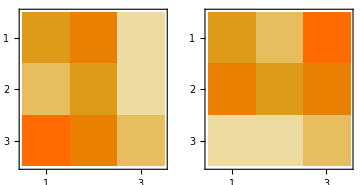

```mathematica
GraphicsRow[{MatrixPlot[m],MatrixPlot[mt]},ImageSize->Medium]
```

```mathematica
SymbolicIndexedArray[x,{2,19}]//MatrixForm
```

(x11 | x12 | x13 | x14 | x15 | x16 | x17 | x18 | x19 | x110 | x111 | x112 | x113 | x114 | x115 | x116 | x117 | x118 | x119
x21 | x22 | x23 | x24 | x25 | x26 | x27 | x28 | x29 | x210 | x211 | x212 | x213 | x214 | x215 | x216 | x217 | x218 | x219)

```mathematica
Transpose[SymbolicIndexedArray[x,{2,19}]]//MatrixForm
```

(x11 | x21
x12 | x22
x13 | x23
x14 | x24
x15 | x25
x16 | x26
x17 | x27
x18 | x28
x19 | x29
x110 | x210
x111 | x211
x112 | x212
x113 | x213
x114 | x214
x115 | x215
x116 | x216
x117 | x217
x118 | x218
x119 | x219)

```mathematica
Transpose[{{b,c},{d,f},{g,h}}]
```

{{b,d,g},{c,f,h}}